```mathematica
Get["Minimal.wl",Path->NotebookDirectory[]]
SetOptions[Contract,Dimension-> d]
{Dimension->d,Vectors->Automatic,Indices->All};
```

{Dimension→d,Vectors→Automatic,Indices→All}

## Initialization

#### Formatting

```mathematica
Format[Cor[exp_]]:=⟨exp⟩
Format[Cor[exp_,exp2_]]:=Subscript[⟨exp⟩, exp2]
Format[e[i_,j_,k_]]:= Superscript[ϵ,{i,j,k}];

CorrFormat={o[i_]o[j_]o[k_]o[l_]->Cor[o[i]o[j]o[k]o[l]],Subscript[T, μ_ ν_][i_]o[j_]o[k_]o[l_]->Cor[Subscript[T, μ ν][i]o[j]o[k]o[l]],Subscript[J, μ_ ν_ σ_ ρ_][i_]o[j_]o[k_]o[l_]->Cor[Subscript[J, μ ν σ ρ][i]o[j]o[k]o[l]],o[i_]o[j_]Subscript[J, α_][k_]Subscript[J, β_][l_]->Cor[o[i]o[j]Subscript[J, α][k]Subscript[J, β][l]],Subscript[J, α_][i_]Subscript[J, β_][j_]Subscript[J, γ_][k_]Subscript[J, σ_][l_]->Cor[Subscript[J, α][i]Subscript[J, β][j]Subscript[J, γ][k]Subscript[J, σ][l]],Subscript[J, α_][i_]Subscript[J, β_][j_]o[k_]Subscript[T, μ_ ν_][l_]->Cor[Subscript[J, α][i]Subscript[J, β][j]o[k]Subscript[T, μ ν][l]],
Subscript[T, μ_ ν_][i_]Subscript[T, α_ β_][j_]Subscript[T, γ_ δ_][k_]Subscript[T, σ_ ρ_][l_]->Cor[Subscript[T, μ ν][i]Subscript[T, α β][j]Subscript[T, γ δ][k]Subscript[T, σ ρ][l]],Subscript[T, μ_ ν_][i_]Subscript[T, α_ β_][j_]Subscript[T, γ_ δ_][k_]o[l_]->Cor[Subscript[T, μ ν][i]Subscript[T, α β][j]Subscript[T, γ δ][k]o[l]],Subscript[T, μ_ ν_][i_]Subscript[T, α_ β_][j_]o[k_]o[l_]->Cor[Subscript[T, μ ν][i]Subscript[T, α β][j]o[k]o[l]],Subscript[J, μ_ ν_ σ_ ρ_][i_]Subscript[T, α_ β_][j_]Subscript[T, γ_ δ_][k_]o[l_]->Cor[Subscript[J, μ ν σ ρ][i]Subscript[T, α β][j]Subscript[T, γ δ][k]o[l]]};

CorrFormat2={Subscript[T, m_^2][i_]Subscript[T, m_^2][j_]Subscript[T, m_^2][k_]Subscript[T, m_^2][l_]->Cor[Subscript[T, m m][i]Subscript[T, m m][j]Subscript[T, m m][k]Subscript[T, m m][l]],Subscript[T, μ_ ν_][i_]Subscript[T, α_ β_][j_]Subscript[T, γ_ δ_][k_]o[l_]->Cor[Subscript[T, μ ν][i]Subscript[T, α β][j]Subscript[T, γ δ][k]o[l]]};
```

#### Symmetrization Functions

```mathematica
Sym[expr_,μ_,ν_,ρ_]:=(expr+(expr/.{ρ->ν, ν->ρ})+(expr/.{μ->ν, ν->μ })+(expr/.{μ->ρ, ρ->μ })+(expr/.{μ->ν, ν->ρ, ρ->μ})+(expr/.{μ->ρ, ρ->ν,ν->μ }))/6

Sym[expr_,μ_,ν_]:=(expr+(expr/.{μ->ν, ν->μ }))/2
```

#### Epsilon contractions

```mathematica
PermuteEpsilon=Dispatch[{e[i_,j_,k_] :> Signature[e[i,j,k]]*Sort[e[i,j,k]]}];

epsx={e[x_,a_+b_,z_]->e[x,a,z]+e[x,b,z],e[x_,y_,a_+b_]->e[x,y,a]+e[x,y,b]};
epsx2={e[x_,x_,z_]->0,e[x_,z_,x_]->0,e[z_,x_,x_]->0,e[x_,x_,x_]->0};
epsx3={e[-x_,y_,z_]->-e[x,y,z],e[x_,-y_,z_]->-e[x,y,z],e[x_,y_,-z_]->-e[x,y,z]};

epsprod={e[i_,j_,k_]e[l_,m_,n_]->(δ[i,l](δ[j,m]δ[k,n]-δ[j,n]δ[k,m])-δ[i,m](δ[j,l]δ[k,n]-δ[j,n]δ[k,l])+δ[i,n](δ[j,l]δ[k,m]-δ[j,m]δ[k,l]))};

epsprod2={e[i_,j_,k_]e[i_,m_,n_]->δ[j,m]δ[k,n]-δ[k,m]δ[j,n],e[i_,j_,k_]e[m_,n_,i_]->δ[j,m]δ[k,n]-δ[k,m]δ[j,n],
e[i_,j_,k_]e[m_,i_,n_]->-δ[j,m]δ[k,n]+δ[k,m]δ[j,n],e[k_,i_,j_]e[n_,i_,m_]->δ[j,m]δ[k,n]-δ[k,m]δ[j,n],e[k_,i_,j_]e[m_,n_,i_]->δ[j,m]δ[k,n]-δ[k,m]δ[j,n]};

epscont={e[a_,b_,c_] p[i_][a_]->e[p[i],b,c],e[a_,b_,c_] p[i_][b_]->e[a,p[i],c],e[a_,b_,c_] p[i_][c_]->e[a,b,p[i]]};
```

#### Momentum identities

```mathematica
permuteip={p[2]·p[1]->p[1]·p[2],p[3]·p[1]->p[1]·p[3],p[3]·p[2]->p[2]·p[3],p[1]·p[1]->p[1]^2,p[2]·p[2]->p[2]^2,p[3]·p[3]->p[3]^2};
ipreplace3={p[1]·p[3]->(p[2]^2-p[1]^2-p[3]^2)/2,p[1]·p[2]->(p[3]^2-p[1]^2-p[2]^2)/2,p[2]·p[3]->(p[1]^2-p[2]^2-p[3]^2)/2};
ipreplace4={p[i_]·p[4]->-(p[i]·p[1]+p[i]·p[2]+p[i]·p[3]),p[4]^2->(p[1]^2+p[2]^2+p[3]^2+2(p[1]·p[2]+p[2]·p[3]+p[1]·p[3]))};
momcons3={p[3][μ_]->-p[1][μ]-p[2][μ]};
momcons4={p[4][μ_]->-p[1][μ]-p[2][μ]-p[3][μ]};
```

#### Spinor helicity

```mathematica
Format[z[i_][p]]:= Subsuperscript[z,i,"+"];
Format[z[i_][m]]:= Subsuperscript[z,i,"-"];
Format[z[i_][p][μ_]]:=Subscript[ Subsuperscript[z, i,μ],"+"];
Format[z[i_][m][μ_]]:=Subscript[ Subsuperscript[z, i,μ],"-"];

Zcontract= Dispatch[{p[i_][j_]z[k_][c_][j_]:> p[i].z[k][c],q_[j_]z[k_][c_][j_]:> q.z[k][c],δ[i_,j_]z[k_][c_][i_]:> z[k][c][j],z[i_][c_][j_]^2->0 ,p[i_].z[i_][c_]:> 0,z[i_][c1_][j_]z[k_][c2_][j_]:> z[i][c1].z[k][c2]}];

sph={p[i_].z[j_][m]:>-a[j,i,b] a[j,i]/(4 p[j]),p[i_].z[j_][p]:>a[i,j,b] a[j,b,i,b]/(4 p[j]),
z[i_][m].z[j_][m]:>-a[i,j]^2/(8 p[i] p[j]),z[i_][p].z[j_][p]:>-a[i,b,j,b]^2/(8 p[i] p[j]),
z[i_][p].z[j_][m]:>-a[j,i,b]^2/(8 p[i] p[j])};

permutesph={a[2,1]->-a[1,2],a[3,1]->-a[1,3],a[3,2]->-a[2,3],a[2,b,1,b]->-a[1,b,2,b],a[3,b,1,b]->-a[1,b,3,b],a[3,b,2,b]->-a[2,b,3,b],a[1,1]->0,a[2,2]->0,a[3,3]->0,a[1,b,1,b]->0,a[2,b,2,b]->0,a[3,b,3,b]->0,a[1,1,b]->-2 p[1],a[2,2,b]->-2 p[2],a[3,3,b]->-2 p[3]};
```

#### Projection operators and magnitude function

```mathematica
pi[n_][i_,j_] := δ[i,j] - p[n][i] p[n][j] / p[n]^2;
PI[d_][n_][i_,j_,k_,l_]:=1/2( pi[n][i,k]pi[n][j,l]+pi[n][i,l]pi[n][j,k]) - 1/(d-1) pi[n][i,j] pi[n][k,l];
Sigma[i_,j_][μ_,ν_,α_,β_]:=p[i][c2]e[μ,c2,α]p[j][d2]e[ν,d2,β];
zeta[i_,j_][μ_,ν_,α_,β_]:=pi[i][μ,α]pi[j][ν,β];
zetaodd[i_,j_][μ_,ν_,α_,β_]:=e[μ,a1,b]p[i][a1]pi[i][b,α]e[ν,b1,a]p[i][b1]pi[j][a,β]

Mf[exp_]:=If[Length[exp/.{-p[m_]->p[m]}]==1 ,exp/.{-p[m_]->p[m]},
Sqrt[Contract[Sum[exp[[j]][α]/.{(-p[m_])[α]->-p[m][α]},{j,Length[exp]}]Sum[exp[[j]][α]/.{(-p[m_])[α]->-p[m][α]},{j,Length[exp]}]]]
]
```

#### Misc

```mathematica
ffid={Subscript[X0, a_ b_ c_ d_ e_ f_ g_ h_] δ[a_,i_]->Subscript[X0, i b c d e f g h],Subscript[X1, a_ b_ c_ d_ e_ f_ g_ h_] δ[a_,i_]->Subscript[X1, i b c d e f g h],Subscript[X2, a_ b_ c_ d_ e_ f_ g_ h_] δ[a_,i_]->Subscript[X2, i b c d e f g h],
Subscript[X3, a_ b_ c_ d_ e_ f_ g_ h_] δ[a_,i_]->Subscript[X3, i b c d e f g h],Subscript[X4, a_ b_ c_ d_ e_ f_ g_ h_] δ[a_,i_]->Subscript[X4, i b c d e f g h],
Subscript[X0, α1 α2 α3 β1 β2 β3 ν_ ρ_] p[4][ν_]->0,Subscript[X1, α1 α2 α3 β1 β2 β3 ν_ ρ_] p[4][ν_]->0,Subscript[X2, α1 α2 α3 β1 β2 β3 ν_ ρ_] p[4][ν_]->0,Subscript[X3, α1 α2 α3 β1 β2 β3 ν_ ρ_] p[4][ν_]->0,Subscript[X4, α1 α2 α3 β1 β2 β3 ν_ ρ_] p[4][ν_]->0};

PE={X3->X1,Subscript[X2, a_ b_ c_ d_ e_ f_ g_ h_]->Subscript[X0, a b c d e f g h]+Subscript[X4, a b c d e f g h]};

ffreplace=
{A1[1,2,3,4]->A1,B1[1,2,3,4]->B1,C1[1,2,3,4]->C1,D1[1,2,3,4]->D1,E1[1,2,3,4]->E1,
A1[1,3,2,4]->A2,B1[1,3,2,4]->B2,C1[1,3,2,4]->C2,D1[1,3,2,4]->D2,E1[1,3,2,4]->E2,
A1[1,4,3,2]->A3,B1[1,4,3,2]->B3,C1[1,4,3,2]->C3,D1[1,4,3,2]->D3,E1[1,4,3,2]->E3,
F1[1,2,3,4]->F1,G1[1,2,3,4]->G1,H1[1,2,3,4]->H1,I1[1,2,3,4]->I1,J1[1,2,3,4]->J1,
F1[1,3,2,4]->F2,G1[1,3,2,4]->G2,H1[1,3,2,4]->H2,I1[1,3,2,4]->I2,J1[1,3,2,4]->J2,
F1[1,4,3,2]->F3,G1[1,4,3,2]->G3,H1[1,4,3,2]->H3,I1[1,4,3,2]->I3,J1[1,4,3,2]->J3};
ffreplacerev={A1->A1[1,2,3,4],B1->B1[1,2,3,4],C1->C1[1,2,3,4],D1->D1[1,2,3,4],E1->E1[1,2,3,4],
A2->A1[1,3,2,4],B2->B1[1,3,2,4],C2->C1[1,3,2,4],D2->D1[1,3,2,4],E2->E1[1,3,2,4],
A3->A1[1,4,3,2],B3->B1[1,4,3,2],C3->C1[1,4,3,2],D3->D1[1,4,3,2],E3->E1[1,4,3,2],
F1->F1[1,2,3,4],G1->G1[1,2,3,4],H1->H1[1,2,3,4],I1->I1[1,2,3,4],J1->J1[1,2,3,4],
F2->F1[1,3,2,4],G2->G1[1,3,2,4],H2->H1[1,3,2,4],I2->I1[1,3,2,4],J2->J1[1,3,2,4],
F3->F1[1,4,3,2],G3->G1[1,4,3,2],H3->H1[1,4,3,2],I3->I1[1,4,3,2],J3->J1[1,4,3,2]};

ffrelations={}

Den=(e[i,j,k]p[1][i]p[2][j]p[3][k]e[l,m,n]p[1][l]p[2][m]p[3][n]/.epsprod//Contract)
```

{}

2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2

## Ansatzes

```mathematica
Sigma[1,2][α1,β1,μ,ν]
```

ϵ^{α1,c2,μ} ϵ^{β1,d2,ν} p_1^c2 p_2^d2

```mathematica
JJOOeven[i_,j_,k_,l_,μ_,ν_]:=Sigma[i,j][α1,β1,μ,ν](A1[i,j,k,l] p[j][α1]p[i][β1]+B1[i,j,k,l] p[k][α1]p[i][β1]+C1[i,j,k,l] p[j][α1]p[k][β1]+D1[i,j,k,l] p[k][α1]p[k][β1])//Contract
```

```mathematica
JJOOodd[i_,j_,k_,l_,μ_,ν_]:=((e[μ,a1,α1]p[i][a1])/p[i] pi[j][ν,β1]+pi[i][μ,α1](e[ν,a1,β1]p[j][a1])/p[j])(E1[i,j,k,l] p[j][α1]p[i][β1]+F1[i,j,k,l] p[k][α1]p[i][β1]+G1[i,j,k,l] p[j][α1]p[k][β1]+H1[i,j,k,l] p[k][α1]p[k][β1])//Contract

JJOOodd0[i_,j_,k_,l_,μ_,ν_]:=(e[l1,m1,n1]p[i][l1]p[j][m1]p[k][n1])zeta[i,j][α1,β1,μ,ν](E1[i,j,k,l] p[j][α1]p[i][β1]+F1[i,j,k,l] p[k][α1]p[i][β1]+G1[i,j,k,l] p[j][α1]p[k][β1]+H1[i,j,k,l] p[k][α1]p[k][β1])//Contract

JJOOodd2[i_,j_,k_,l_,μ_,ν_]:=((e[μ,a1,α1]p[i][a1])/p[i] pi[j][ν,β1])(E1[i,j,k,l] p[j][α1]p[i][β1]+F1[i,j,k,l] p[k][α1]p[i][β1]+G1[i,j,k,l] p[j][α1]p[k][β1]+H1[i,j,k,l] p[k][α1]p[k][β1])//Contract
```

```mathematica
JJOOoddalt[i_,j_,k_,l_,μ_,ν_]:=zeta[i,j][α1,β1,μ,ν](FF1[i,j,k,l]e[α1,a,b]p[1][a]p[2][b]p[1][β1]+FF2[i,j,k,l]e[α1,a,b]p[1][a]p[2][b]p[3][β1]
+FF3[i,j,k,l]e[α1,a,b]p[1][a]p[3][b]p[1][β1]+FF4[i,j,k,l]e[α1,a,b]p[1][a]p[3][b]p[3][β1]
+FF5[i,j,k,l]e[α1,a,b]p[2][a]p[3][b]p[1][β1]+FF6[i,j,k,l]e[α1,a,b]p[2][a]p[3][b]p[3][β1]
+FF7[i,j,k,l]e[β1,a,b]p[1][a]p[2][b]p[2][α1]+FF8[i,j,k,l]e[β1,a,b]p[1][a]p[2][b]p[3][α1]
+FF9[i,j,k,l]e[β1,a,b]p[1][a]p[3][b]p[2][α1]+FF10[i,j,k,l]e[β1,a,b]p[1][a]p[3][b]p[3][α1]
+FF11[i,j,k,l]e[β1,a,b]p[1][a]p[3][b]p[2][α1]+FF12[i,j,k,l]e[β1,a,b]p[1][a]p[3][b]p[3][α1])
```

## Pole Equations

```mathematica
Clear[i,j]
```

```mathematica
PE1Lterm[i_,j_,k_,l_,μ_,ν_,α_]:=Sym[c2 p[j][μ]p[j]JJOOeven[i,j,k,l,α,ν],μ,ν]
PE1Rterm[i_,j_,k_,l_,μ_,ν_,α_]:=Sym[-e[c1,d1,μ]p[j][d1]p[j][ν]JJOOodd[i,j,k,l,α,c1],μ,ν]
PE2Lterm[i_,j_,k_,l_,μ_,ν_,α_]:=Sym[e[c1,d1,μ]p[j][d1]p[j][ν]JJOOeven[i,j,k,l,α,c1],μ,ν]
PE2Rterm[i_,j_,k_,l_,μ_,ν_,α_]:=Sym[c2 p[j][μ]p[j]JJOOodd[i,j,k,l,α,ν],μ,ν]

PE1term[i_,j_,k_,l_,μ_,ν_,α_]:=PE1Lterm[i,j,k,l,μ,ν,α]-PE1Rterm[i,j,k,l,μ,ν,α];
PE2term[i_,j_,k_,l_,μ_,ν_,α_]:=PE2Lterm[i,j,k,l,μ,ν,α]-PE2Rterm[i,j,k,l,μ,ν,α];
```

```mathematica
PE1L=((PE1Lterm[1,2,3,4,μ,ν,α]+PE1Lterm[1,3,2,4,μ,ν,α]+PE1Lterm[1,4,3,2,μ,ν,α]//Expand)/.ipreplace4/.permuteip/.momcons4)//Expand;
PE1R=(((PE1Rterm[1,2,3,4,μ,ν,α]+PE1Rterm[1,3,2,4,μ,ν,α]+PE1Rterm[1,4,3,2,μ,ν,α]//Expand)/.epsprod2/.epsprod//Contract)/.ipreplace4/.permuteip/.momcons4)//Expand;

PE2L=((((PE2Lterm[1,2,3,4,μ,ν,α]+PE2Lterm[1,3,2,4,μ,ν,α]+PE2Lterm[1,4,3,2,μ,ν,α])//Expand//Contract)/.ipreplace4/.permuteip/.momcons4)//Expand)/.PermuteEpsilon;

PE2R=((((PE2Rterm[1,2,3,4,μ,ν,α]+PE2Rterm[1,3,2,4,μ,ν,α]+PE2Rterm[1,4,3,2,μ,ν,α])//Expand//Contract)/.ipreplace4/.permuteip/.momcons4)//Expand)/.PermuteEpsilon;
```

```mathematica
TestPE1L=(pi[2][μ,σ]pi[2][ν,ρ]PE1L//Expand//Contract)/.{d->3};
TestPE1R=(pi[2][μ,σ]pi[2][ν,ρ]PE1R//Expand//Contract)/.{d->3};
TestPE2L=((pi[2][μ,σ]pi[2][ν,ρ]PE2L//Expand//Contract)/.PermuteEpsilon)/.{d->3};
TestPE2R=((pi[2][μ,σ]pi[2][ν,ρ]PE2R//Expand//Contract)/.PermuteEpsilon)/.{d->3};
```

```mathematica
PE1=((TestPE1L-TestPE1R)//Expand)//.ffreplace
PE2=((TestPE2L-TestPE2R)//Expand)//.ffreplace
```

(E3 (p_1·p_2)^2 δ_(α,σ) p_1^ρ)/(2 p_1)+(E3 p_1·p_2 p_1·p_3 δ_(α,σ) p_1^ρ)/p_1-(F3 p_1·p_2 p_1·p_3 δ_(α,σ) p_1^ρ)/(2 p_1)-(G3 p_1·p_2 p_1·p_3 δ_(α,σ) p_1^ρ)/(2 p_1)+(E3 (p_1·p_3)^2 δ_(α,σ) p_1^ρ)/(2 p_1)-(F3 (p_1·p_3)^2 δ_(α,σ) p_1^ρ)/(2 p_1)-(G3 (p_1·p_3)^2 δ_(α,σ) p_1^ρ)/(2 p_1)+(H3 (p_1·p_3)^2 δ_(α,σ) p_1^ρ)/(2 p_1)+(G3 p_1·p_2 p_2·p_3 δ_(α,σ) p_1^ρ)/(2 p_1)-(G3 p_1·p_3 p_2·p_3 δ_(α,σ) p_1^ρ)/(2 p_1)+(H3 p_1·p_3 p_2·p_3 δ_(α,σ) p_1^ρ)/(2 p_1)-E3 p_2·p_3 p_1 δ_(α,σ) p_1^ρ+2332+(F3 p_1·p_3 p_3^α p_3^ρ p_3^σ)/p_4-(G3 p_1·p_3 p_3^α p_3^ρ p_3^σ)/p_4+(H3 p_1·p_3 p_3^α p_3^ρ p_3^σ)/p_4-(G3 p_2·p_3 p_3^α p_3^ρ p_3^σ)/p_4+(H3 p_2·p_3 p_3^α p_3^ρ p_3^σ)/p_4-(E3 p_1^2 p_3^α p_3^ρ p_3^σ)/p_4+(F3 p_1^2 p_3^α p_3^ρ p_3^σ)/p_4-(G3 p_3^2 p_3^α p_3^ρ p_3^σ)/p_4+(H3 p_3^2 p_3^α p_3^ρ p_3^σ)/p_4+G3 p_4 p_3^α p_3^ρ p_3^σ-H3 p_4 p_3^α p_3^ρ p_3^σ
 |  |  |  |

-(c2 E3 p_1·p_2 ϵ^{a1,β1,σ} p_1^α p_1^β1 p_1^ρ p_2^a1)/(2 p_1^2)-(c2 E3 p_1·p_3 ϵ^{a1,β1,σ} p_1^α p_1^β1 p_1^ρ p_2^a1)/(2 p_1^2)+(c2 F3 p_1·p_3 ϵ^{a1,β1,σ} p_1^α p_1^β1 p_1^ρ p_2^a1)/(2 p_1^2)-(c2 E3 p_1·p_2 ϵ^{a1,β1,ρ} p_1^α p_1^β1 p_1^σ p_2^a1)/(2 p_1^2)-(c2 E3 p_1·p_3 ϵ^{a1,β1,ρ} p_1^α p_1^β1 p_1^σ p_2^a1)/(2 p_1^2)+(c2 F3 p_1·p_3 ϵ^{a1,β1,ρ} p_1^α p_1^β1 p_1^σ p_2^a1)/(2 p_1^2)+1/2 c2 E3 ϵ^{a1,β1,σ} p_1^β1 p_1^ρ p_2^a1 p_2^α+1802+(c2 F3 ϵ^{a1,α,α1} p_1 p_1^a1 p_3^α1 p_3^ρ p_3^σ)/p_4-(c2 G3 ϵ^{a1,α,α1} p_3^2 p_1^a1 p_3^α1 p_3^ρ p_3^σ)/(p_1 p_4)+(c2 H3 ϵ^{a1,α,α1} p_3^2 p_1^a1 p_3^α1 p_3^ρ p_3^σ)/(p_1 p_4)+(c2 G3 ϵ^{a1,α,α1} p_4 p_1^a1 p_3^α1 p_3^ρ p_3^σ)/p_1-(c2 H3 ϵ^{a1,α,α1} p_4 p_1^a1 p_3^α1 p_3^ρ p_3^σ)/p_1
 |  |  |  |

```mathematica
Clear[i,j]
```

```mathematica
PE2trial=(((((e[l,m,n]p[1][l]p[2][m]p[3][n])(PE2term[1,2,3,4,μ,ν,α]+PE2term[1,3,2,4,μ,ν,α]+PE2term[1,4,3,2,μ,ν,α])//Expand)/.epsprod//Contract)//.ffreplace)/.{d->3}/.momcons4//Expand)/.epsprod2/.epsprod//Contract;

TestPE2=(pi[2][μ,σ]pi[2][ν,ρ]PE2trial//Expand)//Contract;
EPE2=TestPE2
```

-c2 E3 p_1·p_3 p_2·p_4 p_1^α p_1^ρ p_1^σ-A3 p_1·p_2 p_2·p_3 p_2·p_4 p_1^α p_1^ρ p_1^σ+A3 p_1·p_3 p_2·p_3 p_2·p_4 p_1^α p_1^ρ p_1^σ-B3 p_1·p_3 p_2·p_3 p_2·p_4 p_1^α p_1^ρ p_1^σ+c2 E3 p_1·p_2 p_3·p_4 p_1^α p_1^ρ p_1^σ+c2 G3 p_2·p_3 p_3·p_4 p_1^α p_1^ρ p_1^σ-A3 p_1·p_2 p_2·p_3 p_3·p_4 p_1^α p_1^ρ p_1^σ+C3 p_1·p_2 p_2·p_3 p_3·p_4 p_1^α p_1^ρ p_1^σ+4242+(c2 E3 p_1·p_4 p_2·p_4 p_1 p_3^α p_3^ρ p_3^σ)/p_4+(c2 H3 p_2·p_3 p_3·p_4 p_1 p_3^α p_3^ρ p_3^σ)/p_4+(c2 G3 p_2·p_4 p_3·p_4 p_1 p_3^α p_3^ρ p_3^σ)/p_4-(c2 H3 p_1·p_2 p_1·p_3 p_4 p_3^α p_3^ρ p_3^σ)/p_1-(c2 G3 p_1·p_2 p_1·p_4 p_4 p_3^α p_3^ρ p_3^σ)/p_1+c2 H3 p_2·p_3 p_1 p_4 p_3^α p_3^ρ p_3^σ+c2 G3 p_2·p_4 p_1 p_4 p_3^α p_3^ρ p_3^σ
 |  |  |  |

```mathematica
PE1test=PE1/.{δ[μ_,ν_]->DeltaExp[μ,ν]}//Expand
```

(2 E3 p_2·p_3 p_1^α p_1^ρ p_1^σ)/p_1-(F3 p_2·p_3 p_1^α p_1^ρ p_1^σ)/p_1-(G3 p_2·p_3 p_1^α p_1^ρ p_1^σ)/p_1+(E3 p_2^2 p_1^α p_1^ρ p_1^σ)/p_1+(E3 p_3^2 p_1^α p_1^ρ p_1^σ)/p_1-(F3 p_3^2 p_1^α p_1^ρ p_1^σ)/p_1-(G3 p_3^2 p_1^α p_1^ρ p_1^σ)/p_1+6076+(H3 p_2·p_3 p_3^α p_3^ρ p_3^σ)/p_4-(E3 p_1^2 p_3^α p_3^ρ p_3^σ)/p_4+(F3 p_1^2 p_3^α p_3^ρ p_3^σ)/p_4-(G3 p_3^2 p_3^α p_3^ρ p_3^σ)/p_4+(H3 p_3^2 p_3^α p_3^ρ p_3^σ)/p_4+G3 p_4 p_3^α p_3^ρ p_3^σ-H3 p_4 p_3^α p_3^ρ p_3^σ
 |  |  |  |

```mathematica
Clear[i,j]
```

```mathematica
PE1=PE1test
```

(2 E3 p_2·p_3 p_1^α p_1^ρ p_1^σ)/p_1-(F3 p_2·p_3 p_1^α p_1^ρ p_1^σ)/p_1-(G3 p_2·p_3 p_1^α p_1^ρ p_1^σ)/p_1+(E3 p_2^2 p_1^α p_1^ρ p_1^σ)/p_1+(E3 p_3^2 p_1^α p_1^ρ p_1^σ)/p_1-(F3 p_3^2 p_1^α p_1^ρ p_1^σ)/p_1-(G3 p_3^2 p_1^α p_1^ρ p_1^σ)/p_1+6076+(H3 p_2·p_3 p_3^α p_3^ρ p_3^σ)/p_4-(E3 p_1^2 p_3^α p_3^ρ p_3^σ)/p_4+(F3 p_1^2 p_3^α p_3^ρ p_3^σ)/p_4-(G3 p_3^2 p_3^α p_3^ρ p_3^σ)/p_4+(H3 p_3^2 p_3^α p_3^ρ p_3^σ)/p_4+G3 p_4 p_3^α p_3^ρ p_3^σ-H3 p_4 p_3^α p_3^ρ p_3^σ
 |  |  |  |

```mathematica
(*EPE2=(((e[μ,db,α]p[1][db])/p[1](TestPE2/.PermuteEpsilon)//Expand)/.epsprod2/.epsprod//Contract)/.{μ->α}/.{d->3}*)
```

### Collecting equations

#### PE1

```mathematica
P1Eq2a=Coefficient[PE1,p[1][σ]p[1][ρ]p[1][α]];
P1Eq2b=Coefficient[PE1,p[2][σ]p[2][ρ]p[2][α]];
P1Eq2c=Coefficient[PE1,p[3][σ]p[3][ρ]p[3][α]];

P1Eq3a=Coefficient[PE1,p[1][σ]p[1][ρ]p[2][α]];
P1Eq3b=Coefficient[PE1,p[1][σ]p[1][α]p[2][ρ]];

P1Eq4a=Coefficient[PE1,p[1][σ]p[1][ρ]p[3][α]];
P1Eq4b=Coefficient[PE1,p[1][σ]p[1][α]p[3][ρ]];

P1Eq5a=Coefficient[PE1,p[2][σ]p[2][ρ]p[1][α]];
P1Eq5b=Coefficient[PE1,p[2][σ]p[2][α]p[1][ρ]];

P1Eq6a=Coefficient[PE1,p[2][σ]p[2][ρ]p[3][α]];
P1Eq6b=Coefficient[PE1,p[2][σ]p[2][α]p[3][ρ]];

P1Eq7a=Coefficient[PE1,p[3][σ]p[3][ρ]p[2][α]];
P1Eq7b=Coefficient[PE1,p[3][σ]p[3][α]p[2][ρ]];

P1Eq8a=Coefficient[PE1,p[3][σ]p[3][ρ]p[1][α]];
P1Eq8b=Coefficient[PE1,p[3][σ]p[3][α]p[1][ρ]];

P1Eq9a=Coefficient[PE1,p[1][σ]p[2][ρ]p[3][α]];
P1Eq9b=Coefficient[PE1,p[1][ρ]p[2][α]p[3][σ]];
P1Eq9c=Coefficient[PE1,p[1][α]p[2][σ]p[3][ρ]];
```

```mathematica
PE1-(P1Eq2a p[1][σ]p[1][ρ]p[1][α]+p[2][σ]p[2][ρ]p[2][α]P1Eq2b+p[3][σ]p[3][ρ]p[3][α]P1Eq2c+
p[1][σ]p[1][ρ]p[2][α]P1Eq3a+p[1][σ]p[1][α]p[2][ρ]P1Eq3b+p[1][ρ]p[1][α]p[2][σ]P1Eq3c
+p[1][σ]p[1][ρ]p[3][α]P1Eq4a+p[1][σ]p[1][α]p[3][ρ]P1Eq4b+p[1][ρ]p[1][α]p[3][σ]P1Eq4c
+p[2][σ]p[2][ρ]p[1][α]P1Eq5a+p[2][σ]p[2][α]p[1][ρ]P1Eq5b+p[2][ρ]p[2][α]p[1][σ]P1Eq5c
+p[2][σ]p[2][ρ]p[3][α]P1Eq6a+p[2][σ]p[2][α]p[3][ρ]P1Eq6b+p[2][ρ]p[2][α]p[3][σ]P1Eq6c
+p[3][σ]p[3][ρ]p[2][α]P1Eq7a+p[3][σ]p[3][α]p[2][ρ]P1Eq7b+p[3][ρ]p[3][α]p[2][σ]P1Eq7c
+p[3][σ]p[3][ρ]p[1][α]P1Eq8a+p[3][σ]p[3][α]p[1][ρ]P1Eq8b+p[3][ρ]p[3][α]p[1][σ]P1Eq8c
+p[1][σ]p[2][ρ]p[3][α]P1Eq9a+p[1][ρ]p[2][α]p[3][σ]P1Eq9b+p[1][α]p[2][σ]p[3][ρ]P1Eq9c
+p[1][ρ]p[2][σ]p[3][α]P1Eq9d+p[1][σ]p[2][α]p[3][ρ]P1Eq9e+p[1][α]p[2][ρ]p[3][σ]P1Eq9f)//Expand
```

(E3 (p_1·p_2)^2 DeltaExp[α,σ] p_1^ρ)/(2 p_1)+(E3 p_1·p_2 p_1·p_3 DeltaExp[α,σ] p_1^ρ)/p_1-(F3 p_1·p_2 p_1·p_3 DeltaExp[α,σ] p_1^ρ)/(2 p_1)-(G3 p_1·p_2 p_1·p_3 DeltaExp[α,σ] p_1^ρ)/(2 p_1)+1200+1/2 c2 D3 ϵ^{α1,c2,α} ϵ^{β1,d2,ρ} p_4 p_1^c2 p_1^d2 p_3^α1 p_3^β1 p_3^σ-1/2 c2 C3 ϵ^{α1,c2,α} ϵ^{β1,d2,ρ} p_4 p_1^c2 p_2^d2 p_3^α1 p_3^β1 p_3^σ+1/2 c2 D3 ϵ^{α1,c2,α} ϵ^{β1,d2,ρ} p_4 p_1^c2 p_2^d2 p_3^α1 p_3^β1 p_3^σ+(c2 C3 ϵ^{α1,c2,α} ϵ^{β1,d2,ν} p_4 p_1^c2 p_1^d2 p_2^ν p_2^ρ p_3^α1 p_3^β1 p_3^σ)/(2 p_2^2)-(c2 D3 ϵ^{α1,c2,α} ϵ^{β1,d2,ν} p_4 p_1^c2 p_1^d2 p_2^ν p_2^ρ p_3^α1 p_3^β1 p_3^σ)/(2 p_2^2)
 |  |  |  |

#### PE2

```mathematica
P2Eq1a=Coefficient[PE2,e[σ,p[1],p[2]]p[1][α]p[1][ρ]]
P2Eq1b=Coefficient[PE2,e[α,p[1],p[2]]p[1][σ]p[1][ρ]]

P2Eq2a=Coefficient[PE2,e[σ,p[1],p[3]]p[1][α]p[1][ρ]]
P2Eq2b=Coefficient[PE2,e[α,p[1],p[3]]p[1][σ]p[1][ρ]]

P2Eq3a=Coefficient[PE2,e[σ,p[2],p[3]]p[1][α]p[1][ρ]]
P2Eq3b=Coefficient[PE2,e[α,p[2],p[3]]p[1][σ]p[1][ρ]]

P2Eq4a=Coefficient[PE2,e[σ,p[1],p[2]]p[2][α]p[2][ρ]]
P2Eq4b=Coefficient[PE2,e[α,p[1],p[2]]p[2][σ]p[2][ρ]]

P2Eq5a=Coefficient[PE2,e[σ,p[1],p[3]]p[2][α]p[2][ρ]]
P2Eq5b=Coefficient[PE2,e[α,p[1],p[3]]p[2][σ]p[2][ρ]]

P2Eq6a=Coefficient[PE2,e[σ,p[2],p[3]]p[2][α]p[2][ρ]]
P2Eq6b=Coefficient[PE2,e[α,p[2],p[3]]p[2][σ]p[2][ρ]]

P2Eq7a=Coefficient[PE2,e[σ,p[1],p[2]]p[3][α]p[3][ρ]]
P2Eq7b=Coefficient[PE2,e[α,p[1],p[2]]p[3][σ]p[3][ρ]]

P2Eq8a=Coefficient[PE2,e[σ,p[1],p[3]]p[3][α]p[3][ρ]]
P2Eq8b=Coefficient[PE2,e[α,p[1],p[3]]p[3][σ]p[3][ρ]]

P2Eq9a=Coefficient[PE2,e[σ,p[2],p[3]]p[3][α]p[3][ρ]]
P2Eq9b=Coefficient[PE2,e[α,p[2],p[3]]p[3][σ]p[3][ρ]]

P2Eq10a=Coefficient[PE2,e[σ,p[1],p[2]]p[1][α]p[2][ρ]];
P2Eq10b=Coefficient[PE2,e[σ,p[1],p[2]]p[2][α]p[1][ρ]];
P2Eq10c=Coefficient[PE2,e[σ,p[1],p[2]]p[1][α]p[3][ρ]];
P2Eq10d=Coefficient[PE2,e[σ,p[1],p[2]]p[3][α]p[1][ρ]];
P2Eq10e=Coefficient[PE2,e[σ,p[1],p[2]]p[3][α]p[2][ρ]];
P2Eq10f=Coefficient[PE2,e[σ,p[1],p[2]]p[2][α]p[3][ρ]];

P2Eq11a=Coefficient[PE2,e[σ,p[1],p[3]]p[1][α]p[2][ρ]];
P2Eq11b=Coefficient[PE2,e[σ,p[1],p[3]]p[2][α]p[1][ρ]];
P2Eq11c=Coefficient[PE2,e[σ,p[1],p[3]]p[1][α]p[3][ρ]];
P2Eq11d=Coefficient[PE2,e[σ,p[1],p[3]]p[3][α]p[1][ρ]];
P2Eq11e=Coefficient[PE2,e[σ,p[1],p[3]]p[3][α]p[2][ρ]];
P2Eq11f=Coefficient[PE2,e[σ,p[1],p[3]]p[2][α]p[3][ρ]];

P2Eq12a=Coefficient[PE2,e[σ,p[2],p[3]]p[1][α]p[2][ρ]];
P2Eq12b=Coefficient[PE2,e[σ,p[2],p[3]]p[2][α]p[1][ρ]];
P2Eq12c=Coefficient[PE2,e[σ,p[2],p[3]]p[1][α]p[3][ρ]];
P2Eq12d=Coefficient[PE2,e[σ,p[2],p[3]]p[3][α]p[1][ρ]];
P2Eq12e=Coefficient[PE2,e[σ,p[2],p[3]]p[3][α]p[2][ρ]];
P2Eq12f=Coefficient[PE2,e[σ,p[2],p[3]]p[2][α]p[3][ρ]];
```

0

0

0

«15 more identical outputs»

#### Epsilon transformed PE2

```mathematica
EP2Eq2a=Coefficient[EPE2,p[1][σ]p[1][ρ]p[1][α]];
EP2Eq2b=Coefficient[EPE2,p[2][σ]p[2][ρ]p[2][α]];
EP2Eq2c=Coefficient[EPE2,p[3][σ]p[3][ρ]p[3][α]];

EP2Eq3a=Coefficient[EPE2,p[1][σ]p[1][ρ]p[2][α]];
EP2Eq3b=Coefficient[EPE2,p[1][σ]p[1][α]p[2][ρ]];

EP2Eq4a=Coefficient[EPE2,p[1][σ]p[1][ρ]p[3][α]];
EP2Eq4b=Coefficient[EPE2,p[1][σ]p[1][α]p[3][ρ]];

EP2Eq5a=Coefficient[EPE2,p[2][σ]p[2][ρ]p[1][α]];
EP2Eq5b=Coefficient[EPE2,p[2][σ]p[2][α]p[1][ρ]];

EP2Eq6a=Coefficient[EPE2,p[2][σ]p[2][ρ]p[3][α]];
EP2Eq6b=Coefficient[EPE2,p[2][σ]p[2][α]p[3][ρ]];

EP2Eq7a=Coefficient[EPE2,p[3][σ]p[3][ρ]p[2][α]];
EP2Eq7b=Coefficient[EPE2,p[3][σ]p[3][α]p[2][ρ]];

EP2Eq8a=Coefficient[EPE2,p[3][σ]p[3][ρ]p[1][α]];
EP2Eq8b=Coefficient[EPE2,p[3][σ]p[3][α]p[1][ρ]];

EP2Eq9a=Coefficient[EPE2,p[1][σ]p[2][ρ]p[3][α]];
EP2Eq9b=Coefficient[EPE2,p[1][ρ]p[2][α]p[3][σ]];
EP2Eq9c=Coefficient[EPE2,p[1][α]p[2][σ]p[3][ρ]];
```

```mathematica
Coefficient[
```

#### Check

```mathematica
Coefficient[PE1,{A1,B1,C1,D1,E1,F1,G1,H1}]
Coefficient[PE2,{A1,B1,C1,D1,E1,F1,G1,H1}]
Coefficient[EPE2,{A1,B1,C1,D1,E1,F1,G1,H1}]
```

{0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0}

## Solving the equations

#### Momentum Values

```mathematica
set1={p[1]·p[4]->-4,p[2]·p[4]->-4,p[3]·p[4]->-4,p[1]·p[3]->1,p[2]·p[3]->1,p[1]·p[2]->1,p[1]->√2,p[2]->√2,p[3]->√2,p[4]->2√3};
set2={p[1]·p[4]->-5,p[2]·p[4]->-8,p[3]·p[4]->-9,p[1]·p[3]->1,p[2]·p[3]->3,p[1]·p[2]->2,p[1]->√2,p[2]->√3,p[3]->√5,p[4]->√22};
set3={p[1]·p[4]->-13,p[2]·p[4]->-24,p[3]·p[4]->-6,p[1]·p[3]->1,p[2]·p[3]->3,p[1]·p[2]->7,p[1]->√5,p[2]->√14,p[3]->√2,p[4]->√43};
set4={p[1]·p[4]->-3,p[2]·p[4]->-18,p[3]·p[4]->-22,p[1]·p[3]->2,p[2]·p[3]->8,p[1]·p[2]->0,p[1]->1,p[2]->√10,p[3]->√12,p[4]->√43};
set5={p[1]·p[4]->-17,p[2]·p[4]->-7,p[3]·p[4]->-5,p[1]·p[3]->3,p[2]·p[3]->-1,p[1]·p[2]->3,p[1]->√11,p[2]->√5,p[3]->√3,p[4]->√29};
set6={p[1]·p[4]->-7,p[2]·p[4]->-4,p[3]·p[4]->-15,p[1]·p[3]->5,p[2]·p[3]->-3,p[1]·p[2]->-4,p[1]->√6,p[2]->√11,p[3]->√13,p[4]->√26};
set7={p[1]·p[4]->4,p[2]·p[4]->-2,p[3]·p[4]->-4,p[1]·p[3]->-10,p[2]·p[3]->-3,p[1]·p[2]->-8,p[1]->√14,p[2]->√13,p[3]->√17,p[4]->√2};
```

```mathematica
Det[{{1,1,0},{0,1,2},{1,1,1}}]
```

1

```mathematica
set5i={p[1]·p[4]->1,p[2]·p[4]->3,p[3]·p[4]->99,p[1]·p[3]->121,p[2]·p[3]->0.67,p[1]·p[2]->0.223,p[1]->1.6,p[2]->2,p[3]->1,p[4]->191};
set6i={p[1]·p[4]->78,p[2]·p[4]->23,p[3]·p[4]->109,p[1]·p[3]->9.98,p[2]·p[3]->5.67,p[1]·p[2]->91.23,p[1]->91.6,p[2]->24.87,p[3]->13,p[4]->191};
```

### Numerically (all momenta perpendicular)

```mathematica
Eq1=P1Eq1a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq2=P1Eq1b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq3=P1Eq1c/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq4=P1Eq2a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq5=P1Eq2b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq6=P1Eq2c/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq7=P1Eq3a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq8=P1Eq3b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq9=P1Eq4a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq10=P1Eq4b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq11=P1Eq5a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq12=P1Eq5b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq13=P1Eq6a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq14=P1Eq6b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq15=P1Eq7a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq16=P1Eq8b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq17=P1Eq9a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq18=P1Eq9b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq19=P1Eq9c/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};

Eq20=P2Eq1a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq21=P2Eq1b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq22=P2Eq2a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq23=P2Eq2b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq24=P2Eq3a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq25=P2Eq3b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq26=P2Eq4a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq27=P2Eq4b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq28=P2Eq5a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq29=P2Eq5b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq30=P2Eq6a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq31=P2Eq6b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq32=P2Eq7a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq33=P2Eq7b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq34=P2Eq8a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq35=P2Eq8b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq36=P2Eq9a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq37=P2Eq9b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
```

0

0

0

«15 more identical outputs»

```mathematica
Solve[{Eq1==0,Eq3==0,Eq4==0,Eq6==0,Eq7==0,Eq9==0,Eq10==0,Eq12==0,Eq14==0,Eq18==0 },{E2,F2,G2,H2,E3,F3,G3,H3}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{H2→1/3 (-A3 c2+3 B2 c2+2 c2 C3)+E3/(√3),F3→1/3 (-√3 A3 c2+√3 B3 c2+2 √3 c2 C3-2 √3 c2 D3)+E3,G3→1/3 (2 √3 A3 c2-√3 c2 C3),H3→1/3 (2 √3 B3 c2-√3 c2 D3)}}

### Numerically (two momenta perpendicular)

```mathematica
Eq1=P1Eq1a/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6}
Eq2=P1Eq1b/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6};
Eq3=P1Eq1c/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6}
Eq4=P1Eq2a/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6}
Eq5=P1Eq2b/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6};
Eq6=P1Eq2c/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6}
Eq7=P1Eq3a/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6}
Eq8=P1Eq3b/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6};
Eq9=P1Eq4a/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6}
Eq10=P1Eq4b/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6}
Eq11=P1Eq5a/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6};
Eq12=P1Eq5b/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6}
Eq13=P1Eq6a/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6}
Eq14=P1Eq6b/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6}
Eq15=P1Eq7a/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6}
Eq16=P1Eq8b/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6}
Eq17=P1Eq9a/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6};
Eq18=P1Eq9b/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6}
Eq19=P1Eq9c/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6};
```

0

0

-(2 A3 c2)/3+(2 B3 c2)/3+(c2 C3)/2-(c2 D3)/2-√(2/3) E3-√(3/2) E3+√6 E3+4 √(2/3) F3-√(3/2) F3-√6 F3-2 √(2/3) G3+√6 G3+2 √(2/3) H3-√6 H3

-(A2 c2)/2-(A3 c2)/3+(B3 c2)/3+(c2 C3)/2-(c2 D3)/2-√(2/3) E3-√(3/2) E3+√6 E3+√(2/3) F3+√(3/2) F3-√6 F3+G2/(√2)+2 √(2/3) G3-3 √(3/2) G3+√6 G3-2 √(2/3) H3+3 √(3/2) H3-√6 H3

(2 A3 c2)/3-(c2 C3)/2+4 √(2/3) E3-√(3/2) E3-√6 E3+2 √(2/3) G3-√6 G3

(2 A3 c2)/3-(2 B3 c2)/3-(c2 C3)/2+(c2 D3)/2+4 √(2/3) E3-√(3/2) E3-√6 E3-4 √(2/3) F3+√(3/2) F3+√6 F3+2 √(2/3) G3-√6 G3-2 √(2/3) H3+√6 H3

-(A2 c2)/2-(A3 c2)/6+(B3 c2)/6+G2/(√2)-2 √(2/3) G3+3/2 √(3/2) G3+2 √(2/3) H3+1/2 √(3/2) H3-√6 H3

0

0

0

-(A3 c2)/3-(B2 c2)/2+(c2 C3)/2-√(2/3) E3-√(3/2) E3+√6 E3+2 √(2/3) G3-3 √(3/2) G3+√6 G3+H2/(√2)

(A2 c2)/2+(A3 c2)/6-(B3 c2)/6-G2/(√2)+2 √(2/3) G3+1/2 √(3/2) G3-√6 G3-2 √(2/3) H3-1/2 √(3/2) H3+√6 H3

(A3 c2)/6+(B2 c2)/2+2 √(2/3) G3+1/2 √(3/2) G3-√6 G3-H2/(√2)

```mathematica
Eq20=P2Eq1a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq21=P2Eq1b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq22=P2Eq2a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq23=P2Eq2b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq24=P2Eq3a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq25=P2Eq3b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq26=P2Eq4a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq27=P2Eq4b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq28=P2Eq5a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq29=P2Eq5b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq30=P2Eq6a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq31=P2Eq6b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq32=P2Eq7a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq33=P2Eq7b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq34=P2Eq8a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq35=P2Eq8b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq36=P2Eq9a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq37=P2Eq9b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
```

0

0

0

«15 more identical outputs»

```mathematica
Solve[{Eq1==0,Eq3==0,Eq4==0,Eq6==0,Eq7==0,Eq9==0,Eq10==0,Eq12==0,Eq14==0,Eq18==0 },{E2,F2,G2,H2,E3,F3,G3,H3}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{G2→(A2 c2)/(√2),H2→1/8 (4 √2 B2 c2+√2 c2 C3)+E3/(4 √3),F3→1/2 (√6 c2 C3-√6 c2 D3)+E3,G3→1/12 (4 √6 A3 c2-3 √6 c2 C3)-E3/2,H3→1/12 (4 √6 B3 c2-3 √6 c2 C3)-E3/2}}

```mathematica
Coefficient[PE1,F2]
```

(p_1·p_2 p_1·p_3 (p_2·p_3)^2 p_1^α p_1^σ p_2^ρ)/(2 p_1^2 p_2^2 p_3)-((p_1·p_2)^2 p_2·p_3 p_3 p_1^α p_1^σ p_2^ρ)/(2 p_1^2 p_2^2)-(p_1·p_3 (p_2·p_3)^2 p_1^σ p_2^α p_2^ρ)/(2 p_2^2 p_3)+(p_1·p_2 p_2·p_3 p_3 p_1^σ p_2^α p_2^ρ)/(2 p_2^2)+(p_1·p_2 p_1·p_3 (p_2·p_3)^2 p_1^α p_1^ρ p_2^σ)/(2 p_1^2 p_2^2 p_3)-((p_1·p_2)^2 p_2·p_3 p_3 p_1^α p_1^ρ p_2^σ)/(2 p_1^2 p_2^2)-(p_1·p_3 (p_2·p_3)^2 p_1^ρ p_2^α p_2^σ)/(2 p_2^2 p_3)+(p_1·p_2 p_2·p_3 p_3 p_1^ρ p_2^α p_2^σ)/(2 p_2^2)+(p_1·p_2 (p_2·p_3)^3 p_1^α p_2^ρ p_2^σ)/(p_2^4 p_3)-(2 (p_1·p_2)^2 p_1·p_3 (p_2·p_3)^2 p_1^α p_2^ρ p_2^σ)/(p_1^2 p_2^4 p_3)+((p_1·p_2)^3 p_2·p_3 p_3 p_1^α p_2^ρ p_2^σ)/(p_1^2 p_2^4)+(2 p_1·p_2 p_1·p_3 (p_2·p_3)^2 p_2^α p_2^ρ p_2^σ)/(p_2^4 p_3)-((p_2·p_3)^3 p_1^2 p_2^α p_2^ρ p_2^σ)/(p_2^4 p_3)-((p_1·p_2)^2 p_2·p_3 p_3 p_2^α p_2^ρ p_2^σ)/p_2^4-(p_1·p_2 p_1·p_3 p_2·p_3 p_1^α p_1^σ p_3^ρ)/(2 p_1^2 p_3)+((p_1·p_2)^2 p_3 p_1^α p_1^σ p_3^ρ)/(2 p_1^2)+(p_1·p_3 p_2·p_3 p_1^σ p_2^α p_3^ρ)/(2 p_3)-1/2 p_1·p_2 p_3 p_1^σ p_2^α p_3^ρ-(p_1·p_2 (p_2·p_3)^2 p_1^α p_2^σ p_3^ρ)/(p_2^2 p_3)+(3 (p_1·p_2)^2 p_1·p_3 p_2·p_3 p_1^α p_2^σ p_3^ρ)/(2 p_1^2 p_2^2 p_3)-((p_1·p_2)^3 p_3 p_1^α p_2^σ p_3^ρ)/(2 p_1^2 p_2^2)-(3 p_1·p_2 p_1·p_3 p_2·p_3 p_2^α p_2^σ p_3^ρ)/(2 p_2^2 p_3)+((p_2·p_3)^2 p_1^2 p_2^α p_2^σ p_3^ρ)/(p_2^2 p_3)+((p_1·p_2)^2 p_3 p_2^α p_2^σ p_3^ρ)/(2 p_2^2)-(p_1·p_2 p_1·p_3 p_2·p_3 p_1^α p_1^ρ p_3^σ)/(2 p_1^2 p_3)+((p_1·p_2)^2 p_3 p_1^α p_1^ρ p_3^σ)/(2 p_1^2)+(p_1·p_3 p_2·p_3 p_1^ρ p_2^α p_3^σ)/(2 p_3)-1/2 p_1·p_2 p_3 p_1^ρ p_2^α p_3^σ-(p_1·p_2 (p_2·p_3)^2 p_1^α p_2^ρ p_3^σ)/(p_2^2 p_3)+(3 (p_1·p_2)^2 p_1·p_3 p_2·p_3 p_1^α p_2^ρ p_3^σ)/(2 p_1^2 p_2^2 p_3)-((p_1·p_2)^3 p_3 p_1^α p_2^ρ p_3^σ)/(2 p_1^2 p_2^2)-(3 p_1·p_2 p_1·p_3 p_2·p_3 p_2^α p_2^ρ p_3^σ)/(2 p_2^2 p_3)+((p_2·p_3)^2 p_1^2 p_2^α p_2^ρ p_3^σ)/(p_2^2 p_3)+((p_1·p_2)^2 p_3 p_2^α p_2^ρ p_3^σ)/(2 p_2^2)+(p_1·p_2 p_2·p_3 p_1^α p_3^ρ p_3^σ)/p_3-((p_1·p_2)^2 p_1·p_3 p_1^α p_3^ρ p_3^σ)/(p_1^2 p_3)+(p_1·p_2 p_1·p_3 p_2^α p_3^ρ p_3^σ)/p_3-(p_2·p_3 p_1^2 p_2^α p_3^ρ p_3^σ)/p_3

### Numerically P1 ( p_1=(1,1,0), p_2=(1,0,1), p_3=(0,1,1) )

```mathematica
Clear[Eq1]
```

```mathematica
Eq1[1]=P1Eq2a/.set1;
Eq1[2]=P1Eq2b/.set1;
Eq1[3]=P1Eq2c/.set1;
Eq1[4]=P1Eq3a/.set1;
Eq1[5]=P1Eq3b/.set1;
Eq1[6]=P1Eq4a/.set1;
Eq1[7]=P1Eq4b/.set1;
Eq1[8]=P1Eq5a/.set1;
Eq1[9]=P1Eq5b/.set1;
Eq1[10]=P1Eq6a/.set1;
Eq1[11]=P1Eq6b/.set1;
Eq1[12]=P1Eq7a/.set1;
Eq1[13]=P1Eq7b/.set1;
Eq1[14]=P1Eq8a/.set1;
Eq1[15]=P1Eq8b/.set1;
Eq1[16]=P1Eq9a/.set1;
Eq1[17]=P1Eq9b/.set1;
Eq1[18]=P1Eq9c/.set1;
```

```mathematica
SolP1a=(Solve[{Eq1[4]==0,Eq1[3]==0,Eq1[8]==0,Eq1[14]==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→F2,H2→-E2-(2 F2)/3,F3→(2 √2 E3)/(2 √2+√3)+(4 E3)/(3 √3 (2 √2+√3))+(4 √2 G3)/(3 (2 √2+√3))+(16 G3)/(3 √3 (2 √2+√3)),H3→-4/3 √(2/3) E3+(4 G3)/3+2/3 √(2/3) G3}

```mathematica
Chop[Eq1[14]/.SolP1a//Simplify,10^-10]
```

0

```mathematica
SolP1b=(Solve[{Eq1[5]==0,Eq1[11]==0,Eq1[12]==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{H2→-E2-(13 √2 F2)/(3 (5 √2+4 √3))+(16 F2)/(√3 (5 √2+4 √3))+(√2 G2)/(5 √2+4 √3)-(8 √3 G2)/(5 √2+4 √3),G3→E3/2-√(3/2) E3+(27 F2)/(4 √2 (5 √2+4 √3))+(3 √3 F2)/(4 (5 √2+4 √3))+3/4 √(3/2) F3-(27 G2)/(4 √2 (5 √2+4 √3))-(3 √3 G2)/(4 (5 √2+4 √3)),H3→-√6 E3-(3 √3 F2)/(2 (5 √2+4 √3))+F3/2+√(3/2) F3+(3 √3 G2)/(2 (5 √2+4 √3))}

```mathematica
Chop[Eq1[12]/.SolP1b//Simplify,10^-10]
```

0

```mathematica
SolP1c=(Solve[{Eq1[6]==0,Eq1[9]==0,Eq1[12]==0,Eq1[14]==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→F2,H2→-E2-(2 F2)/3,G3→-(3 E3)/(√2 (3 √2+2 √3))-(2 √3 E3)/(3 √2+2 √3)+(9 F3)/(2 √2 (3 √2+2 √3))+(9 √3 F3)/(4 (3 √2+2 √3)),H3→-(6 √2 E3)/(3 √2+2 √3)-(6 √3 E3)/(3 √2+2 √3)-(21 F3)/((3 √2-4 √3) (3 √2+2 √3))-(6 √6 F3)/((3 √2-4 √3) (3 √2+2 √3))}

```mathematica
Chop[Eq1[14]/.SolP1c//Simplify,10^-10]
```

0

```mathematica
SolP1d=(Solve[{Eq1[6]==0Eq1[11]==0,Eq1[12]==0,Eq1[14]==0,Eq1[15]==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten)//Simplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→-0.570034 A2 c2+1.40426 A3 c2+0.710102 B2 c2-0.930862 B3 c2-0.289898 c2 C2-1.2624 c2 C3+0.710102 c2 D2+0.315601 c2 D3+1. F2,H2→-0.619977 A2 c2-0.936175 A3 c2-0.473401 B2 c2+0.620574 B3 c2-0.140068 c2 C2+0.841602 c2 C3-0.473401 c2 D2-0.210401 c2 D3-1. E2-0.666667 F2,G3→-0.0280931 A2 c2-0.816497 A3 c2+0.0842793 B2 c2+0.872683 B3 c2+0.0842793 c2 C2+0.183503 c2 C3+0.0842793 c2 D2-0.295876 c2 D3-0.724745 E3+0.918559 F3,H3→0.105051 A2 c2-2.10639 A3 c2-0.315153 B2 c2+1.89629 B3 c2-0.315153 c2 C2+1.89361 c2 C3-0.315153 c2 D2-1.4734 c2 D3-2.44949 E3+1.72474 F3}

```mathematica
Chop[Eq1[11]/.SolP1d//Simplify,10^-10]
```

-0.237921 A2 c2+0.447698 A3 c2-0.0362372 B2 c2-0.388523 B3 c2-0.0362372 c2 C2-0.627217 c2 C3+0.213763 c2 D2+0.258866 c2 D3

```mathematica
SolP1e=(Solve[{Eq1[13]==0,Eq1[14]==0,Eq1[16]==0,Eq1[18]==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→0.359113 A2 c2-0.344124 A3 c2+0.851619 B2 c2+0.58643 B3 c2-0.148381 c2 C2+1.18705 c2 C3-0.124701 c2 D2-0.695344 c2 D3+1. F2,H2→-0.67456 A2 c2-0.833466 A3 c2-0.481715 B2 c2+0.531441 B3 c2-0.148381 c2 C2+0.697709 c2 C3-0.424361 c2 D2-0.151013 c2 D3-1. E2-0.666667 F2,G3→-0.263714 A2 c2-0.373126 A3 c2+0.0483924 B2 c2+0.487916 B3 c2+0.0483924 c2 C2-0.43765 c2 C3+0.295976 c2 D2-0.0395122 c2 D3-0.724745 E3+0.918559 F3,H3→-0.653215 A2 c2-0.679557 A3 c2-0.430643 B2 c2+0.658049 B3 c2-0.430643 c2 C2-0.105366 c2 C3+0.36612 c2 D2-0.648381 c2 D3-2.44949 E3+1.72474 F3}

```mathematica
Chop[Eq1[18]/.SolP1e//Simplify,10^-10]
```

0

```mathematica
CEq[i1_]:=Chop[Eq1[i1]/.SolP1a//Simplify,10^-10]
```

```mathematica
CEq[7]
```

-0.0632993 A2 c2+0.103367 A3 c2-0.103367 B3 c2-0.178282 c2 C3+0.0632993 c2 D2+0.0833333 c2 D3

```mathematica
Clear[i,i2]
```

```mathematica
list={};
```

```mathematica
For[i=1,i≤18,i++,AppendTo[list,CEq[i]]]
```

### Numerically P1 ( p_1=(1,1,0), p_2=(1,1,1), p_3=(0,1,2) )

```mathematica
Eq4=P1Eq2a/.set3;
Eq5=P1Eq2b/.set3;
Eq6=P1Eq2c/.set3;
Eq7=P1Eq3a/.set3;
Eq8=P1Eq3b/.set3;
Eq9=P1Eq4a/.set3;
Eq10=P1Eq4b/.set3;
Eq11=P1Eq5a/.set3;
Eq12=P1Eq5b/.set3;
Eq13=P1Eq6a/.set3;
Eq14=P1Eq6b/.set3;
Eq15=P1Eq7a/.set3;
Eq16=P1Eq7b/.set3;
Eq17=P1Eq8a/.set3;
Eq18=P1Eq8b/.set3;
Eq19=P1Eq9a/.set3;
Eq20=P1Eq9b/.set3;
Eq21=P1Eq9c/.set3;
```

```mathematica
SolP1=(Solve[{Eq4==0,Eq5==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G3→3.14252 A3 c2-0.593853 B2 c2-1.25103 B3 c2-2.66176 c2 C3+0.763525 c2 D2+0.662309 c2 D3+31.3882 E2-0.693659 E3+13.3565 F2+1.0293 F3+25.352 G2+12.0311 H2,H3→4.47862 A3 c2-0.862071 B2 c2-1.78832 B3 c2-3.81989 c2 C3+1.10838 c2 D2+0.946755 c2 D3+45.5649 E2-2.17296 E3+19.389 F2+2.27987 F3+36.8024 G2+17.465 H2}

```mathematica
SolP1=(Solve[{Eq8==0,Eq10==0,Eq11==0,Eq12==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{H2→0.,F3→0.+1.70776 E3+3.94918×10^13 G2,G3→0.+1.06414 E3+4.06488×10^13 G2,H3→0.+9.0036×10^13 G2}

```mathematica
SolP1c=(Solve[{Eq15==0,Eq18==0,Eq20==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{F3→3.2688 A2 c2+2.70231 A3 c2+0.775622 B2 c2-1.78298 B3 c2-1.89866 c2 C3+2.51949 c2 D2-0.594327 c2 D3+4.30248 E2+0.953109 E3+2.84299 F2+1.87469 G2+5.68145 H2,G3→2.11883 A2 c2+1.92536 A3 c2+0.407209 B2 c2-1.15572 B3 c2-2.44677 c2 C3+2.7797 c2 D2-0.385242 c2 D3+2.78886 E2+0.287373 E3+1.74727 F2+1.36624 G2+5.28251 H2,H3→3.8863 A2 c2+2.5599 A3 c2-0.87457 B2 c2-2.1198 B3 c2-4.3203 c2 C3+4.65624 c2 D2-0.7066 c2 D3+5.11525 E2+1.58334 F2+5.06968 G2+10.6452 H2}

### Numerically EP2 ( p_1=(1,1,0), p_2=(1,0,1), p_3=(0,1,1) )

```mathematica
Eq2[1]=EP2Eq2a/.set1;
Eq2[2]=EP2Eq2b/.set1;
Eq2[3]=EP2Eq2c/.set1;
Eq2[4]=EP2Eq3a/.set1;
Eq2[5]=EP2Eq3b/.set1;
Eq2[6]=EP2Eq4a/.set1;
Eq2[7]=EP2Eq4b/.set1;
Eq2[8]=EP2Eq5a/.set1;
Eq2[9]=EP2Eq5b/.set1;
Eq2[10]=EP2Eq6a/.set1;
Eq2[11]=EP2Eq6b/.set1;
Eq2[12]=EP2Eq7a/.set1;
Eq2[13]=EP2Eq7b/.set1;
Eq2[14]=EP2Eq8a/.set1;
Eq2[15]=EP2Eq8b/.set1;
Eq2[16]=EP2Eq9a/.set1;
Eq2[17]=EP2Eq9b/.set1;
Eq2[18]=EP2Eq9c/.set1;
```

```mathematica
SolEP2b=Solve[{Eq2[1]==0,Eq2[2]==0,Eq2[3]==0,Eq2[4]==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//N//Flatten//Expand
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→-(2. A2)/c2-(19.5959 A3)/c2+(2. B2)/c2-(19.5959 B3)/c2+(4. C2)/c2-(62.202 C3)/c2+(4. D2)/c2+(51.798 D3)/c2+F2,H2→(6.53197 A3)/c2+(2.66667 B2)/c2-(19.5959 B3)/c2+(2. C2)/c2-(43.266 C3)/c2+(3.33333 D2)/c2+(27.798 D3)/c2-1. E2-0.666667 F2,E3→(4.89898 A3)/c2-(6.20908 B3)/c2-(2.44949 C3)/c2+(3.10454 D3)/c2+1.26742 F3-1.3798 G3,H3→(6.75959 B3)/c2-(3.3798 D3)/c2-1.3798 F3+3.3798 G3}

```mathematica
Eq2[3]/.SolEP2b//Simplify
```

0.+2.90078×10^-15 B3-2.90078×10^-15 C3-1.45039×10^-15 D3+3.62597×10^-16 c2 F3

```mathematica
SolEP2=Solve[{Eq2[5]==0,Eq2[7]==0,Eq2[8]==0,Eq2[9]==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//N//Flatten//Expand
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→(0.381378 A2)/c2-(9.89795 A3)/c2-(1.37117 B2)/c2+(3.73673 B3)/c2+(0.628827 C2)/c2+(1.97959 C3)/c2-(0.628827 D2)/c2+(2.64694 D3)/c2+F2,H2→(1.36437 A2)/c2+(16.4966 A3)/c2+(0.285288 B2)/c2-(6.22788 B3)/c2-(0.381378 C2)/c2-(3.29932 C3)/c2+(0.381378 D2)/c2-(4.41157 D3)/c2-1. E2-0.666667 F2,G3→(0.112086 A2)/c2+(1.79337 A3)/c2+(0.0672514 B2)/c2-(3.40179 B3)/c2+(0.0672514 C2)/c2-(0.358674 C3)/c2-(0.0672514 D2)/c2+(1.9699 D3)/c2-0.724745 E3+0.918559 F3,H3→(0.378827 A2)/c2+(6.06123 A3)/c2+(0.227296 B2)/c2-(4.73776 B3)/c2+(0.227296 C2)/c2-(1.21225 C3)/c2-(0.227296 D2)/c2+(3.27806 D3)/c2-2.44949 E3+1.72474 F3}

```mathematica
Chop[Eq2[8]/.SolEP2//Simplify,10^-10]
```

0

```mathematica
SolEP2c=Solve[{Eq2[10]==0,Eq2[11]==0,Eq2[12]==0,Eq2[13]==0,Eq2[16]==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//N//Expand
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→(0.061071 A2)/c2-(11.0637 A3)/c2-(0.931888 B2)/c2+(0.598371 B3)/c2+(1.06811 C2)/c2-(6.55264 C3)/c2-(0.0156633 D2)/c2+(9.13061 D3)/c2+F2,H2→(1.56617 A2)/c2+(9.44136 A3)/c2+(0.803555 B2)/c2-(4.25061 B3)/c2+(0.136888 C2)/c2-(3.56925 C3)/c2+(0.525085 D2)/c2-(1.34122 D3)/c2-1. E2-0.666667 F2,G3→(0.395261 A2)/c2-(0.776837 A3)/c2+(0.0463966 B2)/c2-(0.627245 B3)/c2+(0.0463966 C2)/c2+(4.5748 C3)/c2-(0.36433 D2)/c2-(0.454592 D3)/c2-0.724745 E3+0.918559 F3,H3→(0.641148 A2)/c2+(2.72694 A3)/c2+(0.30528 B2)/c2-(2.16755 B3)/c2+(0.30528 C2)/c2+(2.66694 C3)/c2-(0.437628 D2)/c2+(1.90785 D3)/c2-2.44949 E3+1.72474 F3}

```mathematica
Eq2[2]/.SolEP2c//Simplify
```

0.+0.465153 A2-6.47265 A3+0.195459 B2+4.55755 B3+0.195459 C2+6.47265 C3-0.334847 D2-1.9151 D3+1.11022×10^-16 c2 F2-4.0548×10^-16 c2 F3

```mathematica
SolEP2d=Solve[{Eq2[2]==0,Eq2[4]==0,Eq2[7]==0,Eq2[9]==0,Eq2[12]==0,Eq2[15]==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//N//Expand
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→-(0.31143 A2)/c2+(0.401257 A3)/c2+(0.065711 B2)/c2-(0.508563 B3)/c2-(0.934289 C2)/c2-(0.95491 C3)/c2+(0.0219037 D2)/c2+(0.508563 D3)/c2+F2,H2→(0.10381 A2)/c2-(0.133752 A3)/c2-(0.0219037 B2)/c2+(0.169521 B3)/c2+(0.31143 C2)/c2+(0.318303 C3)/c2-(0.89619 D2)/c2-(0.169521 D3)/c2-1. E2-0.666667 F2,G3→-(0.0953555 A2)/c2+(0.622859 A3)/c2-(0.286066 B2)/c2-(0.155715 B3)/c2-(0.286066 C2)/c2-(1.29238 C3)/c2-(0.0953555 D2)/c2+(0.155715 D3)/c2-0.724745 E3+0.918559 F3,H3→(0.0285742 A2)/c2-(0.186646 A3)/c2+(0.0857226 B2)/c2+(0.0466615 B3)/c2+(0.0857226 C2)/c2-(1.24572 C3)/c2+(0.0285742 D2)/c2-(0.0466615 D3)/c2-2.44949 E3+1.72474 F3}

```mathematica
Chop[Eq2[2]/.SolEP2d//Simplify,10^-10]
```

0

```mathematica
SolEP2e=Solve[{Eq2[3]==0,Eq2[5]==0,Eq2[16]==0,Eq2[18]==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//N//Expand
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→(0.016674 A2)/c2-(1.28887 A3)/c2+(0.772594 B2)/c2+(0.0272285 B3)/c2-(0.227406 C2)/c2-(0.867406 C3)/c2+(0.165055 D2)/c2+(1.13694 D3)/c2+F2,H2→-(0.449254 A2)/c2+(1.02421 A3)/c2-(0.177945 B2)/c2-(0.733628 B3)/c2+(0.155388 C2)/c2-(1.05472 C3)/c2-(0.447154 D2)/c2+(0.324523 D3)/c2-1. E2-0.666667 F2,G3→(0.241147 A2)/c2-(0.0816855 A3)/c2-(0.191125 B2)/c2+(0.393792 B3)/c2-(0.191125 C2)/c2-(0.456985 C3)/c2-(0.368564 D2)/c2-(0.144878 D3)/c2-0.724745 E3+0.918559 F3,H3→(0.487916 A2)/c2-(1.14838 A3)/c2+(0.215322 B2)/c2+(0.796763 B3)/c2+(0.215322 C2)/c2-(0.105366 C3)/c2-(0.344368 D2)/c2-(0.456985 D3)/c2-2.44949 E3+1.72474 F3}

```mathematica
Chop[Eq2[3]/.SolEP2e//Simplify,10^-10]
```

0

```mathematica
SolEP2f=Solve[{Eq2[10]==0,Eq2[11]==0,Eq2[17]==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→-(4 √3 A2)/((8 √2+5 √3) c2)+(32 √2 A3)/(3 (8 √2+5 √3) c2)-(32 A3)/(3 √3 (8 √2+5 √3) c2)+(8 √2 B2)/(3 (8 √2+5 √3) c2)-(4 B2)/(√3 (8 √2+5 √3) c2)-(8 √2 B3)/((8 √2+5 √3) c2)-(4 √3 C2)/((8 √2+5 √3) c2)-(32 √2 C3)/(3 (8 √2+5 √3) c2)-(32 C3)/(3 √3 (8 √2+5 √3) c2)-(40 √2 D2)/(3 (8 √2+5 √3) c2)-(4 √3 D2)/((8 √2+5 √3) c2)+(8 √2 D3)/((8 √2+5 √3) c2)-(16 √2 E2)/(8 √2+5 √3)-(7 √3 E2)/(8 √2+5 √3)-(8 √2 F2)/(3 (8 √2+5 √3))+F2/(√3 (8 √2+5 √3))-(16 √2 H2)/(8 √2+5 √3)-(7 √3 H2)/(8 √2+5 √3),G3→(9 A2)/(2 √2 (8 √2+5 √3) c2)+(6 √2 A3)/((8 √2+5 √3) c2)-(3 √3 A3)/(2 (8 √2+5 √3) c2)-(9 B2)/(4 √2 (8 √2+5 √3) c2)-(3 √3 B2)/((8 √2+5 √3) c2)+(3 √3 B3)/((8 √2+5 √3) c2)+(9 C2)/(2 √2 (8 √2+5 √3) c2)-(6 √2 C3)/((8 √2+5 √3) c2)-(√3 C3)/((8 √2+5 √3) c2)-(87 D2)/(4 √2 (8 √2+5 √3) c2)-(9 √3 D2)/((8 √2+5 √3) c2)-(3 √3 D3)/((8 √2+5 √3) c2)-(81 E2)/(4 √2 (8 √2+5 √3))-(9 √3 E2)/(8 √2+5 √3)-(7 E3)/(√2 (8 √2+5 √3))-(11 √3 E3)/(2 (8 √2+5 √3))-(27 F2)/(2 √2 (8 √2+5 √3))-(6 √3 F2)/(8 √2+5 √3)+(45 F3)/(4 √2 (8 √2+5 √3))+(6 √3 F3)/(8 √2+5 √3)-(81 H2)/(4 √2 (8 √2+5 √3))-(9 √3 H2)/(8 √2+5 √3),H3→(3 √2 A2)/((8 √2+5 √3) c2)+(3 √3 A2)/((8 √2+5 √3) c2)-(5 √2 A3)/((8 √2+5 √3) c2)-(14 A3)/(√3 (8 √2+5 √3) c2)+B2/(√2 (8 √2+5 √3) c2)-(√3 B2)/(2 (8 √2+5 √3) c2)+(6 √2 B3)/((8 √2+5 √3) c2)+(4 √3 B3)/((8 √2+5 √3) c2)+(3 √2 C2)/((8 √2+5 √3) c2)+(3 √3 C2)/((8 √2+5 √3) c2)+(4 C3)/(√3 (8 √2+5 √3) c2)-(17 D2)/(√2 (8 √2+5 √3) c2)-(23 √3 D2)/(2 (8 √2+5 √3) c2)-(6 √2 D3)/((8 √2+5 √3) c2)-(4 √3 D3)/((8 √2+5 √3) c2)-(15 E2)/(√2 (8 √2+5 √3))-(21 √3 E2)/(2 (8 √2+5 √3))-(15 √2 E3)/(8 √2+5 √3)-(16 √3 E3)/(8 √2+5 √3)-(5 √2 F2)/(8 √2+5 √3)-(7 √3 F2)/(8 √2+5 √3)+(23 F3)/(√2 (8 √2+5 √3))+(21 √3 F3)/(2 (8 √2+5 √3))-(15 H2)/(√2 (8 √2+5 √3))-(21 √3 H2)/(2 (8 √2+5 √3))}

### Numerically EP2 ( p_1=(1,1,0), p_2=(1,1,1), p_3=(0,1,2) )

```mathematica
Eq7=EP2Eq2a/.set3;
Eq8=EP2Eq2b/.set3;
Eq9=EP2Eq2c/.set3;
Eq10=EP2Eq3a/.set3;
Eq11=EP2Eq3b/.set3;
Eq12=EP2Eq4a/.set3;
Eq13=EP2Eq4b/.set3;
Eq14=EP2Eq5a/.set3;
Eq15=EP2Eq5b/.set3;
Eq16=EP2Eq6a/.set3;
Eq17=EP2Eq6b/.set3;
Eq18=EP2Eq7a/.set3;
Eq19=EP2Eq7b/.set3;
Eq20=EP2Eq8a/.set3;
Eq21=EP2Eq8b/.set3;
Eq22=EP2Eq9a/.set3;
Eq23=EP2Eq9b/.set3;
Eq24=EP2Eq9c/.set3;
```

```mathematica
SolEP2=Solve[{Eq7==0,Eq8==0,Eq9==0,Eq10==0,Eq12==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→-(0.337584 A2)/c2+(1.53468 A3)/c2+(0.432973 B2)/c2-(1.09132 B3)/c2-(0.253188 C2)/c2-(1.99466 C3)/c2+(0.349709 D2)/c2+(1.38653 D3)/c2-0.112574 E2+0.527046 F2,H2→-(0.899251 A2)/c2-(2.18163 A3)/c2-(1.55054 B2)/c2+(1.61169 B3)/c2-(0.674438 C2)/c2+(3.03558 C3)/c2-(1.25236 D2)/c2-(2.18093 D3)/c2-2.37171 E2-2.22076 F2,G3→(1.77427 A3)/c2-(0.707151 B3)/c2-(2.30655 C3)/c2+(0.919296 D3)/c2-0.693659 E3+1.0293 F3,H3→(1.49287 A3)/c2-(0.26861 B3)/c2-(1.94074 C3)/c2+(0.349194 D3)/c2-2.17296 E3+2.27987 F3}

```mathematica
SolEP2d=Solve[{Eq11==0,Eq13==0,Eq14==0,Eq15==0,Eq20==0,Eq21==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→-(0.912808 A2)/c2+(1.15016 A3)/c2+(0.121267 B2)/c2-(0.80732 B3)/c2-(0.789209 C2)/c2-(1.45986 C3)/c2+(0.0903391 D2)/c2+(1.00238 D3)/c2-0.112574 E2+0.527046 F2,H2→(1.91269 A2)/c2-(1.24043 A3)/c2-(0.252986 B2)/c2+(0.837238 B3)/c2+(1.5882 C2)/c2+(1.4635 C3)/c2-(0.319342 D2)/c2-(0.964653 D3)/c2-2.37171 E2-2.22076 F2,E3→0.+(2.89974×10^13 A3)/c2+(3.44454×10^13 B2)/c2-(2.30395×10^13 B3)/c2-(4.57126×10^13 C3)/c2+(2.56606×10^13 D2)/c2+(3.46169×10^13 D3)/c2,F3→0.,G3→0.,H3→0.+(9.82604×10^14 A3)/c2-(6.93452×10^14 B3)/c2-(1.25959×10^15 C3)/c2+(8.69368×10^14 D3)/c2}

```mathematica
SolEP2c=Solve[{Eq16==0,Eq17==0,Eq18==0,Eq19==0,Eq22==0,Eq23==0,Eq24==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→-(6.05986 A2)/c2+(0.590938 A3)/c2-(1.97336 B2)/c2-(0.150779 B3)/c2-(4.48739 C2)/c2+(0.125576 C3)/c2-(1.20228 D2)/c2-(0.403704 D3)/c2-0.112574 E2+0.527046 F2,H2→(13.5536 A2)/c2+(0.086528 A3)/c2+(4.49935 B2)/c2-(0.688321 B3)/c2+(9.97596 C2)/c2-(2.19129 C3)/c2+(2.62633 D2)/c2+(2.25928 D3)/c2-2.37171 E2-2.22076 F2,G3→-(8.07679 A2)/c2+(0.547119 A3)/c2-(3.37117 B2)/c2+(0.551769 B3)/c2-(5.93645 C2)/c2+(0.569578 C3)/c2-(2.15315 D2)/c2-(1.53359 D3)/c2-0.693659 E3+1.0293 F3,H3→-(9.99973 A2)/c2+(0.0590382 A3)/c2-(4.15319 B2)/c2+(1.23413 B3)/c2-(7.31724 C2)/c2+(1.52522 C3)/c2-(2.63527 D2)/c2-(2.62743 D3)/c2-2.17296 E3+2.27987 F3}

```mathematica
SolEP2b=Solve[{Eq11==0,Eq13==0,Eq14==0,Eq15==0,Eq20==0,Eq21==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→-(0.912808 A2)/c2+(1.15016 A3)/c2+(0.121267 B2)/c2-(0.80732 B3)/c2-(0.789209 C2)/c2-(1.45986 C3)/c2+(0.0903391 D2)/c2+(1.00238 D3)/c2-0.112574 E2+0.527046 F2,H2→(1.91269 A2)/c2-(1.24043 A3)/c2-(0.252986 B2)/c2+(0.837238 B3)/c2+(1.5882 C2)/c2+(1.4635 C3)/c2-(0.319342 D2)/c2-(0.964653 D3)/c2-2.37171 E2-2.22076 F2,E3→0.+(2.89974×10^13 A3)/c2+(3.44454×10^13 B2)/c2-(2.30395×10^13 B3)/c2-(4.57126×10^13 C3)/c2+(2.56606×10^13 D2)/c2+(3.46169×10^13 D3)/c2,F3→0.,G3→0.,H3→0.+(9.82604×10^14 A3)/c2-(6.93452×10^14 B3)/c2-(1.25959×10^15 C3)/c2+(8.69368×10^14 D3)/c2}

### Numerically P1 & EP2 ( p_1=(1,1,0), p_2=(1,1,1), p_3=(0,1,2) )

```mathematica
Eq2p1[1]=P1Eq2a/.set1;
Eq2p1[2]=P1Eq2b/.set1;
Eq2p1[3]=P1Eq2c/.set1;
Eq2p1[4]=P1Eq3a/.set1;
Eq2p1[5]=P1Eq3b/.set1;
Eq2p1[6]=P1Eq4a/.set1;
Eq2p1[7]=P1Eq4b/.set1;
Eq2p1[8]=P1Eq5a/.set1;
Eq2p1[9]=P1Eq5b/.set1;
Eq2p1[10]=P1Eq6a/.set1;
Eq2p1[11]=P1Eq6b/.set1;
Eq2p1[12]=P1Eq7a/.set1;
Eq2p1[13]=P1Eq7b/.set1;
Eq2p1[14]=P1Eq8a/.set1;
Eq2p1[15]=P1Eq8b/.set1;
Eq2p1[16]=P1Eq9a/.set1;
Eq2p1[17]=P1Eq9b/.set1;
Eq2p1[18]=P1Eq9c/.set1;
Eq2p1[19]=EP2Eq2a/.set1;
Eq2p1[20]=EP2Eq2b/.set1;
Eq2p1[21]=EP2Eq2c/.set1;
Eq2p1[22]=EP2Eq3a/.set1;
Eq2p1[23]=EP2Eq3b/.set1;
Eq2p1[24]=EP2Eq4a/.set1;
Eq2p1[25]=EP2Eq4b/.set1;
Eq2p1[26]=EP2Eq5a/.set1;
Eq2p1[27]=EP2Eq5b/.set1;
Eq2p1[28]=EP2Eq6a/.set1;
Eq2p1[29]=EP2Eq6b/.set1;
Eq2p1[30]=EP2Eq7a/.set1;
Eq2p1[31]=EP2Eq7b/.set1;
Eq2p1[32]=EP2Eq8a/.set1;
Eq2p1[33]=EP2Eq8b/.set1;
Eq2p1[34]=EP2Eq9a/.set1;
Eq2p1[35]=EP2Eq9b/.set1;
Eq2p1[36]=EP2Eq9c/.set1;
```

```mathematica
SolPa=Chop[(Solve[{Eq2p1[3]==0,Eq2p1[4]==0,Eq2p1[20]==0,Eq2p1[19]==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand),10^-10]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→-(0.816497 A3)/c2+(0.5 B2)/c2-0.5 A2 c2+0.966326 A3 c2+0.333333 B3 c2-0.5 c2 C2+(0.908248 C3)/c2+0.0168368 c2 C3+(0.5 D2)/c2-(0.0458759 D3)/c2-0.666667 c2 D3+1. F2,H2→(1.36083 A3)/c2-(0.833333 B2)/c2-0.5 A2 c2+0.56678 A3 c2+0.333333 B3 c2-0.5 c2 C2+(1.99691 C3)/c2+0.21661 c2 C3-(0.833333 D2)/c2-(1.67887 D3)/c2-0.666667 c2 D3-1. E2-0.666667 F2,E3→-1. A3 c2-(3.10454 C3)/c2+0.5 c2 C3+(1.55227 D3)/c2+1.26742 F3-1.3798 G3,H3→(3.3798 C3)/c2-(1.6899 D3)/c2-1.3798 F3+3.3798 G3}

```mathematica
Chop[Eq2p1[19]/.SolPa//Simplify,10^-10]//Simplify
```

0

```mathematica
SolPb=Chop[(Solve[{Eq2p1[3]==0,Eq2p1[4]==0,Eq2p1[19]==0,Eq2p1[23]==0,Eq2p1[25]==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand),10^-10]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→(0.5 A2)/c2-(1.63299 A3)/c2+(0.5 B2)/c2+(0.816497 B3)/c2-2. A2 c2+4.89898 A3 c2+1.33333 B3 c2+(1.5 C2)/c2-2. c2 C2+(8.08248 C3)/c2-0.44949 c2 C3+(1.5 D2)/c2-(4.04124 D3)/c2-2.66667 c2 D3+1. F2,H2→-(0.833333 A2)/c2+(2.72166 A3)/c2-(0.833333 B2)/c2-(1.36083 B3)/c2+2. A2 c2-5.98764 A3 c2-1.33333 B3 c2-(2.5 C2)/c2+2. c2 C2-(9.96015 C3)/c2+0.993821 c2 C3-(2.5 D2)/c2+(4.98007 D3)/c2+2.66667 c2 D3-1. E2-0.666667 F2,E3→-1. A3 c2-(3.10454 C3)/c2+0.5 c2 C3+(1.55227 D3)/c2+1.26742 F3-1.3798 G3,H3→(3.3798 C3)/c2-(1.6899 D3)/c2-1.3798 F3+3.3798 G3}

```mathematica
Chop[Eq2p1[25]/.SolPb//Simplify,10^-10]//Simplify
```

0

```mathematica
SolPc=(Solve[{Eq2p1[5]==0,Eq2p1[6]==0,Eq2p1[7]==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{F3→-2.46456×10^14 A2 c2+1.12156 A3 c2-2.46456×10^14 B2 c2-1.00615×10^14 B3 c2-2.46456×10^14 c2 C3+1.73536×10^14 c2 D3-1.84842×10^14 E2+1.76201 E3-3.0807×10^14 F2+1.84842×10^14 G2-1.84842×10^14 H2,G3→-2.26385×10^14 A2 c2+0.305477 A3 c2-2.26385×10^14 B2 c2-9.24211×10^13 B3 c2-2.26385×10^14 c2 C3+1.59403×10^14 c2 D3-1.69788×10^14 E2+0.893767 E3-2.82981×10^14 F2+1.69788×10^14 G2-1.69788×10^14 H2,H3→0.-4.25074×10^14 A2 c2-4.25074×10^14 B2 c2-1.73536×10^14 B3 c2-4.25074×10^14 c2 C3+2.99305×10^14 c2 D3-3.18806×10^14 E2-5.31343×10^14 F2+3.18806×10^14 G2-3.18806×10^14 H2}

```mathematica
SolPc=(Solve[{Eq2p1[7]==0,Eq2p1[6]==0,Eq2p1[7]==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G3→-2.58712 A2 c2-0.724745 A3 c2-2.58712 B2 c2-0.137628 B3 c2-2.22474 c2 C3+1.36237 c2 D3-1.94034 E2-0.724745 E3-3.2339 F2+0.918559 F3+1.94034 G2-1.94034 H2,H3→9.67423 A2 c2-2.44949 A3 c2+9.67423 B2 c2+5.67423 B3 c2+10.899 c2 C3-7.67423 c2 D3+7.25568 E2-2.44949 E3+12.0928 F2+1.72474 F3-7.25568 G2+7.25568 H2}

```mathematica
SolPb=Chop[(Solve[{Eq2p1[3]==0,Eq2p1[4]==0,Eq2p1[19]==0,Eq2p1[23]==0,Eq2p1[25]==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand),10^-10]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→(0.5 A2)/c2-(1.63299 A3)/c2+(0.5 B2)/c2+(0.816497 B3)/c2-2. A2 c2+4.89898 A3 c2+1.33333 B3 c2+(1.5 C2)/c2-2. c2 C2+(8.08248 C3)/c2-0.44949 c2 C3+(1.5 D2)/c2-(4.04124 D3)/c2-2.66667 c2 D3+1. F2,H2→-(0.833333 A2)/c2+(2.72166 A3)/c2-(0.833333 B2)/c2-(1.36083 B3)/c2+2. A2 c2-5.98764 A3 c2-1.33333 B3 c2-(2.5 C2)/c2+2. c2 C2-(9.96015 C3)/c2+0.993821 c2 C3-(2.5 D2)/c2+(4.98007 D3)/c2+2.66667 c2 D3-1. E2-0.666667 F2,E3→-1. A3 c2-(3.10454 C3)/c2+0.5 c2 C3+(1.55227 D3)/c2+1.26742 F3-1.3798 G3,H3→(3.3798 C3)/c2-(1.6899 D3)/c2-1.3798 F3+3.3798 G3}

```mathematica
Chop[Eq2p1[23]/.SolPb//Simplify,10^-10]
```

0

```mathematica
Clear[i]
```

```mathematica
Clear[Kek1,Kek2,Kek3,Kek4,Kek5,Kek6,Kek7]
```

```mathematica
Kek1[i5_]:=Chop[Eq2p1[i5]/.SolPb//Simplify,10^-10]
```

```mathematica
lst1={}
Clear[i]
For[i=1,i≤36,i++,
	If[Length[Kek1[i]]==0,Continue[],AppendTo[lst1,Kek1[i]]]]
```

{}

```mathematica
lst1[[1]]
```

0.333333 B3 c2+(0.816497 C3)/c2-(0.408248 D3)/c2-0.166667 c2 D3

#### Iteration1

```mathematica
Sol2Pb=Solve[{lst1[[1]]==0},{D3}]//Simplify
```

{{D3→(2. B3 c2^2+4.89898 C3)/(2.44949+1. c2^2)}}

```mathematica
Kek2[i5_]:=Chop[lst1[[i5]]/.Sol2Pb//Simplify,10^-10]//Expand
```

```mathematica
lst2={}
Clear[i]
For[i=1,i≤31,i++,
	If[Length[Kek2[i][[1]]]==0,Continue[],AppendTo[lst2,Kek2[i]]]]
```

{}

```mathematica
lst2//Length
```

29

#### Iteration2

```mathematica
Sol3Pb=Chop[Flatten[Solve[{lst2[[1]]==0},{D2}]//Simplify],10^-10]
```

{D2→1/(-3.67423+0.94949 c2^2+1. c2^4)(1.22474 B2+2. B3+2.94949 B2 c2^2+4. B3 c2^2+1. B2 c2^4+A2 (1.22474+0.5 c2^2)+A3 (-4.-5.63299 c2^2-1.63299 c2^4)+3.67423 C2+1.5 c2^2 C2+3.71548 c2^2 C3+2.8165 c2^4 C3)}

```mathematica
Kek3[i5_]:=Chop[lst2[[i5]]/.Sol3Pb//Simplify,10^-10]//Expand
```

```mathematica
lst3={}
Clear[i]
For[i=1,i≤29,i++,
	If[Length[Kek3[i][[1]]]==0,Continue[],AppendTo[lst3,Kek3[i]]]]
```

{}

```mathematica
lst3//Length
```

28

#### Iteration3

```mathematica
Sol4Pb=Chop[Flatten[Solve[{lst3[[1]]==0},{C3}]//Simplify],10^-10]
```

{C3→(15.8465 B2+32.9346 B3+10.0574 B2 c2^2+12.8574 B3 c2^2+0.288608 B2 c2^4-6.12127 B3 c2^4-0.480196 B2 c2^6-2.40098 B3 c2^6+A2 (20.1682+4.94259 c2^2-6.04851 c2^4-1.92078 c2^6)+A3 (-58.8118-24.4949 c2^2+9.40588 c2^4+3.92078 c2^6)+21.6088 C2+9. c2^2 C2-3.45594 c2^4 C2-1.44059 c2^6 C2)/(-26.7236-15.4475 c2^2+0.597019 c2^4+1. c2^6)}

```mathematica
Kek4[i5_]:=Chop[lst3[[i5]]/.Sol4Pb//Simplify,10^-10]//Expand
```

```mathematica
Kek4[1]
```

{0}

```mathematica
lst4={}
Clear[i]
For[i=1,i≤28,i++,
	If[Length[Kek4[i][[1]]]==0,Continue[],AppendTo[lst4,Kek4[i]]]]
```

{}

```mathematica
lst4//Length
```

26

#### Iteration4

```mathematica
Sol5Pb=Chop[Flatten[Solve[{lst4[[1]]==0},{C2}]//Simplify],10^-10]
```

{C2→(-5.81204 B2-50.509 B3+4.94122 B2 c2^2+24.6938 B3 c2^2+4.03449 B2 c2^4+43.1253 B3 c2^4-2.37276 B2 c2^6-4.66145 B3 c2^6-1.15675 B2 c2^8-10.987 B3 c2^8+0.258203 B2 c2^10-1.76929 B3 c2^10+0.10763 B2 c2^12+0.10763 B3 c2^12+A3 (60.-26.5153 c2^2-52.4745 c2^4+3.07228 c2^6+13.1959 c2^8+2.72166 c2^10)+A2 (-30.9303+11.296 c2^2+28.0994 c2^4+0.491377 c2^6-6.92403 c2^8-1.92487 c2^10-0.10763 c2^12))/(22.0454-9.74235 c2^2-19.2804 c2^4+1.12883 c2^6+4.84847 c2^8+1. c2^10)}

```mathematica
Kek5[i5_]:=Chop[lst4[[i5]]/.Sol5Pb//Simplify,10^-9]//Expand
```

```mathematica
Kek5[5]//Simplify
```

{0}

```mathematica
lst5={}
Clear[i]
For[i=1,i≤26,i++,
	If[Length[Kek5[i][[1]]]==0,Continue[],AppendTo[lst5,Kek5[i]]]]
```

{}

```mathematica
lst5//Length
```

15

#### Iteration5

```mathematica
Sol6Pb=Chop[Flatten[Solve[{lst5[[1]]==0},{B3}]//Simplify],10^-10]
```

{B3→(A3 (97132.+18863.3 c2^2-149182. c2^4-65909.4 c2^6+68813.5 c2^8+48447. c2^10-5385.83 c2^12-11145.3 c2^14-2187.02 c2^16+399.905 c2^18+152.381 c2^20+3.45326 c2^22-1.68082 c2^24)+B2 (-9222.59+39244.8 c2^2+20596.9 c2^4-57207.2 c2^6-32058.3 c2^8+25727.9 c2^10+20005.3 c2^12-2073.15 c2^14-4494.26 c2^16-784.946 c2^18+205.329 c2^20+62.3863 c2^22-0.945489 c2^24-1. c2^26)+A2 (-50258.4+3227.4 c2^2+86206.5 c2^4+16012.6 c2^6-54221.9 c2^8-21172.3 c2^10+13378.4 c2^12+8663.1 c2^14-386.902 c2^16-1247.07 c2^18-240.194 c2^20+25.6142 c2^22+12.1637 c2^24+1. c2^26))/(82071.6+6871.18 c2^2-123342. c2^4-40485.5 c2^6+57548.1 c2^8+30859. c2^10-6241.44 c2^12-6424.96 c2^14-826.962 c2^16+27.3388 c2^18-56.4557 c2^20-6.47052 c2^22+5.71416 c2^24+1. c2^26)}

```mathematica
Kek6[i5_]:=Chop[lst5[[i5]]/.Sol6Pb//Simplify,10^-6]//Expand
```

```mathematica
lst6={}
Clear[i]
For[i=1,i≤15,i++,
	If[Length[Kek6[i][[1]]]==0,Continue[],AppendTo[lst6,Kek6[i]]]]
```

{}

```mathematica
lst6//Length
```

14

#### Iteration6

```mathematica
Sol7Pb=Chop[Flatten[Solve[{lst6[[1]]==0},{A3}]//Simplify],10^-10]
```

{A3→(A2 (0.0000944834-1.35988×10^8 c2^2+5.82152×10^7 c2^4+4.77236×10^8 c2^6-5.9834×10^7 c2^8-7.58293×10^8 c2^10-1.17541×10^8 c2^12+6.6339×10^8 c2^14+2.73896×10^8 c2^16-3.15735×10^8 c2^18-2.27261×10^8 c2^20+6.07817×10^7 c2^22+9.45417×10^7 c2^24+1.0638×10^7 c2^26-1.89116×10^7 c2^28-7.38731×10^6 c2^30+931611. c2^32+1.17829×10^6 c2^34+203719. c2^36-41440.1 c2^38-19548.9 c2^40-1639.89 c2^42+348.315 c2^44+80.7263 c2^46+4.83712 c2^48)+B2 (-1.37727×10^8+1.36305×10^7 c2^2+5.30858×10^8 c2^4+8.64443×10^7 c2^6-8.86596×10^8 c2^8-3.59439×10^8 c2^10+7.8946×10^8 c2^12+5.22828×10^8 c2^14-3.6562×10^8 c2^16-3.92036×10^8 c2^18+5.10786×10^7 c2^20+1.62994×10^8 c2^22+2.97222×10^7 c2^24-3.51525×10^7 c2^26-1.59849×10^7 c2^28+2.39077×10^6 c2^30+3.03111×10^6 c2^32+406493. c2^34-217658. c2^36-75728.1 c2^38+389.954 c2^40+3847.57 c2^42+536.887 c2^44-40.2011 c2^46-15.0766 c2^48-1. c2^50))/(-2.24907×10^8+9.62809×10^7 c2^2+7.61177×10^8 c2^4-8.69231×10^7 c2^6-1.15546×10^9 c2^8-2.06768×10^8 c2^10+9.40401×10^8 c2^12+4.2869×10^8 c2^14-3.85041×10^8 c2^16-3.19239×10^8 c2^18+3.52523×10^7 c2^20+1.09378×10^8 c2^22+3.01596×10^7 c2^24-1.17324×10^7 c2^26-1.00185×10^7 c2^28-2.36891×10^6 c2^30+421540. c2^32+529523. c2^34+175057. c2^36+9784.41 c2^38-11279.3 c2^40-3465.36 c2^42-205.512 c2^44+80.0089 c2^46+16.6889 c2^48+1. c2^50)}

```mathematica
Kek7[i5_]:=Chop[lst6[[i5]]/.Sol7Pb//Simplify,10^-2]//Expand
```

```mathematica
Kek7[1]//Simplify
```

{(A3 c2^8 (64.+8. c2^2-256. c2^4-32. c2^6+128. c2^8+128. c2^10-128. c2^12-128. c2^14-128. c2^18-64. c2^22-16. c2^24+16. c2^28+0.75 c2^34+1. c2^38-0.5 c2^40+0.5 c2^42+0.1875 c2^44+0.125 c2^46-0.0625 c2^48)+A2 c2^6 (16.+2. c2^2-32. c2^4-2. c2^6+128. c2^8+32. c2^10+128. c2^12+64. c2^14+128. c2^16-64. c2^18-128. c2^20-192. c2^22+32. c2^24-64. c2^26-32. c2^30-16. c2^32+16. c2^34+24. c2^36-3. c2^38+2. c2^40-1. c2^42-0.5 c2^44+0.25 c2^46-0.125 c2^50-0.015625 c2^52+0.0117188 c2^56))/((22.0454-9.74235 c2^2-19.2804 c2^4+1.12883 c2^6+4.84847 c2^8+1. c2^10) (240.513+175.063 c2^2-75.3758 c2^4-89.0344 c2^6-14.7667 c2^8+3.996 c2^10+1. c2^12) (82071.6+6871.18 c2^2-123342. c2^4-40485.5 c2^6+57548.1 c2^8+30859. c2^10-6241.44 c2^12-6424.96 c2^14-826.962 c2^16+27.3388 c2^18-56.4557 c2^20-6.47052 c2^22+5.71416 c2^24+1. c2^26) (1.37727×10^8-1.36305×10^7 c2^2-5.30858×10^8 c2^4-8.64443×10^7 c2^6+8.86596×10^8 c2^8+3.59439×10^8 c2^10-7.8946×10^8 c2^12-5.22828×10^8 c2^14+3.6562×10^8 c2^16+3.92036×10^8 c2^18-5.10786×10^7 c2^20-1.62994×10^8 c2^22-2.97222×10^7 c2^24+3.51525×10^7 c2^26+1.59849×10^7 c2^28-2.39077×10^6 c2^30-3.03111×10^6 c2^32-406493. c2^34+217658. c2^36+75728.1 c2^38-389.954 c2^40-3847.57 c2^42-536.887 c2^44+40.2011 c2^46+15.0766 c2^48+1. c2^50))}

```mathematica
lst7={}
Clear[i]
For[i=1,i≤14,i++,
	If[Length[Kek7[i][[1]]]==0,Continue[],AppendTo[lst7,Kek7[i]]]]
```

{}

```mathematica
lst7//Length
```

14

### Numerically P1 ( p_1=(1,2,3), p_2=(2,3,1), p_3=(3,1,2) )

```mathematica
Eq1=P1Eq1a/.set2;
Eq2=P1Eq1b/.set2;
Eq3=P1Eq1c/.set2;
Eq4=P1Eq2a/.set2;
Eq5=P1Eq2b/.set2;
Eq6=P1Eq2c/.set2;
Eq7=P1Eq3a/.set2;
Eq8=P1Eq3b/.set2;
Eq9=P1Eq4a/.set2;
Eq10=P1Eq4b/.set2;
Eq11=P1Eq5a/.set2;
Eq12=P1Eq5b/.set2;
Eq13=P1Eq6a/.set2;
Eq14=P1Eq6b/.set2;
Eq15=P1Eq7a/.set2;
Eq16=P1Eq7b/.set2;
Eq17=P1Eq8a/.set2;
Eq18=P1Eq8b/.set2;
Eq19=P1Eq9a/.set2;
Eq20=P1Eq9b/.set2;
Eq21=P1Eq9c/.set2;
```

```mathematica
SolP1=Solve[{Eq1==0,Eq2==0,Eq3==0,Eq4==0,Eq5==0,Eq6==0,Eq7==0,Eq9==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand//N
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{F2→0.657895 A2 c2-2.13957 A3 c2+0.157895 B2 c2+1.18435 B3 c2+0.657895 c2 C2+1.38797 c2 C3-0.578947 c2 D2-0.173513 c2 D3-1.13636 E2,G2→-0.5 A2 c2+0.589158 A3 c2-0.180021 B3 c2-0.5 c2 C2+0.0236027 c2 C3-0.228172 c2 D3-1.13636 E2,H2→0.157895 A2 c2-1.55042 A3 c2+0.157895 B2 c2+1.00433 B3 c2+0.157895 c2 C2+1.41157 c2 C3-0.578947 c2 D2-0.401684 c2 D3,F3→-24.9615 A3 c2+12.216 B3 c2+12.4807 c2 C3-6.10801 c2 D3+1.47054 E3,G3→-24.9615 A3 c2+12.7455 B3 c2+12.4807 c2 C3-6.37273 c2 D3+0.529456 E3,H3→-49.923 A3 c2+24.9615 B3 c2+24.9615 c2 C3-12.4807 c2 D3}

```mathematica
SolP1=Solve[{Eq8==0,Eq10==0,Eq11==0,Eq12==0,Eq13==0,Eq14==0},{F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand//N
```

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ztest1: Unable to decide whether numeric quantity (42163073371222969/11200902880162480128-281693633315981909/(11200902880162480128 √42)) (-(((-11/42+Times[«2»]+Times[«2»]+Times[«2»]) (121/1176+Times[«2»])-(605/588+Times[«2»]+Times[«2»]) (11/84+Times[«2»]+Times[«2»])) ((121/1176+Times[«2»]) (Times[«2»]+Times[«2»])-(-121/588+Times[«2»]) (Times[«2»]+Times[«2»])))+(1331/42336-605/(7056 √42)) ((121/1176+Times[«2»]) (Times[«2»]+Times[«2»])-(605/588+Times[«2»]+Times[«2»]) (Times[«2»]+Times[«2»])))-(«1») («1») is equal to zero. Assuming it is.

{F2→-0.492338 A2 c2+0.130003 A3 c2-0.617991 B2 c2-0.170992 B3 c2-0.117991 c2 C2-0.359387 c2 C3-0.111494 c2 D2+0.197584 c2 D3-1.13636 E2,G2→-0.425312 A2 c2+0.592485 A3 c2-0.0775115 B2 c2-0.0920145 B3 c2-0.577511 c2 C2+0.270993 c2 C3-0.142898 c2 D2-0.3976 c2 D3-1.13636 E2,H2→-0.101853 A2 c2-1.0534 A3 c2-0.00415549 B2 c2+0.69826 B3 c2-0.00415549 c2 C2+1.0032 c2 C3-0.461804 c2 D2-0.302925 c2 D3,F3→-0.704236 A2 c2-23.2127 A3 c2-0.779866 B2 c2+11.3862 B3 c2-0.779866 c2 C2+11.7301 c2 C3+0.0179548 c2 D2-6.22719 c2 D3+1.47054 E3,G3→-0.914652 A2 c2-23.1861 A3 c2-0.592063 B2 c2+11.6677 B3 c2-0.592063 c2 C2+11.0652 c2 C3+0.393637 c2 D2-6.04933 c2 D3+0.529456 E3,H3→-1.96506 A2 c2-45.6453 A3 c2-1.66529 B2 c2+22.646 B3 c2-1.66529 c2 C2+22.3321 c2 C3+0.499604 c2 D2-12.2329 c2 D3}

```mathematica
SolP1=Solve[{Eq15==0,Eq16==0,Eq17==0,Eq18==0,Eq19==0,Eq20==0,Eq21==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand//N//Simplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{E2→-0.519662 A2 c2+0.107929 A3 c2-0.451933 B2 c2-0.252288 B3 c2-0.0119334 c2 C2-0.604796 c2 C3+0.0691624 c2 D2+0.372415 c2 D3-0.88 F2,G2→0.00901499 A2 c2+0.265154 A3 c2+0.765957 B2 c2+0.0106225 B3 c2-0.234043 c2 C2+0.265154 c2 C3+0.225028 c2 D2-0.275776 c2 D3+1. F2,H2→c2 (0.0489782 A2-1.01047 A3-0.191424 B2+0.875987 B3-0.191424 C2+1.53498 C3-0.777431 D2-0.68001 D3),F3→3.02686 A2 c2-19.2962 A3 c2-7.83483 B2 c2+15.7826 B3 c2-7.83483 c2 C2+27.4218 c2 C3-9.92151 c2 D2-18.3079 c2 D3+1.47054 E3,G3→2.52648 A2 c2-19.0649 A3 c2-7.53076 B2 c2+15.7225 B3 c2-7.53076 c2 C2+25.9897 c2 C3-9.15355 c2 D2-17.6822 c2 D3+0.529456 E3,H3→c2 (4.5171 A2-37.0703 A3-15.4248 B2+30.2841 B3-15.4248 C2+51.1673 C3-18.0909 D2-34.9287 D3)}

### Numerically P2 ( p_1=(1,1,0), p_2=(1,1,1), p_3=(0,1,2) )

```mathematica
Eq1=P2Eq1a/.set3
Eq2=P2Eq1b/.set3
Eq3=P2Eq2a/.set3
Eq4=P2Eq2b/.set3
Eq5=P2Eq3a/.set3
Eq6=P2Eq3b/.set3
Eq7=P2Eq4a/.set3
Eq8=P2Eq4b/.set3
Eq9=P2Eq5a/.set3
Eq10=P2Eq5b/.set3
Eq11=P2Eq6a/.set3
Eq12=P2Eq6b/.set3
Eq13=P2Eq7a/.set3
Eq14=P2Eq7b/.set3
Eq13=P2Eq8a/.set3
Eq14=P2Eq8b/.set3
Eq17=P2Eq9a/.set3
Eq18=P2Eq9b/.set3
Eq19=P2Eq10a/.set3
```

0

0

0

«16 more identical outputs»

### Numerically P1 ( p_1=(1,1,0), p_2=(1,1,1), p_3=(1,1,1) )

```mathematica
Eq1=P1Eq1a/.set4
Eq2=P1Eq1b/.set4
Eq3=P1Eq1c/.set4
Eq4=P1Eq2a/.set4
Eq5=P1Eq2b/.set4
Eq6=P1Eq2c/.set4
Eq7=P1Eq3a/.set4
Eq8=P1Eq3b/.set4
Eq9=P1Eq4a/.set4
Eq10=P1Eq4b/.set4
Eq11=P1Eq5a/.set4
Eq12=P1Eq5b/.set4
Eq13=P1Eq6a/.set4
Eq14=P1Eq6b/.set4
Eq15=P1Eq7a/.set4
Eq16=P1Eq8b/.set4
Eq17=P1Eq9a/.set4
Eq18=P1Eq9b/.set4
Eq19=P1Eq9c/.set4
```

0

0

0

-(16 A3 c2)/11+(8 B3 c2)/11+(8 c2 C3)/11-(4 c2 D3)/11

(35 A3 c2)/99+(65 c2 C3)/99-c2 D2-80/9 √(2/11) E3+(10 √22 E3)/9+(4 F2)/(√3)-2 √3 F2-5/3 √(2/11) G3

-(2 A2 c2)/3-(3 A3 c2)/11+(3 B3 c2)/11-c2 C2+(7 c2 C3)/11-(7 c2 D3)/11+(4 E2)/(√3)-2 √3 E2-20 √(2/11) E3+2 √22 E3+20 √(2/11) F3-2 √22 F3-23 √(2/11) G3+2 √22 G3+23 √(2/11) H3-2 √22 H3

(8 A3 c2)/11-(4 c2 C3)/11

(A2 c2)/2+(47 A3 c2)/33+(B2 c2)/2-(47 B3 c2)/66-(7 c2 C3)/33+(7 c2 D3)/66+94/3 √(2/11) E3-(8 √22 E3)/3-47/3 √(2/11) F3+(4 √22 F3)/3+54 √(2/11) G3-5 √22 G3-27 √(2/11) H3+3 √(11/2) H3+√22 H3

(8 A3 c2)/11-(8 B3 c2)/11-(4 c2 C3)/11+(4 c2 D3)/11

-(A2 c2)/2-(5 A3 c2)/11-(B2 c2)/2+(5 B3 c2)/22-(3 c2 C3)/11+(3 c2 D3)/22-2 √(2/11) E3+√(2/11) F3-10 √(2/11) G3+√22 G3+5 √(2/11) H3-3 √(11/2) H3+√22 H3

-(70 A3 c2)/99+(35 B3 c2)/99+c2 C2-(130 c2 C3)/99+c2 D2+(65 c2 D3)/99-(4 E2)/(√3)+2 √3 E2+160/9 √(2/11) E3-(20 √22 E3)/9-(4 F2)/(√3)+2 √3 F2-80/9 √(2/11) F3+(10 √22 F3)/9+10/3 √(2/11) G3-5/3 √(2/11) H3

-(47 A3 c2)/66-(B2 c2)/2+(7 c2 C3)/66-47/3 √(2/11) E3+(4 √22 E3)/3-27 √(2/11) G3+3 √(11/2) G3+√22 G3

(35 A3 c2)/99-(35 B3 c2)/99-c2 C2+(65 c2 C3)/99-(65 c2 D3)/99+(4 E2)/(√3)-2 √3 E2-80/9 √(2/11) E3+(10 √22 E3)/9+80/9 √(2/11) F3-(10 √22 F3)/9-5/3 √(2/11) G3+5/3 √(2/11) H3

(4 A3 c2)/33+(B2 c2)/3-(8 c2 C3)/11+c2 D2+58/3 √(2/11) E3-2 √22 E3+(2 F2)/(√3)+59/3 √(2/11) G3-(5 √22 G3)/3

-(3 A3 c2)/11-(2 B2 c2)/3+(7 c2 C3)/11-c2 D2-20 √(2/11) E3+2 √22 E3+(4 F2)/(√3)-2 √3 F2-23 √(2/11) G3+2 √22 G3

(A2 c2)/2+(5 A3 c2)/22-(5 B3 c2)/22+(3 c2 C3)/22-(3 c2 D3)/22+√(2/11) E3-√(2/11) F3+5 √(2/11) G3-3 √(11/2) G3+√22 G3-5 √(2/11) H3+3 √(11/2) H3-√22 H3

-(A2 c2)/2-(47 A3 c2)/66+(47 B3 c2)/66+(7 c2 C3)/66-(7 c2 D3)/66-47/3 √(2/11) E3+(4 √22 E3)/3+47/3 √(2/11) F3-(4 √22 F3)/3-27 √(2/11) G3+3 √(11/2) G3+√22 G3+27 √(2/11) H3-3 √(11/2) H3-√22 H3

(5 A3 c2)/22+(B2 c2)/2+(3 c2 C3)/22+√(2/11) E3+5 √(2/11) G3-3 √(11/2) G3+√22 G3

-(A2 c2)/3-(8 A3 c2)/33-(B2 c2)/3+(4 B3 c2)/33-c2 C2+(16 c2 C3)/11-c2 D2-(8 c2 D3)/11-(2 E2)/(√3)-116/3 √(2/11) E3+4 √22 E3-(2 F2)/(√3)+58/3 √(2/11) F3-2 √22 F3-118/3 √(2/11) G3+(10 √22 G3)/3+59/3 √(2/11) H3-(5 √22 H3)/3

### Analytically P1

```mathematica
Clear[Eq1]
```

```mathematica
Eq1an[1]=P1Eq2a;
Eq1an[2]=P1Eq2b;
Eq1an[3]=P1Eq2c;
Eq1an[4]=P1Eq3a;
Eq1an[5]=P1Eq3b;
Eq1an[6]=P1Eq4a;
Eq1an[7]=P1Eq4b;
Eq1an[8]=P1Eq5a;
Eq1an[9]=P1Eq5b;
Eq1an[10]=P1Eq6a;
Eq1an[11]=P1Eq6b;
Eq1an[12]=P1Eq7a;
Eq1an[13]=P1Eq7b;
Eq1an[14]=P1Eq8a;
Eq1an[15]=P1Eq8b;
Eq1an[16]=P1Eq9a;
Eq1an[17]=P1Eq9b;
Eq1an[18]=P1Eq9c;
```

```mathematica
h3sol=Solve[Eq1an[4]==0,H3]//Simplify;
```

```mathematica
h2sol=Solve[(Eq1an[3]/.h3sol)==0,H2];
```

```mathematica
g3sol=Solve[(Eq1an[8]/.h3sol/.h2sol)==0,G3];
```

```mathematica
g2sol=Solve[(Eq1an[14]/.h3sol/.h2sol/.g3sol)==0,G2]
```

$Aborted

```mathematica
SolP1a=(Solve[{Eq1[4]==0,Eq1[3]==0,Eq1[8]==0,Eq1[14]==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→-0.0632993 A2 c2+0.919864 A3 c2+0.5 B2 c2-0.103367 B3 c2-0.5 c2 C2+0.413469 c2 C3+0.0632993 c2 D2-0.666667 c2 D3+1. F2,H2→-0.683503 A2 c2-0.244671 A3 c2-0.833333 B2 c2+0.516837 B3 c2-0.5 c2 C2+1.08866 c2 C3-0.64983 c2 D2-0.666667 c2 D3-1. E2-0.666667 F2,G3→0.-0.348865 A2 c2-0.155051 A3 c2+0.348865 B3 c2-0.620204 c2 C3+0.348865 c2 D2-0.724745 E3+0.918559 F3,H3→0.-0.655051 A2 c2-1.3798 A3 c2+0.655051 B3 c2-0.620204 c2 C3+0.655051 c2 D2-2.44949 E3+1.72474 F3}

```mathematica
Chop[Eq1[14]/.SolP1a//Simplify,10^-10]
```

0

```mathematica
SolP1b=(Solve[{Eq1[5]==0,Eq1[11]==0,Eq1[12]==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{H2→-0.494897 A2 c2-1.36916 A3 c2+0.555441 B2 c2+0.824829 B3 c2+1.02812 c2 C3-0.208844 c2 D2-0.164966 c2 D3-1. E2+0.222108 F2-0.888774 G2,G3→-0.27838 A2 c2-0.270153 A3 c2+1.06244 B2 c2+0.463966 B3 c2-0.421683 c2 C3+0.632525 c2 D2-0.0927933 c2 D3-0.724745 E3+1.06244 F2+0.918559 F3-1.06244 G2,H3→-0.522704 A2 c2-1.59592 A3 c2-0.454592 B2 c2+0.871173 B3 c2-0.247449 c2 C3+0.371173 c2 D2-0.174235 c2 D3-2.44949 E3-0.454592 F2+1.72474 F3+0.454592 G2}

```mathematica
Chop[Eq1[12]/.SolP1b//Simplify,10^-10]
```

0

```mathematica
SolP1c=(Solve[{Eq1[6]==0,Eq1[9]==0,Eq1[12]==0,Eq1[14]==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→-0.367007 A2 c2+1.19864 A3 c2+0.632993 B2 c2-0.59932 B3 c2-0.367007 c2 C2-0.59932 c2 C3+0.455669 c2 D2-0.067347 c2 D3+1. F2,H2→-0.272166 A2 c2-1.28844 A3 c2-0.605499 B2 c2+1.18855 B3 c2-0.272166 c2 C2+1.97755 c2 C3-0.909278 c2 D2-0.86644 c2 D3-1. E2-0.666667 F2,G3→0.0533482 A2 c2-0.898979 A3 c2+0.0533482 B2 c2+1.00568 B3 c2+0.0533482 c2 C2+0.44949 c2 C3-0.0177827 c2 D2-0.44949 c2 D3-0.724745 E3+0.918559 F3,H3→-0.19949 A2 c2-1.79796 A3 c2-0.19949 B2 c2+1.39898 B3 c2-0.19949 c2 C2+0.898979 c2 C3+0.0664966 c2 D2-0.898979 c2 D3-2.44949 E3+1.72474 F3}

```mathematica
Chop[Eq1[14]/.SolP1c//Simplify,10^-10]
```

0

```mathematica
SolP1d=(Solve[{Eq1[6]==0Eq1[11]==0,Eq1[12]==0,Eq1[14]==0,Eq1[15]==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten)//Simplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→-0.570034 A2 c2+1.40426 A3 c2+0.710102 B2 c2-0.930862 B3 c2-0.289898 c2 C2-1.2624 c2 C3+0.710102 c2 D2+0.315601 c2 D3+1. F2,H2→-0.619977 A2 c2-0.936175 A3 c2-0.473401 B2 c2+0.620574 B3 c2-0.140068 c2 C2+0.841602 c2 C3-0.473401 c2 D2-0.210401 c2 D3-1. E2-0.666667 F2,G3→-0.0280931 A2 c2-0.816497 A3 c2+0.0842793 B2 c2+0.872683 B3 c2+0.0842793 c2 C2+0.183503 c2 C3+0.0842793 c2 D2-0.295876 c2 D3-0.724745 E3+0.918559 F3,H3→0.105051 A2 c2-2.10639 A3 c2-0.315153 B2 c2+1.89629 B3 c2-0.315153 c2 C2+1.89361 c2 C3-0.315153 c2 D2-1.4734 c2 D3-2.44949 E3+1.72474 F3}

```mathematica
Chop[Eq1[11]/.SolP1d//Simplify,10^-10]
```

-0.237921 A2 c2+0.447698 A3 c2-0.0362372 B2 c2-0.388523 B3 c2-0.0362372 c2 C2-0.627217 c2 C3+0.213763 c2 D2+0.258866 c2 D3

```mathematica
SolP1e=(Solve[{Eq1[13]==0,Eq1[14]==0,Eq1[16]==0,Eq1[18]==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→0.359113 A2 c2-0.344124 A3 c2+0.851619 B2 c2+0.58643 B3 c2-0.148381 c2 C2+1.18705 c2 C3-0.124701 c2 D2-0.695344 c2 D3+1. F2,H2→-0.67456 A2 c2-0.833466 A3 c2-0.481715 B2 c2+0.531441 B3 c2-0.148381 c2 C2+0.697709 c2 C3-0.424361 c2 D2-0.151013 c2 D3-1. E2-0.666667 F2,G3→-0.263714 A2 c2-0.373126 A3 c2+0.0483924 B2 c2+0.487916 B3 c2+0.0483924 c2 C2-0.43765 c2 C3+0.295976 c2 D2-0.0395122 c2 D3-0.724745 E3+0.918559 F3,H3→-0.653215 A2 c2-0.679557 A3 c2-0.430643 B2 c2+0.658049 B3 c2-0.430643 c2 C2-0.105366 c2 C3+0.36612 c2 D2-0.648381 c2 D3-2.44949 E3+1.72474 F3}

```mathematica
Chop[Eq1[18]/.SolP1e//Simplify,10^-10]
```

0

```mathematica
CEq[i1_]:=Chop[Eq1[i1]/.SolP1a//Simplify,10^-10]
```

```mathematica
CEq[7]
```

-0.0632993 A2 c2+0.103367 A3 c2-0.103367 B3 c2-0.178282 c2 C3+0.0632993 c2 D2+0.0833333 c2 D3

```mathematica
Clear[i,i2]
```

```mathematica
list={};
```

```mathematica
For[i=1,i≤18,i++,AppendTo[list,CEq[i]]]
```

### Solving for H(P1)

```mathematica
SolP1=(Solve[{Eq8==0,Eq10==0,Eq11==0,Eq12==0,Eq13==0,Eq14==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{F2→-0.0965171 A2 c2+0.910326 A3 c2-0.539685 B2 c2-0.490585 B3 c2-0.0299157 c2 C2-0.663287 c2 C3-0.0955017 c2 D2+0.276986 c2 D3-1.06797 E2,G2→-0.0539066 A2 c2-0.0638624 A3 c2-0.038343 B2 c2+0.197453 B3 c2-0.539325 c2 C2+0.587264 c2 C3-0.0948447 c2 D2-0.586767 c2 D3-0.675445 E2,H2→-0.627406 A2 c2-3.22807 A3 c2-0.0481416 B2 c2+1.65813 B3 c2-0.123205 c2 C2+2.08169 c2 C3-0.610573 c2 D2-0.69854 c2 D3,F3→-1.19256 A2 c2-9.86462 A3 c2-0.506069 B2 c2+4.48092 B3 c2-0.889666 c2 C2+5.57121 c2 C3-0.330214 c2 D2-2.64838 c2 D3+0.953109 E3,G3→-1.67944 A2 c2-11.3857 A3 c2-0.395112 B2 c2+5.56586 B3 c2-0.750768 c2 C2+5.75323 c2 C3+0.00512834 c2 D2-2.86291 c2 D3+0.287373 E3,H3→-3.59126 A2 c2-24.8924 A3 c2-1.18144 B2 c2+11.9873 B3 c2-2.13754 c2 C2+13.4028 c2 C3-0.487284 c2 D2-6.66803 c2 D3}

```mathematica
CoeffEq[1]=Coefficient[Eq1an[4],{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
CoeffEq[2]=Coefficient[Eq1an[3],{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
CoeffEq[3]=Coefficient[Eq1an[8],{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
CoeffEq[4]=Coefficient[Eq1an[14],{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
```

```mathematica
EqC[i_,j_]:=CoeffEq[i][[j]]
REq[i_]:=EqC2[i,1]A2+EqC2[i,2]A3+EqC2[i,3]B2+EqC2[i,4]B3+EqC2[i,5]C2+EqC2[i,6]C3+EqC2[i,7]D2+EqC2[i,8]D3+EqC2[i,9]E2+EqC2[i,10]E3+EqC2[i,11]F2+EqC2[i,12]F3+EqC2[i,13]G2+EqC2[i,14]G3+EqC2[i,15]H2+EqC2[i,16]H3;
```

```mathematica
Clear[i,j]
For[i=1,i≤4,i++,
For[j=1,j<=16,j++,
If[EqC[i,j]==0,EqC2[i,j]=0]
]
]
```

```mathematica
Clear[i,j]
```

```mathematica
FFSolve=Solve[{REq[1]==0,REq[2]==0,REq[3]==0,REq[4]==0},{G2,H2,G3,H3}]//Flatten;
```

```mathematica
ffreplace
```

{A1[1,2,3,4]→A1,B1[1,2,3,4]→B1,C1[1,2,3,4]→C1,D1[1,2,3,4]→D1,E1[1,2,3,4]→E1,A1[1,3,2,4]→A2,B1[1,3,2,4]→B2,C1[1,3,2,4]→C2,D1[1,3,2,4]→D2,E1[1,3,2,4]→E2,A1[1,4,3,2]→A3,B1[1,4,3,2]→B3,C1[1,4,3,2]→C3,D1[1,4,3,2]→D3,E1[1,4,3,2]→E3,F1[1,2,3,4]→F1,G1[1,2,3,4]→G1,H1[1,2,3,4]→H1,I1[1,2,3,4]→I1,J1[1,2,3,4]→J1,F1[1,3,2,4]→F2,G1[1,3,2,4]→G2,H1[1,3,2,4]→H2,I1[1,3,2,4]→I2,J1[1,3,2,4]→J2,F1[1,4,3,2]→F3,G1[1,4,3,2]→G3,H1[1,4,3,2]→H3,I1[1,4,3,2]→I3,J1[1,4,3,2]→J3}

```mathematica
H3exp=H3/.FFSolve/.{EqC2[i1_,j1_]->EqC[i1,j1]}/.ffreplacerev
```

Part::pkspec1: The expression j1 cannot be used as a part specification.

-(-(c2 6 ((p_1·p_2)^2 p_3^2 (p_1 (p_2·p_3+p_3^2)+p_1·p_3 (p_1-p_4))+5+(1)^2 (1)))/(p_1^6 p_2^4 p_3^4 (1)^3 p_4^4)+128)/((p_2·p_3 3 (1))/(p_1^6 p_2^4 p_3^4 (1)^4 p_4^4)+15+1/1+(p_2·p_3 5 (4+p_1·1 1))/(p_1^6 p_2^4 p_3^3 (1)^4 p_4^3))
 |  |  |  |

```mathematica
Coefficient[H3exp,F2]//Simplify
```

0

```mathematica
H2exp=H2/.FFSolve/.{EqC2[i1_,j1_]->EqC[i1,j1]}/.ffreplacerev
```

Part::pkspec1: The expression j1 cannot be used as a part specification.

-(-(c2 A1[1,4,3,2] p_2·p_3 (p_1·p_2+p_1·p_3+p_1^2) (1) (1) (1))/(p_1^5 p_2^4 p_3^2 (1)^3 p_4^6)+1/(p_1^5 3 p_4^6)+244+(p_2·p_3 6 (1^3 p_4+4))/(p_1^6 p_2^4 p_3^2 (1)^4 p_4^5))/1
 |  |  |  |

```mathematica
Coefficient[H2exp,F3]/.set3//Simplify
```

-6.4338×10^-13

```mathematica
G3exp=G3/.FFSolve/.{EqC2[i1_,j1_]->EqC[i1,j1]}/.ffreplacerev
```

Part::pkspec1: The expression j1 cannot be used as a part specification.

-(-(-(c2 C1[1,4,3,2] (p_1·p_3+p_2·p_3+p_3^2))/p_4^2-1/1-1-(E1[1,4,3,2] (p_1·p_2+p_1·p_3+p_1 (p_1-1)) ((p_1·p_2)^2 p_1 p_3^2+5))/(p_1 (-2 p_1·p_2 p_1·p_3 p_2·p_3+1+1+p_2^2 (1^2-1)) p_4^2)) 1+1)/((((p_1·p_2)^2 p_3^2 (p_1 (p_2·p_3+p_3^2)+p_1·p_3 (p_1-p_4))+5+(p_1·1)^2 (1)) (1))/(p_1 (-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(1)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2)) p_4^2)+1/(p_1 (1) p_4))
 |  |  |  |

```mathematica
Coefficient[G3exp,E2]/.set3//Simplify
```

3.57752×10^-14

```mathematica
G2exp=G2/.FFSolve/.{EqC2[i1_,j1_]->EqC[i1,j1]}/.ffreplacerev
```

Part::pkspec1: The expression j1 cannot be used as a part specification.

-((c2 A1[1,4,3,2] p_2·p_3 (1) (1) ((p_1·p_2)^2 p_3^2 (p_1 (1)+1)+6) (1))/(p_1^5 p_2^4 p_3^2 (1)^3 p_4^6)-1/1+229)/((p_2·p_3 3 (1))/(p_1^6 p_2^4 p_3^4 (1)^4 p_4^4)+15+1/1+(p_2·p_3 5 (4+p_1·1 1))/(p_1^6 p_2^4 p_3^3 (1)^4 p_4^3))
 |  |  |  |

```mathematica
Coefficient[G2exp,F3]/.set3//Simplify
```

-8.04225×10^-14

```mathematica
SolP1a
```

{G2→-0.0632993 A2 c2+0.919864 A3 c2+0.5 B2 c2-0.103367 B3 c2-0.5 c2 C2+0.413469 c2 C3+0.0632993 c2 D2-0.666667 c2 D3+1. F2,H2→-0.683503 A2 c2-0.244671 A3 c2-0.833333 B2 c2+0.516837 B3 c2-0.5 c2 C2+1.08866 c2 C3-0.64983 c2 D2-0.666667 c2 D3-1. E2-0.666667 F2,G3→0.-0.348865 A2 c2-0.155051 A3 c2+0.348865 B3 c2-0.620204 c2 C3+0.348865 c2 D2-0.724745 E3+0.918559 F3,H3→0.-0.655051 A2 c2-1.3798 A3 c2+0.655051 B3 c2-0.620204 c2 C3+0.655051 c2 D2-2.44949 E3+1.72474 F3}

```mathematica
Coefficient[H3exp,{F2,F3,G2,G3,H2,H3}]/.{EqC2[i1_,j1_]->EqC[i1,j1]}//Simplify
```

Part::pkspec1: The expression j1 cannot be used as a part specification.

{0,0,0,0,0,0}

```mathematica
Coefficient[H3exp,{E2,E3}]/.{EqC2[i1_,j1_]->EqC[i1,j1]}//Simplify
```

Part::pkspec1: The expression j1 cannot be used as a part specification.

{0,0}

```mathematica
Coefficient[H3exp,{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]/.{EqC2[i1_,j1_]->EqC[i1,j1]}/.set3//N//Simplify
SolP1[[6]]
```

Part::pkspec1: The expression j1 cannot be used as a part specification.

{-3.59126 c2,-24.8924 c2,-1.18144 c2,11.9873 c2,-2.13754 c2,13.4028 c2,-0.487284 c2,-6.66803 c2,2.13163×10^-14,2.52816×10^-16,0.,0.,0.,0.,0.,0.}

H3→-3.59126 A2 c2-24.8924 A3 c2-1.18144 B2 c2+11.9873 B3 c2-2.13754 c2 C2+13.4028 c2 C3-0.487284 c2 D2-6.66803 c2 D3

```mathematica
Hvar[p1,p4,p2,p3]=(Coefficient[H3exp,A2]Ae[p1,p3,p2,p4]+Coefficient[H3exp,A3]Ae[p1,p4,p2,p3]
+Coefficient[H3exp,B2]Be[p1,p3,p2,p4]+Coefficient[H3exp,B3]Be[p1,p4,p2,p3]
+Coefficient[H3exp,C2]Ce[p1,p3,p2,p4]+Coefficient[H3exp,C3]Ce[p1,p4,p2,p3]
+Coefficient[H3exp,D2]De[p1,p3,p2,p4]+Coefficient[H3exp,D3]De[p1,p4,p2,p3])/.{EqC2[i1_,j1_]->EqC[i1,j1]};
```

Part::pkspec1: The expression j1 cannot be used as a part specification.

```mathematica
Hvar[p1,p2,p3,p4]=Hvar[p1,p4,p2,p3]/.{p[4]->p[2],p[2]->p[3],p[3]->p[4],p4->p2,p2->p3,p3->p4};
```

```mathematica
(Hvar[p1,p2,p3,p4]-(Hvar[p1,p2,p3,p4]/.{p[4]->p[3],p[3]->p[4]}))/.set3/.{De[aa_,bb_,cc_,dd_]->Ce[aa,bb,cc,dd]+Ce[aa,bb,dd,cc],Be[aa_,bb_,cc_,dd_]->Ce[aa,bb,dd,cc]}/.{Ce[p1,p4,p2,p3]->Ce[p1,p4,p3,p2],Ce[p1,p2,p4,p3]->Ce[p1,p2,p3,p4]}//Simplify
```

c2 (0.304615 Ae[p1,p2,p3,p4]-0.762292 Ae[p1,p4,p3,p2]-1.82018 Ce[p1,p2,p3,p4]-3.16149 Ce[p1,p4,p3,p2])

### Solving for H(EP2)

```mathematica
Eq2an[1]=EP2Eq2a;
Eq2an[2]=EP2Eq2b;
Eq2an[3]=EP2Eq2c;
Eq2an[4]=EP2Eq3a;
Eq2an[5]=EP2Eq3b;
Eq2an[6]=EP2Eq4a;
Eq2an[7]=EP2Eq4b;
Eq2an[8]=EP2Eq5a;
Eq2an[9]=EP2Eq5b;
Eq2an[10]=EP2Eq6a;
Eq2an[11]=EP2Eq6b;
Eq2an[12]=EP2Eq7a;
Eq2an[13]=EP2Eq7b;
Eq2an[14]=EP2Eq8a;
Eq2an[15]=EP2Eq8b;
Eq2an[16]=EP2Eq9a;
Eq2an[17]=EP2Eq9b;
Eq2an[18]=EP2Eq9c;
```

```mathematica
CoeffEq2[1]=Coefficient[Eq2an[5],{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
CoeffEq2[2]=Coefficient[Eq2an[7],{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
CoeffEq2[3]=Coefficient[Eq2an[8],{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
CoeffEq2[4]=Coefficient[Eq2an[9],{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
```

```mathematica
EqC[i_,j_]:=CoeffEq2[i][[j]]
REq[i1_]:=EqC2[i1,1]A2+EqC2[i1,2]A3+EqC2[i1,3]B2+EqC2[i1,4]B3+EqC2[i1,5]C2+EqC2[i1,6]C3+EqC2[i1,7]D2+EqC2[i1,8]D3+EqC2[i1,9]E2+EqC2[i1,10]E3+EqC2[i1,11]F2+EqC2[i1,12]F3+EqC2[i1,13]G2+EqC2[i1,14]G3+EqC2[i1,15]H2+EqC2[i1,16]H3;
```

```mathematica
Clear[i,j]
For[i=1,i≤4,i++,
For[j=1,j≤16,j++,
If[EqC[i,j]==0,EqC2[i,j]=0]
]
]
```

```mathematica
Clear[i,j]
```

```mathematica
FFSolve=Solve[{REq[1]==0,REq[2]==0,REq[3]==0,REq[4]==0},{G2,H2,G3,H3}]//Flatten;
```

```mathematica
H3exp=H3/.FFSolve/.{EqC2[i1_,j1_]->EqC[i1,j1]}/.ffreplacerev
```

Part::pkspec1: The expression j1 cannot be used as a part specification.

-(-(c2^3 7 (-((p_1·p_4+p_1^2) (p_1·p_4 p_2·p_3-p_2·p_3 p_3·p_4+p_2·p_4 p_3^2) p_4)+1+p_1·p_3 p_2·p_4 (-2 p_3·p_4 p_1+p_4 1)))/(8 p_1^4 p_2^6 p_4)+213+1/(8 p_1^7 p_2^8 p_3 p_4^2))/(-(c2^4 7 (-((p_1·p_4+p_1^2) (p_1·p_4 p_2·p_3-p_2·p_3 p_3·p_4+p_2·p_4 p_3^2) p_4)+1+p_1·p_3 p_2·p_4 (-2 p_3·p_4 p_1+p_4 1)))/(8 p_1^7 p_2^8 p_3 p_4^2)+(c2^4 6 (1))/(8 p_1^7 p_2^8 p_3 p_4^2)+17+(c2^4 (1)^2 3 (1) (1))/(8 p_1^6 p_2^6 p_3 p_4^2))
 |  |  |  |

```mathematica
Chop[H3exp/.set1/.ffreplace//Simplify,10^-10]//N//Expand
```

(0.378827 A2)/c2+(6.06123 A3)/c2+(0.227296 B2)/c2-(4.73776 B3)/c2+(0.227296 C2)/c2-(1.21225 C3)/c2-(0.227296 D2)/c2+(3.27806 D3)/c2-2.44949 E3+1.72474 F3

```mathematica
H3/.SolEP2
```

(0.378827 A2)/c2+(6.06123 A3)/c2+(0.227296 B2)/c2-(4.73776 B3)/c2+(0.227296 C2)/c2-(1.21225 C3)/c2-(0.227296 D2)/c2+(3.27806 D3)/c2-2.44949 E3+1.72474 F3

```mathematica
Clear[i,j]
```

```mathematica
Coefficient[H3exp,E3]/.set1//Simplify
```

0

```mathematica
H2exp=H2/.FFSolve/.{EqC2[i1_,j1_]->EqC[i1,j1]}/.ffreplacerev
```

Part::pkspec1: The expression j1 cannot be used as a part specification.

-((-(c2 (-2 1 (1)+1) ((c2^2 p_1·p_3 (1) (1))/(4 p_1^4 p_2^2 p_4)-1/(4 p_1^4 1 p_4)))/(2 p_1 p_2^2 p_4)-(c2 2 (1/1-1))/(2 p_1 p_2^2 p_4)) (-((1/1-1) 1)-1)-1)/(1/2 c2 1 1 (1/1-1) (-(c2 (1+1) ((c2^2 p_1·p_3 1 (1) (1))/(2 p_1^4 p_2^6 p_4)-1/(2 3 p_4)))/(2 p_1 p_2^2 p_4)-(c2 111 (1/1-1))/(2 p_1 p_2^2 p_4))+1)
 |  |  |  |

```mathematica
Chop[H2exp/.set1/.ffreplace//Simplify,10^-10]//Expand//N
```

(1.36437 A2)/c2+(16.4966 A3)/c2+(0.285288 B2)/c2-(6.22788 B3)/c2-(0.381378 C2)/c2-(3.29932 C3)/c2+(0.381378 D2)/c2-(4.41157 D3)/c2-1. E2-0.666667 F2

```mathematica
H2/.SolEP2
```

(1.36437 A2)/c2+(16.4966 A3)/c2+(0.285288 B2)/c2-(6.22788 B3)/c2-(0.381378 C2)/c2-(3.29932 C3)/c2+(0.381378 D2)/c2-(4.41157 D3)/c2-1. E2-0.666667 F2

```mathematica
Coefficient[H2exp,E2]/.set1//Simplify
```

0

```mathematica
G3exp=G3/.FFSolve/.{EqC2[i1_,j1_]->EqC[i1,j1]}/.ffreplacerev
```

Part::pkspec1: The expression j1 cannot be used as a part specification.

-(-(1/(4 p_1^4 p_2^2 p_4)-(c2^2 2 (-2 (p_1·p_2)^2 p_3·p_4 p_1 p_3^2+1+p_1·p_3 1 (1+1)))/(4 p_1^4 p_2^2 p_4)) ((B1[1,3,2,4] 1 1 p_3^2)/(2 p_2^2)+11+1/(2 2 p_4))-1/1)/(-(c2 (1+1) ((c2^2 p_1·1 1 (1))/(4 p_1^4 p_2^2 p_4)-1/(4 2 p_4)))/(2 p_1 p_2^2 p_4)-(c2 2 (1/1-1))/(2 p_1 p_2^2 p_4))+((-1+1) 1)/((1) (1))
 |  |  |  |

```mathematica
Chop[G3exp/.set1/.ffreplace//Simplify//N,10^-10]//Expand
```

(0.112086 A2)/c2+(1.79337 A3)/c2+(0.0672514 B2)/c2-(3.40179 B3)/c2+(0.0672514 C2)/c2-(0.358674 C3)/c2-(0.0672514 D2)/c2+(1.9699 D3)/c2-0.724745 E3+0.918559 F3

```mathematica
G3/.SolEP2
```

(0.112086 A2)/c2+(1.79337 A3)/c2+(0.0672514 B2)/c2-(3.40179 B3)/c2+(0.0672514 C2)/c2-(0.358674 C3)/c2-(0.0672514 D2)/c2+(1.9699 D3)/c2-0.724745 E3+0.918559 F3

```mathematica
Coefficient[G3exp,E3]/.set3//Simplify
```

0

```mathematica
G2exp=G2/.FFSolve/.{EqC2[i1_,j1_]->EqC[i1,j1]}/.ffreplacerev
```

Part::pkspec1: The expression j1 cannot be used as a part specification.

-(2 p_1 p_2^2 (-2 1^2 p_3·p_4 p_1 p_3^2+1+1) ((B1[1,3,2,4] p_2·p_3 (-(p_1·p_2) p_1·p_3+p_2·p_3 p_1^2) p_3^2)/(2 p_2^2)+1/(2 p_1 p_2^2)+10+(c2 E1[1,3] (-2 (p_1·1)^2 p_3·p_4 p_1 p_4+1+p_1·p_2 (1)))/(2 p_1 p_2^2 p_4)))/(c2 p_1·p_3 ((p_1·p_3)^2-p_1^2 p_3^2) (-(p_2·p_3)^3+p_2·p_3 p_2^2 p_3^2) (2 p_1·p_2 p_3·p_4+p_2·p_3 (2 p_3·p_4+p_4^2)))-1/1-1+((1) ((-1/1-1) 1-1))/((1) (1/2 4 (-1/1-1)+1))
 |  |  |  |

```mathematica
G2/.SolEP2
```

(0.381378 A2)/c2-(9.89795 A3)/c2-(1.37117 B2)/c2+(3.73673 B3)/c2+(0.628827 C2)/c2+(1.97959 C3)/c2-(0.628827 D2)/c2+(2.64694 D3)/c2+F2

```mathematica
Chop[G2exp/.set1/.ffreplace//Simplify//ExpandAll//N//Simplify,10^-10]//Expand
```

(0.381378 A2)/c2-(9.89795 A3)/c2-(1.37117 B2)/c2+(3.73673 B3)/c2+(0.628827 C2)/c2+(1.97959 C3)/c2-(0.628827 D2)/c2+(2.64694 D3)/c2+1. F2

```mathematica
Coefficient[G2exp,E2]/.set1//Simplify
```

0

```mathematica
Coefficient[H3exp,{F2,F3,G2,G3,H2,H3}]/.{EqC2[i1_,j1_]->EqC[i1,j1]}//Simplify
```

Part::pkspec1: The expression j1 cannot be used as a part specification.

{0,0,0,0,0,0}

```mathematica
Coefficient[H3exp,{E2,E3}]/.{EqC2[i1_,j1_]->EqC[i1,j1]}//Simplify
```

Part::pkspec1: The expression j1 cannot be used as a part specification.

{0,0}

```mathematica
Coefficient[H3exp,{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]/.{EqC2[i1_,j1_]->EqC[i1,j1]}/.set3//N//Simplify
SolP1[[6]]
```

Part::pkspec1: The expression j1 cannot be used as a part specification.

{-3.59126 c2,-24.8924 c2,-1.18144 c2,11.9873 c2,-2.13754 c2,13.4028 c2,-0.487284 c2,-6.66803 c2,2.13163×10^-14,2.52816×10^-16,0.,0.,0.,0.,0.,0.}

H3→-3.59126 A2 c2-24.8924 A3 c2-1.18144 B2 c2+11.9873 B3 c2-2.13754 c2 C2+13.4028 c2 C3-0.487284 c2 D2-6.66803 c2 D3

```mathematica
Hvar[p1,p4,p2,p3]=(Coefficient[H3exp,A2]Ae[p1,p3,p2,p4]+Coefficient[H3exp,A3]Ae[p1,p4,p2,p3]
+Coefficient[H3exp,B2]Be[p1,p3,p2,p4]+Coefficient[H3exp,B3]Be[p1,p4,p2,p3]
+Coefficient[H3exp,C2]Ce[p1,p3,p2,p4]+Coefficient[H3exp,C3]Ce[p1,p4,p2,p3]
+Coefficient[H3exp,D2]De[p1,p3,p2,p4]+Coefficient[H3exp,D3]De[p1,p4,p2,p3])/.{EqC2[i1_,j1_]->EqC[i1,j1]};
```

Part::pkspec1: The expression j1 cannot be used as a part specification.

```mathematica
Hvar[p1,p2,p3,p4]=Hvar[p1,p4,p2,p3]/.{p[4]->p[2],p[2]->p[3],p[3]->p[4],p4->p2,p2->p3,p3->p4};
```

```mathematica
(Hvar[p1,p2,p3,p4]-(Hvar[p1,p2,p3,p4]/.{p[4]->p[3],p[3]->p[4]}))/.set3/.{De[aa_,bb_,cc_,dd_]->Ce[aa,bb,cc,dd]+Ce[aa,bb,dd,cc],Be[aa_,bb_,cc_,dd_]->Ce[aa,bb,dd,cc]}/.{Ce[p1,p4,p2,p3]->Ce[p1,p4,p3,p2],Ce[p1,p2,p4,p3]->Ce[p1,p2,p3,p4]}//Simplify
```

c2 (0.304615 Ae[p1,p2,p3,p4]-0.762292 Ae[p1,p4,p3,p2]-1.82018 Ce[p1,p2,p3,p4]-3.16149 Ce[p1,p4,p3,p2])

### Checking consistency

#### P1 ( p_1=(1,1,0), p_2=(1,0,1), p_3=(0,1,1) )

```mathematica
Kek1=Eq1/.SolP1//Expand;
Kek2=Eq2/.SolP1//Expand;
Kek3=Eq3/.SolP1//Expand;
Kek4=Eq4/.SolP1//Expand;
Kek5=Eq5/.SolP1//Expand;
Kek6=Eq6/.SolP1//Expand;
Kek7=Eq7/.SolP1//Expand;
Kek8=Eq8/.SolP1//Expand;
Kek9=Eq9/.SolP1//Expand;
Kek10=Eq10/.SolP1//Expand;
Kek11=Eq11/.SolP1//Expand;
Kek12=Eq12/.SolP1//Expand;
Kek13=Eq13/.SolP1//Expand;
Kek14=Eq14/.SolP1//Expand;
Kek15=Eq15/.SolP1//Expand;
Kek16=Eq16/.SolP1//Expand;
Kek17=Eq17/.SolP1//Expand;
Kek18=Eq18/.SolP1//Expand;
Kek19=Eq19/.SolP1//Expand;
Kek20=Eq20/.SolP1//Expand;
Kek21=Eq21/.SolP1//Expand;
```

```mathematica
Kek1=-0.01131343617909919 A2 c2-0.1644065451030392 A3 c2+0.1119914726481864 B2 c2-0.01847476391756353 B3 c2+0.11199147264818639 c2 C2-0.1644065451030503 c2 C3+0.08597441794455674 c2 D2+0.18288130902061078 c2 D3;
```

```mathematica
Kek2=0.0113134 A2 c2+0.16440654510305297 A3 c2-0.11199147264818621 B2 c2+0.018474763917559756 B3 c2-0.11199147264818617 c2 C2+0.16440654510304997 c2 C3-0.08597441794455918 c2 D2-0.18288130902060995 c2 D3;
```

```mathematica
Kek3=0.106992 A2 c2-0.07819098015444415 A3 c2-0.05910981765457473 B2 c2+0.17471690818288121 B3 c2-0.05910981765457473 c2 C2+0.37129876262874306 c2 C3-0.14639836372423604 c2 D2-0.22951908988389574 c2 D3;
```

```mathematica
Kek4=-0.21398363724237396 A2 c2+0.15638196030887885 A3 c2+0.11821963530914942 B2 c2-0.3494338163657603 B3 c2+0.11821963530914936 c2 C2-0.742597525257486 c2 C3+0.29279672744847346 c2 D2+0.45903817976779115 c2 D3;
```

```mathematica
Kek5=0.0226269 A2 c2+0.32881309020609617 A3 c2-0.22398294529637253 B2 c2+0.03694952783512151 B3 c2-0.22398294529637253 c2 C2+0.32881309020609983 c2 C3-0.17194883588911658 c2 D2-0.36576261804122034 c2 D3;
```

```mathematica
Kek6=-0.213983637242376 A2 c2+0.15638196030886908 A3 c2+0.11821963530914917 B2 c2-0.349433816365756 B3 c2+0.11821963530914917 c2 C2-0.742597525257485 c2 C3+0.2927967274484756 c2 D2+0.45903817976779004 c2 D3;
```

```mathematica
Kek7=0.-0.10699181862118706 A2 c2+0.0781909801544387 A3 c2+0.05910981765457468 B2 c2-0.17471690818288008 B3 c2+0.05910981765457466 c2 C2-0.37129876262874284 c2 C3+0.14639836372423687 c2 D2+0.22951908988389536 c2 D3;
```

```mathematica
Kek8=0.106992 A2 c2-0.07819098015443926 A3 c2-0.05910981765457474 B2 c2+0.17471690818287974 B3 c2-0.05910981765457468 c2 C2+0.37129876262874295 c2 C3-0.14639836372423687 c2 D2-0.22951908988389547 c2 D3;
```

```mathematica
Kek9=0.+0.21398363724237401 A2 c2-0.15638196030887863 A3 c2-0.11821963530914936 B2 c2+0.3494338163657603 B3 c2-0.11821963530914933 c2 C2+0.742597525257486 c2 C3-0.29279672744847357 c2 D2-0.4590381797677908 c2 D3;
```

```mathematica
Kek10=-0.011313436179101882 A2 c2-0.16440654510305397 A3 c2+0.1119914726481861 B2 c2-0.018474763917558867 B3 c2+0.11199147264818607 c2 C2-0.16440654510304964 c2 C3+0.08597441794455929 c2 D2+0.18288130902060967 c2 D3;
```

```mathematica
Sol1=Flatten[Solve[{Kek1==0},D3]]//Simplify
Sol2=Flatten[Solve[{(0.09279344909727356 A2-0.2845239335059129 A3+0.08144134645630813 B2+0.15153077165046425 B3+0.0814413464563081 C2+0.16496580927726046 C3-0.03849903674758777 D2==0)},D2]]
```

{D3→0.0618622 A2+0.898979 A3-0.612372 B2+0.101021 B3-0.612372 C2+0.898979 C3-0.47011 D2}

{D2→-25.9747 (-0.0927934 A2+0.284524 A3-0.0814413 B2-0.151531 B3-0.0814413 C2-0.164966 C3)}

```mathematica
{Kek1,Kek2,Kek3,Kek4,Kek5,Kek6,Kek7,Kek8,Kek9,Kek10}/.Sol1/.Sol2//Simplify
```

{0.-1.11022×10^-16 A3 c2+5.55112×10^-17 c2 C2,c2 (-3.61791×10^-8 A2+3.56382×10^-14 A3-6.30052×10^-15 B2-1.4877×10^-14 B3-6.32827×10^-15 C2-1.17684×10^-14 C3),0.+1.11022×10^-16 A3 c2-4.85723×10^-17 B2 c2,c2 (3.62758×10^-7 A2-2.16493×10^-14 A3+3.38618×10^-15 B2+8.21565×10^-15 B3+3.33067×10^-15 C2+6.43929×10^-15 C3),c2 (2.76418×10^-8 A2+4.64073×10^-14 A3-8.27116×10^-15 B2-1.9984×10^-14 B3-8.32667×10^-15 C2-1.54321×10^-14 C3),c2 (3.62758×10^-7 A2-5.22915×10^-14 A3+9.46465×10^-15 B2+2.29816×10^-14 B3+9.54792×10^-15 C2+1.79856×10^-14 C3),0.+1.81379×10^-7 A2 c2-1.35447×10^-14 A3 c2+2.38698×10^-15 B2 c2+5.13478×10^-15 B3 c2+2.38698×10^-15 c2 C2+4.21885×10^-15 c2 C3,c2 (-2.30371×10^-15 A2+1.25455×10^-14 A3-2.27596×10^-15 B2-5.30131×10^-15 B3-2.16493×10^-15 C2-3.88578×10^-15 C3),0.-3.62758×10^-7 A2 c2+2.40918×10^-14 A3 c2-4.10783×10^-15 B2 c2-9.21485×10^-15 B3 c2-4.10783×10^-15 c2 C2-7.10543×10^-15 c2 C3,c2 (4.63518×10^-15 A2-3.86358×10^-14 A3+6.85563×10^-15 B2+1.66533×10^-14 B3+6.88338×10^-15 C2+1.28786×10^-14 C3)}

```mathematica
Eq1/.SolP1/.Sol1/.Sol2//Expand
Eq2/.SolP1/.Sol1/.Sol2//Expand
Eq3/.SolP1/.Sol1/.Sol2//Expand
Eq4/.SolP1/.Sol1/.Sol2//Expand
Eq5/.SolP1/.Sol1/.Sol2//Expand
Eq6/.SolP1/.Sol1/.Sol2//Expand
Eq7/.SolP1/.Sol1/.Sol2//Expand
Eq8/.SolP1/.Sol1/.Sol2//Expand
Eq9/.SolP1/.Sol1/.Sol2//Expand
Eq10/.SolP1/.Sol1/.Sol2//Expand
Eq11/.SolP1/.Sol1/.Sol2//Expand
Eq12/.SolP1/.Sol1/.Sol2//Expand
Eq13/.SolP1/.Sol1/.Sol2//Expand
Eq14/.SolP1/.Sol1/.Sol2//Expand
Eq15/.SolP1/.Sol1/.Sol2//Expand
Eq16/.SolP1/.Sol1/.Sol2//Expand
Eq17/.SolP1/.Sol1/.Sol2//Expand
Eq18/.SolP1/.Sol1/.Sol2//Expand
Eq19/.SolP1/.Sol1/.Sol2//Expand
Eq20/.SolP1/.Sol1/.Sol2//Expand
Eq21/.SolP1/.Sol1/.Sol2//Expand
```

0.-1.11022×10^-16 A2 c2+2.22045×10^-16 B2 c2-4.44089×10^-16 B3 c2+6.66134×10^-16 c2 C2+3.33067×10^-16 E3

3.10862×10^-15 A2 c2-2.4869×10^-14 A3 c2+3.9968×10^-15 B2 c2+1.06581×10^-14 B3 c2+3.9968×10^-15 c2 C2+7.99361×10^-15 c2 C3+5.55112×10^-17 E2-5.82867×10^-16 E3

-3.9968×10^-15 A2 c2+3.55271×10^-14 A3 c2-5.77316×10^-15 B2 c2-1.59872×10^-14 B3 c2-5.32907×10^-15 c2 C2-1.15463×10^-14 c2 C3-2.22045×10^-16 E2+3.33067×10^-16 E3

0.-1.81379×10^-7 A2 c2-4.44089×10^-16 A3 c2-1.11022×10^-16 B2 c2+5.55112×10^-16 B3 c2+4.44089×10^-16 c2 C3-4.44089×10^-16 E3

-8.88178×10^-16 A2 c2+8.88178×10^-15 A3 c2-8.88178×10^-16 B2 c2-3.55271×10^-15 B3 c2-8.88178×10^-16 c2 C2-2.66454×10^-15 c2 C3-1.11022×10^-16 E2+1.19349×10^-15 E3

3.62758×10^-7 A2 c2-2.30926×10^-14 A3 c2+3.77476×10^-15 B2 c2+8.43769×10^-15 B3 c2+3.66374×10^-15 c2 C2+6.66134×10^-15 c2 C3+2.22045×10^-16 E2+8.32667×10^-17 E3

-5.55112×10^-15 A2 c2+4.79616×10^-14 A3 c2-8.88178×10^-15 B2 c2-2.04281×10^-14 B3 c2-8.88178×10^-15 c2 C2-1.59872×10^-14 c2 C3-1.72085×10^-15 E3

-9.4369×10^-16 A2 c2+7.66054×10^-15 A3 c2-9.99201×10^-16 B2 c2-3.21965×10^-15 B3 c2-1.13798×10^-15 c2 C2-2.38698×10^-15 c2 C3-5.55112×10^-17 E2+4.71845×10^-16 E3

3.62758×10^-7 A2 c2-5.19584×10^-14 A3 c2+9.4369×10^-15 B2 c2+2.22045×10^-14 B3 c2+9.21485×10^-15 c2 C2+1.84297×10^-14 c2 C3+1.4988×10^-15 E3

0.+1.81379×10^-7 A2 c2-1.29341×10^-14 A3 c2+1.88738×10^-15 B2 c2+5.05151×10^-15 B3 c2+1.88738×10^-15 c2 C2+3.94129×10^-15 c2 C3-6.17562×10^-16 E3

0.-8.32667×10^-17 A2 c2+2.22045×10^-16 A3 c2-2.498×10^-16 B2 c2+1.38778×10^-16 B3 c2-3.33067×10^-16 c2 C2+2.77556×10^-17 E2-8.32667×10^-16 E3

-2.22045×10^-16 A2 c2-2.22045×10^-16 A3 c2+1.11022×10^-16 B2 c2-2.22045×10^-16 B3 c2-1.66533×10^-16 c2 C2+5.55112×10^-16 c2 C3-5.55112×10^-17 E2+4.44089×10^-16 E3

-2.498×10^-16 A2 c2-1.27676×10^-15 A3 c2+2.22045×10^-16 B2 c2-1.11022×10^-16 B3 c2-1.38778×10^-16 c2 C2+3.33067×10^-16 c2 C3+5.55112×10^-17 E2+4.996×10^-16 E3

0.-1.77636×10^-15 A3 c2-8.88178×10^-16 c2 C2+1.11022×10^-16 E2-1.02696×10^-15 E3

0.+8.88178×10^-16 B2 c2-4.44089×10^-16 c2 C2-1.11022×10^-16 E2+1.55431×10^-15 E3

1.33227×10^-15 A2 c2-8.88178×10^-15 A3 c2+1.9984×10^-15 B2 c2+4.44089×10^-15 B3 c2+1.9984×10^-15 c2 C2+3.55271×10^-15 c2 C3-1.11022×10^-16 E2-3.05311×10^-16 E3

-1.81379×10^-7 A2 c2+1.45439×10^-14 A3 c2-2.55351×10^-15 B2 c2-5.2458×10^-15 B3 c2-2.22045×10^-15 c2 C2-4.21885×10^-15 c2 C3-2.22045×10^-16 E2-8.32667×10^-16 E3

0.-3.62758×10^-7 A2 c2+2.35367×10^-14 A3 c2-4.05231×10^-15 B2 c2-9.54792×10^-15 B3 c2-4.21885×10^-15 c2 C2-6.88338×10^-15 c2 C3+8.88178×10^-16 E3

-3.33067×10^-16 A2 c2+7.54952×10^-15 A3 c2-1.55431×10^-15 B2 c2-2.66454×10^-15 B3 c2-1.11022×10^-15 c2 C2-2.88658×10^-15 c2 C3+1.11022×10^-16 E2-9.99201×10^-16 E3

4.66294×10^-15 A2 c2-3.90799×10^-14 A3 c2+6.88338×10^-15 B2 c2+1.66533×10^-14 B3 c2+6.77236×10^-15 c2 C2+1.33227×10^-14 c2 C3+1.11022×10^-16 E2-6.93889×10^-18 E3

0.-8.32667×10^-17 A2 c2+6.38378×10^-16 B2 c2+2.91434×10^-16 B3 c2-2.22045×10^-16 c2 C2+4.44089×10^-16 c2 C3-2.77556×10^-17 E2+8.88178×10^-16 E3

#### P1 ( p_1=(1,1,0), p_2=(1,1,1), p_3=(0,1,2) )

```mathematica
Kek1=Eq1/.SolP1//Expand
Kek2=Eq2/.SolP1//Expand
Kek3=Eq3/.SolP1//Expand
Kek4=Eq4/.SolP1//Expand
Kek5=Eq5/.SolP1//Expand
Kek6=Eq6/.SolP1//Expand
Kek7=Eq7/.SolP1//Expand
Kek8=Eq8/.SolP1//Expand
Kek9=Eq9/.SolP1//Expand
Kek10=Eq10/.SolP1//Expand
Kek11=Eq11/.SolP1//Expand
Kek12=Eq12/.SolP1//Expand
Kek13=Eq13/.SolP1//Expand
Kek14=Eq14/.SolP1//Expand
Kek15=Eq15/.SolP1//Expand
Kek16=Eq16/.SolP1//Expand
Kek17=Eq17/.SolP1//Expand
Kek18=Eq18/.SolP1//Expand
Kek19=Eq19/.SolP1//Expand
Kek20=Eq20/.SolP1//Expand
Kek21=Eq21/.SolP1//Expand
```

0

0

0

0.-2.44249×10^-15 A3 c2-4.44089×10^-16 B3 c2-1.03251×10^-14 c2 C3+1.77636×10^-15 c2 D2+4.71845×10^-16 c2 D3-1.77636×10^-15 F3-1.13687×10^-13 G2

0.+2.88658×10^-14 A3 c2-1.83187×10^-15 B2 c2-6.66134×10^-16 c2 C3-5.66214×10^-15 c2 D2-4.61853×10^-14 E2+7.10543×10^-15 E3-1.03029×10^-13 F2+1.42109×10^-14 F3+6.39488×10^-14 G2-1.13687×10^-13 H2

-0.2 A2 c2-0.0241059 A3 c2+0.0373088 B2 c2+0.172337 B3 c2-0.6 c2 C2+0.546054 c2 C3-0.0479685 c2 D2-0.561825 c2 D3+2.88768 E2-3.28626×10^-14 E3+1.6907 F2+2.13163×10^-14 F3+1.60199 G2+1.14151 H2

-1.58143 A3 c2+0.16739 B2 c2+0.842085 B3 c2+1.11855 c2 C3-0.215216 c2 D2-0.44581 c2 D3-8.84745 E2+1.52767×10^-13 E3-3.76481 F2-9.9476×10^-14 F3-7.14602 G2-3.39122 H2

0.25 A2 c2+0.521116 A3 c2+0.31353 B2 c2-0.237611 B3 c2-0.236338 c2 C3+0.239747 c2 D2+0.00814691 c2 D3+2.35831 E2+3.55271×10^-14 E3+1.37353 F2-4.9738×10^-14 F3+1.31974 G2+0.931707 H2

3.16285 A3 c2-0.334781 B2 c2-1.68417 B3 c2-2.23711 c2 C3+0.430432 c2 D2+0.891619 c2 D3+17.6949 E2-1.7053×10^-13 E3+7.52962 F2+1.30562×10^-13 F3+14.292 G2+6.78245 H2

-0.25 A2 c2-0.521116 A3 c2-0.31353 B2 c2+0.237611 B3 c2+0.236338 c2 C3-0.239747 c2 D2-0.00814691 c2 D3-2.35831 E2+1.13687×10^-13 E3-1.37353 F2-6.92779×10^-14 F3-1.31974 G2-0.931707 H2

-0.233333 A2 c2-1.73705 A3 c2+0.154898 B2 c2+0.792036 B3 c2+0.3 c2 C2+0.787793 c2 C3-0.199155 c2 D2-0.0271564 c2 D3-13.9018 E2+1.42109×10^-14 E3-6.22449 F2-9.23706×10^-14 F3-10.7399 G2-5.35174 H2

1.31786 A3 c2-0.499492 B2 c2-0.701737 B3 c2-0.932129 c2 C3-0.000653296 c2 D2+0.371508 c2 D3+9.93432 E2-4.26326×10^-14 E3+3.91576 F2+1.06581×10^-13 F3+8.51646 G2+3.78444 H2

0.466667 A2 c2+3.47411 A3 c2-0.309797 B2 c2-1.58407 B3 c2-0.6 c2 C2-1.57559 c2 C3+0.39831 c2 D2+0.0543127 c2 D3+27.8036 E2-2.16716×10^-13 E3+12.449 F2+1.43885×10^-13 F3+21.4798 G2+10.7035 H2

-0.878571 A3 c2+0.332995 B2 c2+0.467825 B3 c2+0.621419 c2 C3+0.00043553 c2 D2-0.247672 c2 D3-6.62288 E2+1.06581×10^-13 E3-2.61051 F2-7.99361×10^-14 F3-5.67764 G2-2.52296 H2

1.05428 A3 c2-0.591594 B2 c2-0.56139 B3 c2-0.745703 c2 C3-0.0965226 c2 D2+0.297206 c2 D3+9.31356 E2-1.1191×10^-13 E3+3.54777 F2+7.81597×10^-14 F3+8.17927 G2+3.53871 H2

-0.133333 A2 c2-1.02214 A3 c2+0.0618484 B2 c2+0.331608 B3 c2+0.6 c2 C2+0.0176308 c2 C3-0.0795193 c2 D2+0.451894 c2 D3-11.4134 E2+2.13163×10^-14 E3-5.3966 F2-3.55271×10^-15 F3-8.36491 G2-4.41529 H2

0.1 A2 c2-1.04223 A3 c2+0.572939 B2 c2+0.475222 B3 c2+0.3 c2 C2+0.472676 c2 C3+0.120507 c2 D2-0.0162938 c2 D3-10.7574 E2+1.06581×10^-13 E3-4.39312 F2-6.12843×10^-14 F3-8.98027 G2-4.10946 H2

(A2 c2)/2+1.56937 A3 c2-0.148736 B2 c2-0.755917 B3 c2-0.845527 c2 C3+0.191232 c2 D2+0.164897 c2 D3+12.7887 E2-8.43769×10^-14 E3+5.55884 F2+7.81597×10^-14 F3+10.1444 G2+4.91066 H2

-0.5 A2 c2-3.67794 A3 c2+0.371923 B2 c2+1.8787 B3 c2+2.33693 c2 C3-0.478187 c2 D2-0.75931 c2 D3-24.5852 E2+1.9007×10^-13 E3-10.5786 F2-1.27898×10^-13 F3-19.6724 G2-9.43229 H2

-0.263571 A3 c2+0.387898 B2 c2+0.140347 B3 c2+0.186426 c2 C3+0.144131 c2 D2-0.0743016 c2 D3-4.03602 E2+7.10543×10^-15 E3-1.40589 F2+3.55271×10^-15 F3-3.75245 G2-1.52362 H2

0.0666667 A2 c2+1.38964 A3 c2-0.363919 B2 c2-0.633629 B3 c2-0.3 c2 C2-0.630235 c2 C3+0.0393241 c2 D2+0.0217251 c2 D3+12.3296 E2-9.9476×10^-14 E3+5.30881 F2+8.52651×10^-14 F3+9.86009 G2+4.7306 H2

```mathematica
Kek1=0.250987 A2 c2+0.6156906259075683 A3 c2+0.24396014505612257 B2 c2-0.4168717316994286 B3 c2+0.4045712583724773 c2 C2-0.7307488084846003 c2 C3+0.27299677322379157 c2 D2+0.4833583814843121 c2 D3;
```

```mathematica
Kek2=-0.16732443616843184 A2 c2-0.4104604172716968 A3 c2-0.1626400967040813 B2 c2+0.27791448779961314 B3 c2-0.2697141722483165 c2 C2+0.48716587232305564 c2 C3-0.18199784881586073 c2 D2-0.32223892098953755 c2 D3;
```

```mathematica
Kek3=-0.06818722463581489 A2 c2+0.42015519902276854 A3 c2+0.07530068367713674 B2 c2-0.2709499960140006 B3 c2+0.11394342399366719 c2 C2-0.45380298120780926 c2 C3+0.13544167360998965 c2 D2+0.2827730908888946 c2 D3;
```

```mathematica
Kek4=-0.1742760265373553 A2 c2-1.088365224808154 A3 c2-0.32867341419289975 B2 c2+0.7216904772151658 B3 c2-0.5327576103653502 c2 C2+1.2412771623433763 c2 C3-0.4253686560350287 c2 D2-0.8014781087343099 c2 D3;
```

```mathematica
Kek5=-0.15342125543059104 A2 c2+0.9453491978011732 A3 c2+0.16942653827355436 B2 c2-0.6096374910314728 B3 c2+0.2563727039857455 c2 C2-1.0210567077175496 c2 C3+0.3047437656224746 c2 D2+0.6362394544999952 c2 D3;
```

```mathematica
Kek6=0.0340936 A2 c2-0.21007759951137928 A3 c2-0.03765034183856794 B2 c2+0.1354749980069987 B3 c2-0.05697171199683293 c2 C2+0.2269014906039044 c2 C3-0.0677208368049943 c2 D2-0.14138654544444562 c2 D3;
```

```mathematica
Kek7=0.+0.10228083695372536 A2 c2-0.6302327985341294 A3 c2-0.11295102551570332 B2 c2+0.4064249940209883 B3 c2-0.1709151359904977 c2 C2+0.6807044718117063 c2 C3-0.20316251041498307 c2 D2-0.42415963633333315 c2 D3;
```

```mathematica
Kek8=0.0325218 A2 c2+0.5203466079029155 A3 c2+0.1377955611098924 B2 c2-0.3421697409103017 B3 c2+0.22031465411940754 c2 C2-0.5839351720673838 c2 C3+0.19258017961542195 c2 D2+0.373199278661436 c2 D3;
```

```mathematica
Sol1=Flatten[Solve[{Kek1==0},D3]]//Simplify
Sol2=Flatten[Solve[{-0.21501900097739152 A2+0.059965435095292674 A3-0.06742025985834191 B2-0.027072755870024084 B3-0.12273782453146673 C2-0.026302171965559895 C3-0.024266204279972253 D2==0},D2]]
```

{D3→-0.519257 A2-1.27378 A3-0.504719 B2+0.862449 B3-0.837001 C2+1.51182 C3-0.564792 D2}

{D2→-41.2096 (0.215019 A2-0.0599654 A3+0.0674203 B2+0.0270728 B3+0.122738 C2+0.0263022 C3)}

```mathematica
{Kek1,Kek2,Kek3,Kek4,Kek5,Kek6,Kek7,Kek8}/.Sol1/.Sol2//Simplify
```

{0.-2.77556×10^-16 A2 c2+1.11022×10^-16 A3 c2-5.55112×10^-17 B2 c2-2.22045×10^-16 c2 C2-5.55112×10^-17 c2 C3,c2 (2.30498×10^-7 A2+5.82867×10^-15 A3+3.66374×10^-15 B2-4.996×10^-16 B3+8.10463×10^-15 C2-3.35842×10^-15 C3),0.-5.55112×10^-17 A2 c2-1.11022×10^-16 A3 c2+2.77556×10^-17 B2 c2-1.11022×10^-16 c2 C2+5.55112×10^-17 c2 C3,c2 (3.45747×10^-7 A2+9.32587×10^-15 A3+7.32747×10^-15 B2-1.9984×10^-15 B3+1.44329×10^-14 C2+7.38298×10^-15 C3),c2 (-6.82787×10^-14 A2-1.43219×10^-14 A3-1.62093×10^-14 B2+4.66294×10^-15 B3-3.08642×10^-14 C2-1.39888×10^-14 C3),c2 (-1.23179×10^-8 A2+1.85962×10^-15 A3+7.49401×10^-16 B2+2.77556×10^-16 B3+1.44329×10^-15 C2+2.73392×10^-15 C3),0.+2.9754×10^-14 A2 c2+3.66374×10^-15 A3 c2+7.18869×10^-15 B2 c2-1.22125×10^-15 B3 c2+1.37668×10^-14 c2 C2+9.46465×10^-15 c2 C3,c2 (-1.14856×10^-7 A2-3.88578×10^-15 A3-4.7462×10^-15 B2+7.21645×10^-16 B3-9.4369×10^-15 C2-4.46865×10^-15 C3)}

```mathematica
Eq1/.SolP1/.Sol1/.Sol2//Expand;
Eq2/.SolP1/.Sol1/.Sol2//Expand;
Eq3/.SolP1/.Sol1/.Sol2//Expand;
Eq4/.SolP1/.Sol1/.Sol2//Expand;
Eq5/.SolP1/.Sol1/.Sol2//Expand;
Eq6/.SolP1/.Sol1/.Sol2//Expand;
Eq7/.SolP1/.Sol1/.Sol2//Expand;
Eq8/.SolP1/.Sol1/.Sol2//Expand;
Eq9/.SolP1/.Sol1/.Sol2//Expand;
Eq10/.SolP1/.Sol1/.Sol2//Expand;
Eq11/.SolP1/.Sol1/.Sol2//Expand;
Eq12/.SolP1/.Sol1/.Sol2//Expand;
Eq13/.SolP1/.Sol1/.Sol2//Expand;
Eq14/.SolP1/.Sol1/.Sol2//Expand;
Eq15/.SolP1/.Sol1/.Sol2//Expand;
Eq16/.SolP1/.Sol1/.Sol2//Expand;
Eq17/.SolP1/.Sol1/.Sol2//Expand;
Eq18/.SolP1/.Sol1/.Sol2//Expand;
Eq19/.SolP1/.Sol1/.Sol2//Expand;
Eq20/.SolP1/.Sol1/.Sol2//Expand;
Eq21/.SolP1/.Sol1/.Sol2//Expand;
```

```mathematica
Eq4/.SolP//Expand//N
Eq5/.SolP//Expand//N
Eq6/.SolP//Expand//N
Eq7/.SolP//Expand//N
Eq8/.SolP//Expand//N
Eq9/.SolP//Expand//N
Eq10/.SolP//Expand//N
Eq11/.SolP//Expand//N
Eq12/.SolP//Expand//N
Eq13/.SolP//Expand//N
Eq14/.SolP//Expand//N
Eq15/.SolP//Expand//N
Eq16/.SolP//Expand//N
Eq17/.SolP//Expand//N
Eq18/.SolP//Expand//N
Eq19/.SolP//Expand//N
Eq20/.SolP//Expand//N
Eq21/.SolP//Expand//N
Eq22/.SolP//Expand//N
Eq23/.SolP//Expand//N
Eq24/.SolP//Expand//N
Eq25/.SolP//Expand//N
Eq26/.SolP//Expand//N
Eq27/.SolP//Expand//N
Eq28/.SolP//Expand//N
Eq29/.SolP//Expand//N
Eq30/.SolP//Expand//N
Eq31/.SolP//Expand//N
Eq32/.SolP//Expand//N
Eq33/.SolP//Expand//N
Eq34/.SolP//Expand//N
Eq35/.SolP//Expand//N
Eq36/.SolP//Expand//N
Eq37/.SolP//Expand//N
Eq38/.SolP//Expand//N
Eq39/.SolP//Expand//N
```

(10.8768 A2)/c2-(10.7016 A3)/c2+(5.19576 B2)/c2+(7.07761 B3)/c2-1.15909 A3 c2+0.386364 B3 c2+(9.03152 C2)/c2+(12.7029 C3)/c2+0.613636 c2 C3+(3.87065 D2)/c2-(8.49714 D3)/c2-0.204545 c2 D3+4.26326×10^-14 E3-5.15143×10^-14 F3

-(22.6564 A2)/c2+(39.0814 A3)/c2-(10.75 B2)/c2-(27.2576 B3)/c2+0.479798 A3 c2+0.466667 B2 c2-(19.4355 C2)/c2-(49.0037 C3)/c2+0.530303 c2 C3-(9.24571 D2)/c2-0.6 c2 D2+(34.2065 D3)/c2+1.06581×10^-14 E2+4.9738×10^-14 E3+1.77636×10^-15 F2+1.42109×10^-14 F3

(1.43612 A2)/c2-(5.55551 A3)/c2+(1.11917 B2)/c2+(3.90677 B3)/c2-0.2 A2 c2-0.227273 A3 c2+0.227273 B3 c2+(1.29235 C2)/c2-0.6 c2 C2+(7.15317 C3)/c2+0.590909 c2 C3+(1.08206 D2)/c2-(5.02396 D3)/c2-0.590909 c2 D3-3.55271×10^-15 E2-3.10862×10^-14 E3-4.44089×10^-15 F2+1.42109×10^-14 F3

-(14.5024 A2)/c2+(13.7663 A3)/c2-(6.92768 B2)/c2-(8.93429 B3)/c2+0.772727 A3 c2-(12.042 C2)/c2-(16.284 C3)/c2-0.409091 c2 C3-(5.16087 D2)/c2+(10.6762 D3)/c2+3.90799×10^-14 E3+7.10543×10^-15 F3

-(14.9988 A2)/c2+(19.1948 A3)/c2-(6.78423 B2)/c2-(13.1607 B3)/c2+0.25 A2 c2+1.18182 A3 c2+0.5 B2 c2-0.393939 B3 c2-(12.6618 C2)/c2-(23.5442 C3)/c2-0.272727 c2 C3-(5.42648 D2)/c2+(16.2177 D3)/c2+0.0909091 c2 D3-8.88178×10^-16 E2+4.26326×10^-14 E3-2.66454×10^-15 F2-2.84217×10^-14 F3

(7.25118 A2)/c2-(6.12935 A3)/c2+(3.46384 B2)/c2+(3.71337 B3)/c2+0.772727 A3 c2-0.772727 B3 c2+(6.02101 C2)/c2+(7.16207 C3)/c2-0.409091 c2 C3+(2.58043 D2)/c2-(4.35821 D3)/c2+0.409091 c2 D3-3.01981×10^-14 E3+1.33227×10^-14 F3

0.+(7.74758 A2)/c2-(12.0605 A3)/c2+(3.32039 B2)/c2+(8.44232 B3)/c2-0.25 A2 c2-0.409091 A3 c2-0.5 B2 c2+0.136364 B3 c2+(6.64078 C2)/c2+(15.0756 C3)/c2-0.136364 c2 C3+(2.84605 D2)/c2-(10.5529 D3)/c2+0.0454545 c2 D3-4.44089×10^-15 E2+8.17124×10^-14 E3-6.03961×10^-14 F3

(17.3755 A2)/c2-(30.1174 A3)/c2+(7.94495 B2)/c2+(21.2629 B3)/c2-0.233333 A2 c2-0.719697 A3 c2-0.466667 B2 c2+0.239899 B3 c2+(14.9215 C2)/c2+0.3 c2 C2+(37.8054 C3)/c2-0.795455 c2 C3+(6.86634 D2)/c2+0.6 c2 D2-(26.7059 D3)/c2+0.265152 c2 D3-3.55271×10^-15 E2-1.13687×10^-13 E3-1.77636×10^-15 F2-2.84217×10^-14 F3

0.+(19.6294 A2)/c2-(24.8561 A3)/c2+(9.04564 B2)/c2+(16.8106 B3)/c2-0.787879 A3 c2-0.5 B2 c2+(16.5662 C2)/c2+(30.4542 C3)/c2+0.181818 c2 C3+(7.23531 D2)/c2-(20.6855 D3)/c2-7.77156×10^-16 E2+3.55271×10^-14 E3+1.42109×10^-14 F3

0.+(10.5618 A2)/c2-(17.928 A3)/c2+(5.61011 B2)/c2+(11.9894 B3)/c2+0.466667 A2 c2+0.479798 A3 c2-0.479798 B3 c2+(9.028 C2)/c2-0.6 c2 C2+(22.3968 C3)/c2+0.530303 c2 C3+(4.75874 D2)/c2-(15.0012 D3)/c2-0.530303 c2 D3+3.55271×10^-15 E2-5.68434×10^-14 E3+5.32907×10^-15 F2

(9.5701 A2)/c2-(22.5107 A3)/c2+(4.71957 B2)/c2+(16.0505 B3)/c2+0.0454545 A3 c2-0.133333 B2 c2+(8.39135 C2)/c2+(28.7009 C3)/c2-0.651515 c2 C3+(4.42217 D2)/c2+0.6 c2 D2-(20.4162 D3)/c2+3.55271×10^-15 E2+3.55271×10^-15 E3+2.66454×10^-15 F2-2.13163×10^-14 F3

-(2.92931 A2)/c2+(12.0583 A3)/c2-(1.76811 B2)/c2-(8.81427 B3)/c2-0.227273 A3 c2-0.2 B2 c2-(2.69925 C2)/c2-(15.6354 C3)/c2+0.590909 c2 C3-(1.89235 D2)/c2-0.6 c2 D2+(11.3708 D3)/c2+3.55271×10^-15 E2-5.32907×10^-15 E3+8.88178×10^-16 F2+3.55271×10^-15 F3

-(4.38758 A2)/c2+(10.3797 A3)/c2-(2.5949 B2)/c2-(7.12289 B3)/c2-0.133333 A2 c2+0.0454545 A3 c2-0.0454545 B3 c2-(3.82217 C2)/c2+0.6 c2 C2-(13.1834 C3)/c2-0.651515 c2 C3-(2.34697 D2)/c2+(9.04411 D3)/c2+0.651515 c2 D3-3.55271×10^-15 E2-2.66454×10^-14 E3-6.21725×10^-15 F2+4.26326×10^-14 F3

(2.21125 A2)/c2-(9.28056 A3)/c2+(1.20853 B2)/c2+(6.86089 B3)/c2+0.1 A2 c2+0.340909 A3 c2+0.2 B2 c2-0.113636 B3 c2+(2.05308 C2)/c2+0.3 c2 C2+(12.0589 C3)/c2-0.886364 c2 C3+(1.35132 D2)/c2+0.6 c2 D2-(8.85883 D3)/c2+0.295455 c2 D3-3.55271×10^-15 E2-3.55271×10^-15 E3-3.9968×10^-15 F2+1.15463×10^-14 F3

(4.42719 A2)/c2-(7.23627 A3)/c2+(2.21359 B2)/c2+(4.82418 B3)/c2+0.5 A2 c2+0.272727 A3 c2-0.272727 B3 c2+(3.79473 C2)/c2+(9.04534 C3)/c2+0.0909091 c2 C3+(1.89737 D2)/c2-(6.03023 D3)/c2-0.0909091 c2 D3-2.66454×10^-15 E2-1.33227×10^-14 E3+4.44089×10^-16 F2+1.59872×10^-14 F3

-(9.26131 A2)/c2+(11.3225 A3)/c2-(4.52282 B2)/c2-(7.29976 B3)/c2-0.5 A2 c2-0.787879 A3 c2+0.787879 B3 c2-(7.80874 C2)/c2-(13.8201 C3)/c2+0.181818 c2 C3-(3.61766 D2)/c2+(8.9357 D3)/c2-0.181818 c2 D3-1.77636×10^-15 E2+2.4869×10^-14 E3-2.66454×10^-15 F2+1.42109×10^-14 F3

-(9.96117 A2)/c2+(15.6786 A3)/c2-(4.42719 B2)/c2-(10.8544 B3)/c2+0.272727 A3 c2+0.5 B2 c2-(8.53815 C2)/c2-(19.5982 C3)/c2+0.0909091 c2 C3-(3.79473 D2)/c2+(13.568 D3)/c2+2.55351×10^-15 E2+1.77636×10^-15 E3+3.55271×10^-15 F2+2.13163×10^-14 F3

0.-(7.37631 A2)/c2+(17.3209 A3)/c2-(3.42213 B2)/c2-(12.4891 B3)/c2+0.0666667 A2 c2-0.0681818 A3 c2+0.133333 B2 c2+0.0227273 B3 c2-(6.48026 C2)/c2-0.3 c2 C2-(22.1092 C3)/c2+0.977273 c2 C3-(3.24868 D2)/c2-0.6 c2 D2+(15.8941 D3)/c2-0.325758 c2 D3+1.06581×10^-14 E2+2.84217×10^-14 E3+6.21725×10^-15 F2

-5.12736 A2-2.06192 A3-2.44931 B2+1.63827 B3-4.2575 C2+3.25048 C3-1.82464 D2-2.4615 D3+5.77316×10^-15 c2 E3+5.32907×10^-15 c2 F3

3.1329 A2+0.946648 A3+1.42108 B2-0.79615 B3+2.48204 C2-1.63827 C3+1.00312 D2+1.28322 D3-4.44089×10^-16 c2 E2-7.99361×10^-15 c2 E3+2.66454×10^-15 c2 F2-1.59872×10^-14 c2 F3

-1.70815 A2-0.0604824 A3-0.664989 B2+0.136061 B3-1.17964 C2+0.387228 C3-0.38434 D2-0.378445 D3+8.88178×10^-16 c2 E2-1.4988×10^-15 c2 E3-6.66134×10^-16 c2 F2+6.38378×10^-15 c2 F3

5.12736 A2+2.06192 A3+2.44931 B2-1.63827 B3+4.2575 C2-3.25048 C3+1.82464 D2+2.4615 D3-6.21725×10^-15 c2 E3-3.55271×10^-15 c2 F3

3.41824 A2+1.37461 A3+1.63287 B2-1.09218 B3+2.83833 C2-2.16699 C3+1.21643 D2+1.641 D3+8.88178×10^-16 c2 E2+4.44089×10^-16 c2 E3+1.33227×10^-15 c2 F2-1.5099×10^-14 c2 F3

-7.10543×10^-15 A2+3.55271×10^-15 A3-1.77636×10^-15 B2-8.88178×10^-16 B3-7.10543×10^-15 C2-2.22045×10^-15 C3-2.66454×10^-15 D2+8.88178×10^-16 D3+1.77636×10^-15 c2 E3-8.88178×10^-16 c2 F3

6.88338×10^-15 A2-1.77636×10^-15 A3+3.10862×10^-15 B2-4.44089×10^-16 B3+5.32907×10^-15 C2+2.66454×10^-15 C3+2.44249×10^-15 D2+4.44089×10^-16 D3-4.44089×10^-16 c2 E2+8.88178×10^-16 c2 E3-1.33227×10^-15 c2 F2+9.32587×10^-15 c2 F3

-2.27883 A2-0.916407 A3-1.08858 B2+0.728119 B3-1.89222 C2+1.44466 C3-0.810952 D2-1.094 D3+1.77636×10^-15 c2 E2+3.55271×10^-15 c2 E3-8.88178×10^-16 c2 F2+2.75335×10^-14 c2 F3

0.-3.41824 A2-1.37461 A3-1.63287 B2+1.09218 B3-2.83833 C2+2.16699 C3-1.21643 D2-1.641 D3+8.88178×10^-16 c2 E2+7.10543×10^-15 c2 E3+7.10543×10^-15 c2 F3

-1.70815 A2-0.0604824 A3-0.664989 B2+0.136061 B3-1.17964 C2+0.387228 C3-0.38434 D2-0.378445 D3-8.88178×10^-16 c2 E2+1.77636×10^-15 c2 E3-1.77636×10^-15 c2 F2+8.88178×10^-15 c2 F3

-0.854073 A2-0.0302412 A3-0.332495 B2+0.0680305 B3-0.589818 C2+0.193614 C3-0.19217 D2-0.189222 D3+8.88178×10^-16 c2 E2+7.10543×10^-15 c2 E3-1.77636×10^-15 c2 F2+1.77636×10^-14 c2 F3

0.854073 A2+0.0302412 A3+0.332495 B2-0.0680305 B3+0.589818 C2-0.193614 C3+0.19217 D2+0.189222 D3-1.77636×10^-15 c2 E2-7.54952×10^-15 c2 E3+2.22045×10^-16 c2 F2-7.10543×10^-15 c2 F3

1.70815 A2+0.0604824 A3+0.664989 B2-0.136061 B3+1.17964 C2-0.387228 C3+0.38434 D2+0.378445 D3-2.22045×10^-15 c2 E2+1.33227×10^-15 c2 E3-8.88178×10^-16 c2 F2-1.02141×10^-14 c2 F3

4.66294×10^-15 A2-4.21885×10^-15 A3+2.22045×10^-16 B2+8.88178×10^-16 B3+3.66374×10^-15 C2+3.55271×10^-15 C3+1.11022×10^-15 D2-1.66533×10^-15 D3-1.94289×10^-16 c2 E2+4.44089×10^-15 c2 E3-1.11022×10^-15 c2 F2+5.9952×10^-15 c2 F3

0.+4.44089×10^-16 A2-2.22045×10^-16 A3+7.77156×10^-16 B2-2.22045×10^-16 B3-4.44089×10^-16 C2+4.44089×10^-16 C3+1.11022×10^-16 D2+5.55112×10^-17 c2 E2-3.33067×10^-16 c2 F2+8.88178×10^-16 c2 F3

0.-2.22045×10^-15 A2+4.44089×10^-16 A3-1.83187×10^-15 B2+4.44089×10^-16 B3-8.88178×10^-16 C2-4.44089×10^-16 C3-4.44089×10^-16 D2-8.88178×10^-16 D3-2.77556×10^-17 c2 E2+5.55112×10^-16 c2 F2-1.77636×10^-15 c2 F3

0.+1.77636×10^-15 A2-2.22045×10^-16 A3+1.11022×10^-15 B2-5.55112×10^-17 B3+8.88178×10^-16 C2+4.44089×10^-16 D2+3.33067×10^-16 D3-4.44089×10^-16 c2 E2-6.21725×10^-15 c2 E3+8.88178×10^-16 c2 F2-5.9952×10^-15 c2 F3

0.+2.44249×10^-15 A2-8.88178×10^-16 A3+3.55271×10^-15 B2-2.22045×10^-16 B3+8.88178×10^-16 C3+8.88178×10^-16 D2+1.33227×10^-15 D3-8.88178×10^-16 c2 E2-5.32907×10^-15 c2 E3+8.88178×10^-16 c2 F2-1.08802×10^-14 c2 F3

```mathematica
Kek1=(10.876772683093975 A2)/c2-(10.701583573423047 A3)/c2+(5.195762841526637 B2)/c2+(7.077606387574226 B3)/c2-1.159090909090909 A3 c2+0.38636363636363624 B3 c2+(9.031517740724354 C2)/c2+(12.702927990567655 C3)/c2+0.6136363636363636 c2 C3+(3.87065046031044 D2)/c2-(8.497135681778502 D3)/c2-0.20454545454545456 c2 D3;
```

```mathematica
Kek2=-(22.656373856406823 A2)/c2+(39.08143910191303 A3)/c2-(10.750003386098099 B2)/c2-(27.257614153178178 B3)/c2+0.47979797979797967 A3 c2+0.46666666666666673 B2 c2-(19.435460029310086 C2)/c2-(49.00374775325558 C3)/c2+0.5303030303030305 c2 C3-(9.245710635721153 D2)/c2-0.6 c2 D2+(34.2064900642034 D3)/c2;
```

```mathematica
Kek3=(1.4361213350315811 A2)/c2-(5.555506783010513 A3)/c2+(1.1191665244594824 B2)/c2+(3.906765246936444 B3)/c2-0.19999999999999996 A2 c2-0.2272727272727273 A3 c2+0.2272727272727273 B3 c2+(1.2923475881566517 C2)/c2-0.5999999999999999 c2 C2+(7.153173209499537 C3)/c2+0.5909090909090908 c2 C3+(1.08205848008157 D2)/c2-(5.023961665433011 D3)/c2-0.5909090909090909 c2 D3;
```

```mathematica
Kek4=-(14.502363577458752 A2)/c2+(13.766259190267816 A3)/c2-(6.9276837887022396 B2)/c2-(8.934289609136018 B3)/c2+0.7727272727272727 A3 c2-(12.042023654299236 C2)/c2-(16.28396274083841 C3)/c2-0.4090909090909091 c2 C3-(5.16086728041396 D2)/c2+(10.676239662452828 D3)/c2;
```

```mathematica
Kek5=-(14.998762056142075 A2)/c2+(19.194842832059322 A3)/c2-(6.784233437527995 B2)/c2-(13.1607219065602 B3)/c2+0.25 A2 c2+1.1818181818181817 A3 c2+0.5 B2 c2-0.39393939393939387 B3 c2-(12.661794913503352 C2)/c2-(23.544185889266686 C3)/c2-0.2727272727272727 c2 C3-(5.426483534358578 D2)/c2+(16.217654181407383 D3)/c2+0.09090909090909091 c2 D3;
```

```mathematica
Kek6=(7.2511817887294185 A2)/c2-(6.129351233689512 A3)/c2+(3.4638418943511375 B2)/c2+(3.713366443123598 B3)/c2+0.7727272727272727 A3 c2-0.7727272727272727 B3 c2+(6.021011827149653 C2)/c2+(7.162069500541483 C3)/c2-0.4090909090909091 c2 C3+(2.5804336402069943 D2)/c2-(4.358207961348677 D3)/c2+0.40909090909090917 c2 D3;
```

```mathematica
Kek7=0.+(7.747580267412475 A2)/c2-(12.060453783110543 A3)/c2+(3.320391543176775 B2)/c2+(8.442317648177395 B3)/c2-0.24999999999999994 A2 c2-0.40909090909090895 A3 c2-0.4999999999999999 B2 c2+0.1363636363636363 B3 c2+(6.640783086353551 C2)/c2+(15.075567228888175 C3)/c2-0.13636363636363627 c2 C3+(2.8460498941515198 D2)/c2-(10.552897060221746 D3)/c2+0.045454545454545386 c2 D3;
```

```mathematica
Kek8=(17.375480308571717 A2)/c2-(30.11742614523252 A3)/c2+(7.944947905933947 B2)/c2+(21.26291797796411 B3)/c2-0.23333333333333334 A2 c2-0.7196969696969698 A3 c2-0.4666666666666667 B2 c2+0.23989898989898983 B3 c2+(14.921461478841543 C2)/c2+0.29999999999999993 c2 C2+(37.80536325683019 C3)/c2-0.7954545454545449 c2 C3+(6.866340633789234 D2)/c2+0.5999999999999999 c2 D2-(26.70586731237255 D3)/c2+0.2651515151515152 c2 D3;
```

```mathematica
Kek9=0.+(19.629417014503012 A2)/c2-(24.856096044888965 A3)/c2+(9.045644583370613 B2)/c2+(16.810601477556837 B3)/c2-0.787878787878788 A3 c2-0.5 B2 c2+(16.566165451987544 C2)/c2+(30.45421255811361 C3)/c2+0.18181818181818202 c2 C3+(7.235311379144737 D2)/c2-(20.68550361430124 D3)/c2;
```

```mathematica
Kek10=0.+(10.561787095670084 A2)/c2-(17.928025913360955 A3)/c2+(5.610110960328253 B2)/c2+(11.989392350428112 B3)/c2+0.46666666666666673 A2 c2+0.47979797979797967 A3 c2-0.4797979797979797 B3 c2+(9.027997100937018 C2)/c2-0.6 c2 C2+(22.39676899285074 C3)/c2+0.5303030303030305 c2 C3+(4.758740003863825 D2)/c2-(15.001245503661675 D3)/c2-0.5303030303030304 c2 D3;
```

```mathematica
Kek11=(9.570095846738141 A2)/c2-(22.510708405320372 A3)/c2+(4.719573663851024 B2)/c2+(16.05054650147361 B3)/c2+0.04545454545454555 A3 c2-0.13333333333333336 B2 c2+(8.391349727985062 C2)/c2+(28.70093938117983 C3)/c2-0.6515151515151516 c2 C3+(4.422169716291338 D2)/c2+0.6 c2 D2-(20.416154321335895 D3)/c2;
```

```mathematica
Kek12=-(2.92931276038453 A2)/c2+(12.058315126624557 A3)/c2-(1.7681145143605321 B2)/c2-(8.814274231607278 B3)/c2-0.2272727272727273 A3 c2-0.19999999999999996 B2 c2-(2.699249939681973 C2)/c2-(15.635447782810068 C3)/c2+0.5909090909090908 c2 C3-(1.892347588156635 D2)/c2-0.5999999999999999 c2 D2+(11.370813984002979 D3)/c2;
```

```mathematica
Kek13=-(4.387580484521951 A2)/c2+(10.379688296254693 A3)/c2-(2.5948960992046666 B2)/c2-(7.12288625576593 B3)/c2-0.13333333333333336 A2 c2+0.04545454545454555 A3 c2-0.04545454545454558 B3 c2-(3.8221697162912545 C2)/c2+0.6 c2 C2-(13.183400101054772 C3)/c2-0.6515151515151516 c2 C3-(2.346969544148875 D2)/c2+(9.044112926469875 D3)/c2+0.6515151515151515 c2 D3;
```

```mathematica
Kek14=(2.211252092868781 A2)/c2-(9.280561735119313 A3)/c2+(1.2085312521308107 B2)/c2+(6.860891608139054 B3)/c2+0.09999999999999995 A2 c2+0.34090909090909083 A3 c2+0.1999999999999999 B2 c2-0.11363636363636363 B3 c2+(2.053076145603681 C2)/c2+0.2999999999999998 c2 C2+(12.058861178060312 C3)/c2-0.886363636363636 c2 C3+(1.3513183481158644 D2)/c2+0.5999999999999996 c2 D2-(8.858833151286468 D3)/c2+0.2954545454545453 c2 D3;
```

```mathematica
Kek15=(4.42718872423578 A2)/c2-(7.236272269866342 A3)/c2+(2.213594362117892 B2)/c2+(4.8241815132442145 B3)/c2+0.5 A2 c2+0.2727272727272727 A3 c2-0.2727272727272727 B3 c2+(3.794733192202095 C2)/c2+(9.045340337332918 C3)/c2+0.09090909090909088 c2 C3+(1.8973665961010453 D2)/c2-(6.030226891555264 D3)/c2;
```

```mathematica
Kek16=-(9.26130991672199 A2)/c2+(11.32250642565933 A3)/c2-(4.522822291685278 B2)/c2-(7.299759141993286 B3)/c2-0.5 A2 c2-0.787878787878788 A3 c2+0.7878787878787878 B3 c2-(7.8087410769684675 C2)/c2-(13.820053337693889 C3)/c2+0.18181818181818202 c2 C3-(3.617655689572347 D2)/c2+(8.935698865787728 D3)/c2-0.18181818181818188 c2 D3;
```

```mathematica
Kek17=-(9.961174629530394 A2)/c2+(15.678589918043723 A3)/c2-(4.427188724235737 B2)/c2-(10.8544084047995 B3)/c2+0.2727272727272727 A3 c2+0.5 B2 c2-(8.538149682454625 C2)/c2-(19.59823739755464 C3)/c2+0.09090909090909088 c2 C3-(3.794733192202056 D2)/c2+(13.56801050599937 D3)/c2;
```

```mathematica
Kek18=0.-(7.376305604477139 A2)/c2+(17.320864257193023 A3)/c2-(3.422125614248679 B2)/c2-(12.489103373590648 B3)/c2+0.06666666666666668 A2 c2-0.06818181818181818 A3 c2+0.13333333333333336 B2 c2+0.022727272727272742 B3 c2-(6.4802648698394165 C2)/c2-0.29999999999999993 c2 C2-(22.10923933065244 C3)/c2+0.9772727272727273 c2 C3-(3.248684944216892 D2)/c2-0.5999999999999999 c2 D2+(15.89409785810096 D3)/c2-0.3257575757575757 c2 D3;
```

```mathematica
Kek19=-5.127359814426949 A2-2.0619156690523317 A3-2.4493060924537344 B2+1.6382677341489393 B3-4.257498292581905 C2+3.2504800267065797 C3-1.8246421253922456 D2-2.4615002219550175 D3;
```

```mathematica
Kek20=3.1329 A2+0.9466481722877966 A3+1.4210751999608506 B2-0.7961495270702095 B3+2.482039406624441 C2-1.6382718696377885 C3+1.0031220215944865 D2+1.2832225430034774 D3;
```

```mathematica
Kek21=-1.7081450862614393 A2-0.06048241652907027 A3-0.664989428851705 B2+0.136061068230247 B3-1.1796358865094034 C2+0.38722815998082916 C3-0.38433993172919373 D2-0.37844488871360027 D3;
```

```mathematica
Kek22=5.12736 A2+2.061915669052331 A3+2.449306092453736 B2-1.63826773414894 B3+4.257498292581911 C2-3.250480026706579 C3+1.8246421253922476 D2+2.4615002219550175 D3;
```

```mathematica
Kek23=3.41824 A2+1.374610446034887 A3+1.6328707283024875 B2-1.0921784894326256 B3+2.838332195054601 C2-2.1669866844710564 C3+1.2164280835948285 D2+1.64100014797001 D3;
```

```mathematica
Kek24=-2.2788265841897344 A2-0.9164069640232633 A3-1.0885804855349863 B2+0.7281189929550838 B3-1.892221463369719 C2+1.4446577896473727 C3-0.8109520557298802 D2-1.094000098646673 D3;
```

```mathematica
Kek25=0.-3.41823987628464 A2-1.3746104460348851 A3-1.632870728302493 B2+1.0921784894326272 B3-2.83833219505461 C2+2.1669866844710515 C3-1.2164280835948325 D2-1.6410001479700127 D3;
```

```mathematica
Kek26=-1.7081450862614291 A2-0.06048241652907471 A3-0.6649894288516983 B2+0.13606106823024966 B3-1.1796358865093932 C2+0.3872281599808298 C3-0.38433993172918945 D2-0.37844488871359605 D3;
```

```mathematica
Kek27=-0.8540725431307052 A2-0.03024120826454313 A3-0.3324947144258479 B2+0.06803053411512439 B3-0.5898179432546886 C2+0.19361407999042024 C3-0.19216996586459256 D2-0.18922244435680136 D3;
```

```mathematica
Kek28=0.854073 A2+0.03024120826454002 A3+0.33249471442585277 B2-0.06803053411512483 B3+0.5898179432546984 C2-0.1936140799904178 C3+0.192169965864597 D2+0.18922244435680247 D3;
```

```mathematica
Kek29=1.70815 A2+0.06048241652907116 A3+0.6649894288517014 B2-0.13606106823024788 B3+1.1796358865093968 C2-0.38722815998083027 C3+0.38433993172919123 D2+0.37844488871359916 D3;
```

```mathematica
Sol1=Flatten[Solve[{Kek1==0,Kek3==0},{C3,D3}]]//Simplify
```

{C3→1/(12.5655+16.9813 c2^2+1. c2^4)(-68.6436 B2-9.76815 B3-11.7538 B2 c2^2-14.0361 B3 c2^2-0.752137 B3 c2^4+A2 (-175.57-32.4026 c2^2-0.169231 c2^4)+A3 (27.1307+37.5591 c2^2+2.64103 c2^4)-142.274 C2-42.0738 c2^2 C2-0.507692 c2^4 C2-42.4083 D2-8.546 c2^2 D2),D3→1/(521.992+717.994 c2^2+58.5228 c2^4+1. c2^6)(-3943.81 B2-171.845 B3-504.527 B2 c2^2-289.675 B3 c2^2-9.85979 B2 c2^4-22.141 B3 c2^4-0.367521 B3 c2^6+A2 (-10235.3-1636.03 c2^2-54.5422 c2^4-0.507692 c2^6)+A3 (1027.49+1454.29 c2^2+128.147 c2^4+2.25641 c2^6)-8280.87 C2-2289.95 c2^2 C2-113.597 c2^4 C2-1.52308 c2^6 C2-2395.91 D2-336.619 c2^2 D2-6.71483 c2^4 D2)}

#### EP2 ( p_1=(1,1,0), p_2=(1,0,1), p_3=(0,1,1) )

```mathematica
Eq7/.SolEP2//Expand//N
Eq8/.SolEP2//Expand//N
Eq9/.SolEP2//Expand//N
Eq10/.SolEP2//Expand//N
Eq11/.SolEP2//Expand//N
Eq12/.SolEP2//Expand//N
Eq13/.SolEP2//Expand//N
Eq14/.SolEP2//Expand//N
Eq15/.SolEP2//Expand//N
Eq16/.SolEP2//Expand//N
Eq17/.SolEP2//Expand//N
Eq18/.SolEP2//Expand//N
Eq19/.SolEP2//Expand//N
Eq20/.SolEP2//Expand//N
Eq21/.SolEP2//Expand//N
Eq22/.SolEP2//Expand//N
Eq23/.SolEP2//Expand//N
Eq24/.SolEP2//Expand//N
```

0.-0.317837 A2+1.03805 A3-0.317837 B2-0.519026 B3-0.317837 C2-0.519026 C3+0.105946 D2-0.0583242 D3-7.77156×10^-16 c2 E3+3.33067×10^-16 c2 F3

1.66533×10^-16 A2+2.22045×10^-16 A3-1.11022×10^-16 B2+1.66533×10^-16 B3+1.11022×10^-16 C2+1.11022×10^-16 C3-1.11022×10^-16 D2-1.66533×10^-16 D3+1.11022×10^-16 c2 E2-5.55112×10^-16 c2 E3-5.55112×10^-17 c2 F2-4.44089×10^-16 c2 F3

0.-1.80348 A2+3.58075 A3-0.38927 B2-2.94508 B3-0.38927 C2-4.6188 C3+1.54397 D2+1.79038 D3-1.33227×10^-15 c2 E3-1.66533×10^-16 c2 F2+1.11022×10^-16 c2 F3

0.+3.747×10^-16 A2-1.05471×10^-15 A3+3.95517×10^-16 B2+6.10623×10^-16 B3+3.81639×10^-16 C2+2.88658×10^-15 C3-1.2837×10^-16 D2-6.245×10^-16 D3+1.9984×10^-15 c2 E3+1.11022×10^-15 c2 F3

0.304895 A2-0.707107 A3+0.128118 B2+0.497891 B3+0.128118 C2+0.707107 C3-0.219483 D2-0.209216 D3-5.55112×10^-17 c2 E2-2.55351×10^-15 c2 E3+5.55112×10^-17 c2 F2+1.44329×10^-15 c2 F3

0.+0.635674 A2-2.0761 A3+0.635674 B2+1.03805 B3+0.635674 C2+1.03805 C3-0.211891 D2+0.116648 D3-1.11022×10^-15 c2 E3-4.44089×10^-16 c2 F3

-0.291952 A2+0.376161 A3+0.0616012 B2-0.476756 B3+0.0616012 C2-0.895188 C3+0.33302 D2+0.476756 D3-1.11022×10^-16 c2 E2+1.11022×10^-15 c2 E3-1.11022×10^-16 c2 F2+3.33067×10^-16 c2 F3

-4.16334×10^-16 A2+1.55431×10^-15 A3-5.55112×10^-16 B2-6.10623×10^-16 B3-4.16334×10^-16 C2-3.44169×10^-15 C3+2.77556×10^-17 D2+6.10623×10^-16 D3+1.66533×10^-16 c2 E2+1.9984×10^-15 c2 E3+1.249×10^-16 c2 F2-7.77156×10^-16 c2 F3

0.-1.38778×10^-17 A2-2.77556×10^-17 B2-3.1225×10^-17 B3-1.21431×10^-17 C2-1.11022×10^-16 C3-3.1225×10^-17 D3+5.55112×10^-17 c2 F2+1.11022×10^-16 c2 F3

0.+5.55112×10^-17 A2-8.88178×10^-16 A3+4.57967×10^-16 B2+5.55112×10^-17 C2+8.88178×10^-16 C3-6.93889×10^-18 D2-1.11022×10^-16 c2 E2-1.33227×10^-15 c2 E3+5.55112×10^-17 c2 F2+2.22045×10^-16 c2 F3

0.+5.55112×10^-17 A2-7.77156×10^-16 A3+5.55112×10^-16 B2+5.55112×10^-17 C2+1.22125×10^-15 C3+1.11022×10^-16 D3+4.44089×10^-16 c2 E3+8.88178×10^-16 c2 F3

0.+8.88178×10^-16 A2-8.88178×10^-16 A3-3.33067×10^-16 B2+1.33227×10^-15 B3+7.77156×10^-16 C2+2.66454×10^-15 C3-6.66134×10^-16 D2-1.55431×10^-15 D3+2.22045×10^-16 c2 E2-3.55271×10^-15 c2 E3

0.+0.609789 A2-1.41421 A3+0.256236 B2+0.995782 B3+0.256236 C2+1.41421 C3-0.438965 D2-0.418432 D3+1.11022×10^-16 c2 F2+1.09808×10^-15 c2 F3

0.+0.901742 A2-1.79038 A3+0.194635 B2+1.47254 B3+0.194635 C2+2.3094 C3-0.771985 D2-0.895188 D3+1.55431×10^-15 c2 E3+2.22045×10^-16 c2 F2+1.11022×10^-16 c2 F3

0.583904 A2-0.752323 A3-0.123202 B2+0.953512 B3-0.123202 C2+1.79038 C3-0.666039 D2-0.953512 D3-1.11022×10^-16 c2 E2-8.88178×10^-16 c2 E3+2.22045×10^-16 c2 F2-1.11022×10^-16 c2 F3

0.-0.609789 A2+1.41421 A3-0.256236 B2-0.995782 B3-0.256236 C2-1.41421 C3+0.438965 D2+0.418432 D3+1.33227×10^-15 c2 E3-1.11022×10^-16 c2 F2+6.66134×10^-16 c2 F3

0.+1.73472×10^-17 A2+3.46945×10^-17 B3+2.42861×10^-17 C2+2.22045×10^-16 C3+2.22045×10^-16 D2+6.93889×10^-18 D3

-0.304895 A2+0.707107 A3-0.128118 B2-0.497891 B3-0.128118 C2-0.707107 C3+0.219483 D2+0.209216 D3-5.55112×10^-17 c2 E2-1.66533×10^-15 c2 E3-1.38778×10^-17 c2 F2-5.55112×10^-17 c2 F3

```mathematica
Kek1=0.-0.3178372451957826 A2+1.0380520959753758 A3-0.3178372451957827 B2-0.5190260479876877 B3-0.31783724519578266 C2-0.5190260479876898 C3+0.10594574839859418 D2-0.05832422120193814 D3;
```

```mathematica
Kek2=0.-1.8034830983638617 A2+3.580750057541638 A3-0.389269535990767 B2-2.94507556715007 B3-0.3892695359907665 C2-4.618802153517016 C3+1.5439700743700175 D2+1.7903750287708187 D3;
```

```mathematica
Kek3=0.304895 A2-0.70710678118655 A3+0.12811800329779205 B2+0.497890957890681 B3+0.12811800329779166 C2+0.7071067811865523 C3-0.21948269639590073 D2-0.2092158232958682 D3;
```

```mathematica
Kek4=0.+0.6356744903915653 A2-2.076104191950752 A3+0.6356744903915655 B2+1.0380520959753756 B3+0.6356744903915654 C2+1.0380520959753785 C3-0.21189149679718838 D2+0.11664844240387628 D3;
```

```mathematica
Kek5=-0.2919521519930739 A2+0.3761614663977225 A3+0.0616012386001992 B2-0.4767558677936734 B3+0.06160123860019984 C2-0.8951875143854096 C3+0.333019644393207 D2+0.4767558677936735 D3;
```

```mathematica
Kek6=0.+0.6097893971888569 A2-1.4142135623730976 A3+0.25623600659558277 B2+0.9957819157813618 B3+0.2562360065955832 C2+1.4142135623730998 C3-0.4389653927918017 D2-0.4184316465917359 D3;
```

```mathematica
Kek7=0.+0.9017415491819303 A2-1.7903750287708178 A3+0.19463476799538362 B2+1.4725377835750342 B3+0.19463476799538276 C2+2.3094010767585065 C3-0.7719850371850083 D2-0.8951875143854086 D3;
```

```mathematica
Kek8=0.583904 A2-0.7523229327954449 A3-0.12320247720039833 B2+0.9535117355873471 B3-0.12320247720039956 C2+1.7903750287708196 C3-0.6660392887864144 D2-0.9535117355873476 D3;
```

```mathematica
Kek9=0.-0.6097893971888565 A2+1.4142135623730978 A3-0.25623600659558343 B2-0.9957819157813607 B3-0.2562360065955829 C2-1.414213562373098 C3+0.43896539279180125 D2+0.4184316465917348 D3;
```

```mathematica
Kek10=-0.30489469859442814 A2+0.7071067811865483 A3-0.12811800329779138 B2-0.4978909578906803 B3-0.12811800329779133 C2-0.7071067811865487 C3+0.21948269639590068 D2+0.20921582329586755 D3;
```

```mathematica
Sol1=Flatten[Solve[{Kek1==0,Kek3==0},{C3,D3}]]//Simplify
```

{C3→0.-0.5625 A2+1.72474 A3-0.493686 B2-0.918559 B3-0.493686 C2+0.233376 D2,D3→0.-0.443813 A2+2.44949 A3-1.05619 B2-0.724745 B3-1.05619 C2-0.26031 D2}

```mathematica
{Kek1,Kek2,Kek3,Kek4,Kek5,Kek6,Kek7,Kek8,Kek9,Kek10}/.Sol1//Simplify
```

{0.-5.55112×10^-17 A2+6.93889×10^-18 D2,0.+2.41124×10^-6 A2+2.30926×10^-14 A3-4.4964×10^-15 B2-1.68754×10^-14 B3-6.66134×10^-15 C2+6.32827×10^-15 D2,0.+5.55112×10^-17 A2-1.11022×10^-16 A3+5.55112×10^-17 B3,0.+7.77156×10^-16 A2-2.66454×10^-15 A3+6.66134×10^-16 B2+1.33227×10^-15 B3+6.66134×10^-16 C2-2.91434×10^-16 D2,0.+6.02811×10^-7 A2+5.21805×10^-15 A3-1.02696×10^-15 B2-3.27516×10^-15 B3-9.99201×10^-16 C2+1.249×10^-15 D2,0.-6.02811×10^-7 A2-4.88498×10^-15 A3+5.55112×10^-16 B2+3.88578×10^-15 B3+1.77636×10^-15 C2-1.51268×10^-15 D2,0.-1.20562×10^-6 A2-1.06581×10^-14 A3+2.13718×10^-15 B2+8.21565×10^-15 B3+2.66454×10^-15 C2-3.2474×10^-15 D2,0.-1.50961×10^-6 A2-1.07692×10^-14 A3+2.56739×10^-15 B2+6.88338×10^-15 B3+2.55351×10^-15 C2-2.58127×10^-15 D2,0.+6.02811×10^-7 A2+5.77316×10^-15 A3-9.99201×10^-16 B2-3.66374×10^-15 B3-1.11022×10^-15 C2+1.73472×10^-15 D2,0.+3.01406×10^-7 A2+3.10862×10^-15 A3-4.996×10^-16 B2-2.22045×10^-15 B3-7.77156×10^-16 C2+9.71445×10^-16 D2}

```mathematica
Eq7/.SolEP2/.Sol1//Expand
Eq8/.SolEP2/.Sol1//Expand
Eq9/.SolEP2/.Sol1//Expand
Eq10/.SolEP2/.Sol1//Expand
Eq11/.SolEP2/.Sol1//Expand
Eq12/.SolEP2/.Sol1//Expand
Eq13/.SolEP2/.Sol1//Expand
Eq14/.SolEP2/.Sol1//Expand
Eq15/.SolEP2/.Sol1//Expand
Eq16/.SolEP2/.Sol1//Expand
Eq17/.SolEP2/.Sol1//Expand
Eq18/.SolEP2/.Sol1//Expand
Eq19/.SolEP2/.Sol1//Expand
Eq20/.SolEP2/.Sol1//Expand
Eq21/.SolEP2/.Sol1//Expand
```

0.+5.55112×10^-17 A2-2.22045×10^-16 A3-2.77556×10^-17 B2-2.22045×10^-16 B3+2.77556×10^-17 C2+5.55112×10^-17 D2-7.77156×10^-16 c2 E3+3.33067×10^-16 c2 F3

0.-5.55112×10^-17 A2+2.22045×10^-16 A3-6.93889×10^-17 B2+3.33067×10^-16 B3+1.66533×10^-16 C2+1.11022×10^-16 c2 E2-5.55112×10^-16 c2 E3-5.55112×10^-17 c2 F2-4.44089×10^-16 c2 F3

0.+2.41124×10^-6 A2+2.30926×10^-14 A3-4.61546×10^-15 B2-1.70974×10^-14 B3-6.66134×10^-15 C2+6.32827×10^-15 D2-1.33227×10^-15 c2 E3-1.66533×10^-16 c2 F2+1.11022×10^-16 c2 F3

0.-9.99201×10^-16 A2+2.66454×10^-15 A3-3.33067×10^-16 B2-1.77636×10^-15 B3-3.33067×10^-16 C2+6.66134×10^-16 D2+1.9984×10^-15 c2 E3+1.11022×10^-15 c2 F3

0.-3.01406×10^-7 A2-8.32667×10^-17 A3+8.32667×10^-17 B2-5.55112×10^-17 B3-5.55112×10^-17 C2-5.55112×10^-17 c2 E2-2.55351×10^-15 c2 E3+5.55112×10^-17 c2 F2+1.44329×10^-15 c2 F3

0.+7.77156×10^-16 A2-2.66454×10^-15 A3+7.77156×10^-16 B2+1.33227×10^-15 B3+5.55112×10^-16 C2-3.33067×10^-16 D2-1.11022×10^-15 c2 E3-4.44089×10^-16 c2 F3

0.+6.02811×10^-7 A2+4.94049×10^-15 A3-1.05471×10^-15 B2-3.17107×10^-15 B3-9.99201×10^-16 C2+1.33227×10^-15 D2-1.11022×10^-16 c2 E2+1.11022×10^-15 c2 E3-1.11022×10^-16 c2 F2+3.33067×10^-16 c2 F3

0.+1.25594×10^-15 A2-2.83107×10^-15 A3+5.27356×10^-16 B2+2.08167×10^-15 B3+7.21645×10^-16 C2-8.88178×10^-16 D2+1.66533×10^-16 c2 E2+1.9984×10^-15 c2 E3+1.249×10^-16 c2 F2-7.77156×10^-16 c2 F3

0.+1.66533×10^-16 A2-4.44089×10^-16 A3+5.55112×10^-17 B2+1.11022×10^-16 B3+1.11022×10^-16 C2-1.11022×10^-16 D2+5.55112×10^-17 c2 F2+1.11022×10^-16 c2 F3

0.-4.996×10^-16 A2+7.77156×10^-16 A3-1.11022×10^-16 B2-9.99201×10^-16 B3-4.44089×10^-16 C2+2.22045×10^-16 D2-1.11022×10^-16 c2 E2-1.33227×10^-15 c2 E3+5.55112×10^-17 c2 F2+2.22045×10^-16 c2 F3

0.-4.71845×10^-16 A2+9.4369×10^-16 A3-1.4988×10^-15 B3-4.996×10^-16 C2+2.498×10^-16 D2+4.44089×10^-16 c2 E3+8.88178×10^-16 c2 F3

0.-6.49429×10^-17 A2-6.66134×10^-16 A3-1.11022×10^-16 B2+8.23902×10^-16 B3+9.99201×10^-16 C2+2.22045×10^-16 D2+2.22045×10^-16 c2 E2-3.55271×10^-15 c2 E3

0.-6.02811×10^-7 A2-4.66294×10^-15 A3+5.55112×10^-16 B2+3.9968×10^-15 B3+1.60982×10^-15 C2-1.4988×10^-15 D2+1.11022×10^-16 c2 F2+1.09808×10^-15 c2 F3

0.-1.20562×10^-6 A2-1.06581×10^-14 A3+2.33147×10^-15 B2+8.10463×10^-15 B3+2.83107×10^-15 C2-3.38618×10^-15 D2+1.55431×10^-15 c2 E3+2.22045×10^-16 c2 F2+1.11022×10^-16 c2 F3

0.-1.20562×10^-6 A2-1.06581×10^-14 A3+2.44249×10^-15 B2+6.32827×10^-15 B3+2.44249×10^-15 C2-2.60902×10^-15 D2-1.11022×10^-16 c2 E2-8.88178×10^-16 c2 E3+2.22045×10^-16 c2 F2-1.11022×10^-16 c2 F3

#### EP2 ( p_1=(1,1,0), p_2=(1,1,1), p_3=(0,1,2) )

```mathematica
Eq7/.SolEP2//Expand//N
Eq8/.SolEP2//Expand//N
Eq9/.SolEP2//Expand//N
Eq10/.SolEP2//Expand//N
Eq11/.SolEP2//Expand//N
Eq12/.SolEP2//Expand//N
Eq13/.SolEP2//Expand//N
Eq14/.SolEP2//Expand//N
Eq15/.SolEP2//Expand//N
Eq16/.SolEP2//Expand//N
Eq17/.SolEP2//Expand//N
Eq18/.SolEP2//Expand//N
Eq19/.SolEP2//Expand//N
Eq20/.SolEP2//Expand//N
Eq21/.SolEP2//Expand//N
Eq22/.SolEP2//Expand//N
Eq23/.SolEP2//Expand//N
Eq24/.SolEP2//Expand//N
```

```mathematica
Kek1=-0.6503062250001433 A2+0.09563863580632148 A3-0.22456726448003672 B2-0.025812994676417622 B3-0.4038771195938653 C2+0.015644744682777656 C3-0.10397889901272928 D2-0.06042748008311705 D3;
```

```mathematica
Kek2=0.+0.6503062250001435 A2-0.0956386358063206 A3+0.22456726448003694 B2+0.025812994676415735 B3+0.4038771195938653 C2-0.01564474468277588 C3+0.10397889901272928 D2+0.06042748008311882 D3;
```

```mathematica
Kek3=-0.7415543823045723 A2-0.43524043866707984 A3-0.38726262104867626 B2+0.32656327728363355 B3-0.6679691856034192 C2+0.6222799724751091 C3-0.3127890400777784 D2-0.45259655333945314 D3;
```

```mathematica
Kek4=1.20647 A2+0.23079169319399373 A3+0.5150142302665466 B2-0.21910946328631153 B3+0.9048540087964302 C2-0.4823547240391095 C3+0.338570679071063 D2+0.39987489508771246 D3;
```

```mathematica
Kek5=1.48311 A2+0.870480877334205 A3+0.7745252420973556 B2-0.6531265545672831 B3+1.3359383712068382 C2-1.244559944950244 C3+0.6255780801555562 D2+0.9051931066789312 D3;
```

```mathematica
Kek6=-0.8043146744857158 A2-0.15386112879598457 A3-0.34334282017769624 B2+0.14607297552420206 B3-0.6032360058642866 C2+0.32156981602606427 C3-0.22571378604737546 D2-0.2665832633918024 D3;
```

```mathematica
Kek7=0.+1.608629348971431 A2+0.3077222575919887 A3+0.6866856403553936 B2-0.292145951048413 B3+1.2064720117285728 C2-0.6431396320521496 C3+0.4514275720947504 D2+0.5331665267836154 D3;
```

```mathematica
Kek8=-0.7415543823045736 A2-0.43524043866710205 A3-0.3872626210486789 B2+0.32656327728364154 B3-0.66796918560342 C2+0.6222799724751238 C3-0.3127890400777791 D2-0.4525965533394669 D3;
```

```mathematica
Kek9=-1.6086293489714314 A2-0.3077222575919887 A3-0.686685640355394 B2+0.2921459510484139 B3-1.206472011728573 C2+0.6431396320521481 C3-0.45142757209475093 D2-0.5331665267836151 D3;
```

```mathematica
Kek10=1.11233 A2+0.6528606580006431 A3+0.5808939315730168 B2-0.48984491592545965 B3+1.0019537784051291 C2-0.9334199587126752 C3+0.46918356011666723 D2+0.6788948300091957 D3;
```

```mathematica
Kek11=-1.1123315734568595 A2-0.6528606580006469 A3-0.5808939315730169 B2+0.4898449159254623 B3-1.0019537784051293 C2+0.9334199587126824 C3-0.46918356011666734 D2-0.6788948300091979 D3;
```

```mathematica
Kek12=-1.2064720117285739 A2-0.23079169319399617 A3-0.5150142302665457 B2+0.21910946328631198 B3-0.9048540087964299 C2+0.48235472403911306 C3-0.338570679071063 D2-0.39987489508771334 D3;
```

```mathematica
Kek13=1.17509 A2+0.37148134812954936 A3+0.5369741307020353 B2-0.30935461416602683 B3+0.9372205986659959 C2-0.6327098022636406 C3+0.3821083060862651 D2+0.4928815400615396 D3;
```

```mathematica
Sol1=Flatten[Solve[{Kek1==0,Kek4==0},{C3,C2}]]//Simplify
```

{C3→-0.559996 A2+0.994989 A3+0.0265802 B2-0.619135 B3+0.236113 D2+0.591303 D3,C2→-1.63185 A2+0.275344 A3-0.554999 B2-0.087896 B3-0.248306 D2-0.126714 D3}

```mathematica
Chop[{Kek1,Kek2,Kek3,Kek4,Kek5,Kek6,Kek7,Kek8,Kek9,Kek10,Kek11,Kek12,Kek13}/.Sol1//Simplify,10^-5]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Eq7/.SolEP2/.Sol1//Expand
Eq8/.SolEP2/.Sol1//Expand
Eq9/.SolEP2/.Sol1//Expand
Eq10/.SolEP2/.Sol1//Expand
Eq11/.SolEP2/.Sol1//Expand
Eq12/.SolEP2/.Sol1//Expand
Eq13/.SolEP2/.Sol1//Expand
Eq14/.SolEP2/.Sol1//Expand
Eq15/.SolEP2/.Sol1//Expand
Eq16/.SolEP2/.Sol1//Expand
Eq17/.SolEP2/.Sol1//Expand
Eq18/.SolEP2/.Sol1//Expand
Eq19/.SolEP2/.Sol1//Expand
Eq20/.SolEP2/.Sol1//Expand
Eq21/.SolEP2/.Sol1//Expand
```

0.+1.38778×10^-17 B2-2.22045×10^-16 B3-4.44089×10^-16 D3+8.88178×10^-16 c2 F3

0.-1.77636×10^-15 A2-8.88178×10^-16 B2-1.33227×10^-15 B3+2.22045×10^-15 D3+9.76996×10^-15 c2 E3+1.77636×10^-15 c2 F3

0.+6.66134×10^-16 A2-2.22045×10^-16 A3+2.22045×10^-16 B2-5.55112×10^-17 B3+5.55112×10^-17 D2-6.66134×10^-16 D3-3.71925×10^-15 c2 E3+4.38538×10^-15 c2 F3

0.+2.22045×10^-16 A2+1.38778×10^-17 B2+2.22045×10^-16 B3-4.44089×10^-16 D3-8.88178×10^-16 c2 F3

0.+2.25×10^-7 A2-1.55431×10^-15 A3-2.22045×10^-16 B2+4.44089×10^-16 B3-2.22045×10^-16 D3+4.44089×10^-16 c2 E2+9.32587×10^-15 c2 E3+4.44089×10^-16 c2 F2-5.77316×10^-15 c2 F3

0.+2.22045×10^-16 A3-1.38778×10^-17 B2-6.66134×10^-16 B3+6.66134×10^-16 D3+1.77636×10^-15 c2 F3

0.-2.25×10^-7 A2-1.9984×10^-15 A3+1.11022×10^-15 B3+4.44089×10^-16 D2-1.33227×10^-15 D3-3.9968×10^-15 c2 E3-4.44089×10^-16 c2 F2+3.55271×10^-15 c2 F3

-3.×10^-7 A2-2.44249×10^-15 A3-2.22045×10^-15 B2+5.77316×10^-15 B3-1.77636×10^-15 D2-7.10543×10^-15 D3+2.66454×10^-15 c2 E2-1.06581×10^-14 c2 E3+1.77636×10^-15 c2 F2+9.76996×10^-15 c2 F3

0.-2.22045×10^-16 A3+2.22045×10^-16 B2+1.33227×10^-15 c2 E2-3.55271×10^-15 c2 E3+1.33227×10^-15 c2 F2-8.88178×10^-16 c2 F3

6.×10^-7 A2+1.19904×10^-14 A3+4.66294×10^-15 B2-1.22125×10^-14 B3+9.32587×10^-15 D2+1.33227×10^-14 D3-1.77636×10^-15 c2 E2-3.55271×10^-15 c2 E3-2.22045×10^-16 c2 F2+8.88178×10^-15 c2 F3

0.-2.66454×10^-15 A2-4.44089×10^-16 B2+1.77636×10^-15 D2-2.22045×10^-15 D3+6.66134×10^-16 c2 E2-3.55271×10^-15 c2 E3+8.88178×10^-16 c2 F2+5.32907×10^-15 c2 F3

0.-2.22045×10^-15 A2+2.22045×10^-15 A3+1.33227×10^-15 B2-3.77476×10^-15 B3+1.33227×10^-15 D2+4.77396×10^-15 D3-1.11022×10^-15 c2 E2-2.22045×10^-15 c2 E3-1.33227×10^-15 c2 F2

-3.×10^-7 A2-7.77156×10^-15 A3-2.22045×10^-15 B2+6.55032×10^-15 B3-3.94129×10^-15 D2-5.55112×10^-15 D3-8.88178×10^-16 c2 E2+4.88498×10^-15 c2 E3-1.77636×10^-15 c2 F2-8.43769×10^-15 c2 F3

1.55431×10^-15 A2-1.11022×10^-15 A3-4.44089×10^-16 B2+2.77556×10^-15 B3-1.11022×10^-15 D2-3.9968×10^-15 D3-4.996×10^-16 c2 E2-8.88178×10^-16 c2 E3-2.22045×10^-16 c2 F2-1.11022×10^-15 c2 F3

4.5×10^-7 A2+8.99281×10^-15 A3+3.33067×10^-15 B2-9.32587×10^-15 B3+4.82947×10^-15 D2+7.77156×10^-15 D3-1.38778×10^-16 c2 E2-2.22045×10^-15 c2 E3+3.33067×10^-16 c2 F2+8.88178×10^-16 c2 F3

### Symbolically

```mathematica
(*Solve[{P1Eq1a==0,P1Eq1b==0,P1Eq2a==0, P1Eq2b==0,P1Eq2c==0,P1Eq3a==0,P1Eq3b==0,P1Eq5a==0},{E2,F2,G2,H2,E3,F3,G3,H3}]*)
```

```mathematica
(*tE2=Flatten[Solve[P1Eq1b==0,E2]]
tF2=Flatten[Solve[P1Eq2b==0,F2]]
tG2=Flatten[Solve[P1Eq2a==0,G2]]
tG2=Flatten[Solve[P1Eq2a==0,H2]]*)
```

```mathematica
(*tE3=Flatten[Solve[P1Eq3a==0,E3]]
tF3=Flatten[Solve[P1Eq5a==0,F3]]
tG3=Flatten[Solve[P1Eq3b==0,G3]]
tH3=Flatten[Solve[P1Eq2c==0,H3]]*)
```

## Imposing Exchange Symmetry

```mathematica
(e[μ,a1,f]p[1][a1])/p[1] pi[1][f,ν]//Contract
```

(ϵ^{μ,a1,ν} p_1^a1)/p_1

```mathematica
(e[μ,a1,f]p[1][a1])/p[1](e[ν,a2,f]p[1][a2])/p[1]/.PermuteEpsilon/.epsprod2//Contract
```

δ_(μ,ν)-(p_1^μ p_1^ν)/p_1^2

```mathematica
test=((((e[μ,a1,f]p[1][a1])/p[1] zeta[1,2][α,β,f,ν])+((e[ν,a1,f]p[2][a1])/p[2] zeta[1,2][α,β,μ,f]))//Contract)
```

(ϵ^{μ,a1,α} δ_(β,ν) p_1^a1)/p_1+(ϵ^{ν,a1,β} δ_(α,μ) p_2^a1)/p_2-(ϵ^{ν,a1,β} p_1^α p_1^μ p_2^a1)/(p_1^2 p_2)-(ϵ^{μ,a1,α} p_1^a1 p_2^β p_2^ν)/(p_1 p_2^2)

```mathematica
test2=((pi[1][μ,α](e[ν,a1,β]p[2][a1])/p[2]+pi[2][ν,β](e[μ,a1,α]p[1][a1])/p[1])//Contract)//Expand
```

(ϵ^{μ,a1,α} δ_(β,ν) p_1^a1)/p_1+(ϵ^{ν,a1,β} δ_(α,μ) p_2^a1)/p_2-(ϵ^{ν,a1,β} p_1^α p_1^μ p_2^a1)/(p_1^2 p_2)-(ϵ^{μ,a1,α} p_1^a1 p_2^β p_2^ν)/(p_1 p_2^2)

```mathematica
test-test2//Expand
```

0

```mathematica
(test/.{μ->ν,ν->μ}/.{α->β,β->α}/.{p[1]->p[2],p[2]->p[1]})-test
```

0

```mathematica
(JJOOeven[1,2,3,4,μ,ν]-JJOOeven[2,1,3,4,ν,μ])/.{A1[2,1,3,4]->A1[1,2,3,4],B1[i_,j_,k_,l_]->C1[j,i,k,l],D1[2,1,3,4]->D1[1,2,3,4],E1[2,1,3,4]->E1[1,2,3,4]}//Expand
```

0

```mathematica
(JJOOodd[1,2,3,4,μ,ν]-JJOOodd[2,1,3,4,ν,μ])//.epscont/.PermuteEpsilon/.{F1[2,1,3,4]->F1[1,2,3,4],G1[i_,j_,k_,l_]->H1[j,i,k,l],I1[2,1,3,4]->I1[1,2,3,4],J1[2,1,3,4]->J1[1,2,3,4]}//Expand
```

-(p_1·p_2 ϵ^{p_1,p_2,p_3} E1[1,2,3,4] p_1^μ p_1^ν)/p_1^2-(p_1·p_2 ϵ^{p_1,p_2,p_3} E1[2,1,3,4] p_1^μ p_1^ν)/p_1^2-(p_1·p_3 ϵ^{p_1,p_2,p_3} F1[1,2,3,4] p_1^μ p_1^ν)/p_1^2-(p_1·p_3 ϵ^{p_1,p_2,p_3} H1[1,2,3,4] p_1^μ p_1^ν)/p_1^2+ϵ^{p_1,p_2,p_3} E1[1,2,3,4] p_1^ν p_2^μ+ϵ^{p_1,p_2,p_3} E1[2,1,3,4] p_1^ν p_2^μ+((p_1·p_2)^2 ϵ^{p_1,p_2,p_3} E1[1,2,3,4] p_1^μ p_2^ν)/(p_1^2 p_2^2)+((p_1·p_2)^2 ϵ^{p_1,p_2,p_3} E1[2,1,3,4] p_1^μ p_2^ν)/(p_1^2 p_2^2)+(p_1·p_2 p_1·p_3 ϵ^{p_1,p_2,p_3} F1[1,2,3,4] p_1^μ p_2^ν)/(p_1^2 p_2^2)+(p_1·p_2 p_2·p_3 ϵ^{p_1,p_2,p_3} F1[1,2,3,4] p_1^μ p_2^ν)/(p_1^2 p_2^2)+(p_1·p_2 p_1·p_3 ϵ^{p_1,p_2,p_3} H1[1,2,3,4] p_1^μ p_2^ν)/(p_1^2 p_2^2)+(p_1·p_3 p_2·p_3 ϵ^{p_1,p_2,p_3} H1[1,2,3,4] p_1^μ p_2^ν)/(p_1^2 p_2^2)+(p_1·p_2 p_2·p_3 ϵ^{p_1,p_2,p_3} H1[2,1,3,4] p_1^μ p_2^ν)/(p_1^2 p_2^2)+(p_1·p_3 p_2·p_3 ϵ^{p_1,p_2,p_3} H1[2,1,3,4] p_1^μ p_2^ν)/(p_1^2 p_2^2)-(p_1·p_2 ϵ^{p_1,p_2,p_3} E1[1,2,3,4] p_2^μ p_2^ν)/p_2^2-(p_1·p_2 ϵ^{p_1,p_2,p_3} E1[2,1,3,4] p_2^μ p_2^ν)/p_2^2-(p_2·p_3 ϵ^{p_1,p_2,p_3} F1[1,2,3,4] p_2^μ p_2^ν)/p_2^2-(p_2·p_3 ϵ^{p_1,p_2,p_3} H1[2,1,3,4] p_2^μ p_2^ν)/p_2^2+ϵ^{p_1,p_2,p_3} F1[1,2,3,4] p_1^ν p_3^μ+ϵ^{p_1,p_2,p_3} H1[1,2,3,4] p_1^ν p_3^μ-(p_1·p_2 ϵ^{p_1,p_2,p_3} F1[1,2,3,4] p_2^ν p_3^μ)/p_2^2-(p_1·p_2 ϵ^{p_1,p_2,p_3} H1[1,2,3,4] p_2^ν p_3^μ)/p_2^2-(p_2·p_3 ϵ^{p_1,p_2,p_3} H1[1,2,3,4] p_2^ν p_3^μ)/p_2^2-(p_2·p_3 ϵ^{p_1,p_2,p_3} H1[2,1,3,4] p_2^ν p_3^μ)/p_2^2-(p_1·p_2 ϵ^{p_1,p_2,p_3} F1[1,2,3,4] p_1^μ p_3^ν)/p_1^2-(p_1·p_3 ϵ^{p_1,p_2,p_3} H1[1,2,3,4] p_1^μ p_3^ν)/p_1^2-(p_1·p_2 ϵ^{p_1,p_2,p_3} H1[2,1,3,4] p_1^μ p_3^ν)/p_1^2-(p_1·p_3 ϵ^{p_1,p_2,p_3} H1[2,1,3,4] p_1^μ p_3^ν)/p_1^2+ϵ^{p_1,p_2,p_3} F1[1,2,3,4] p_2^μ p_3^ν+ϵ^{p_1,p_2,p_3} H1[2,1,3,4] p_2^μ p_3^ν+ϵ^{p_1,p_2,p_3} H1[1,2,3,4] p_3^μ p_3^ν+ϵ^{p_1,p_2,p_3} H1[2,1,3,4] p_3^μ p_3^ν

```mathematica
testj=(JJOOeven[1,2,3,4,μ,ν]-JJOOeven[1,2,4,3,μ,ν])/.ipreplace4/.momcons4/.permuteip/.{A1[1,2,4,3]->A1[1,2,3,4],D1[1,2,k_,l_]->C1[1,2,k,l]+C1[1,2,l,k],B1[i_,j_,k_,l_]->C1[i,j,l,k],E1[1,2,4,3]->E1[1,2,3,4]}//Expand
```

0

```mathematica
testj=(JJOOodd[1,2,3,4,μ,ν]-JJOOodd[1,2,4,3,μ,ν])/.ipreplace4/.momcons4/.permuteip/.{F1[1,2,4,3]->F1[1,2,3,4],I1[1,2,k_,l_]->H1[1,2,k,l]+H1[1,2,l,k],G1[i_,j_,k_,l_]->H1[i,j,l,k],J1[1,2,4,3]->J1[1,2,3,4]}//Expand//Contract
```

-(p_1·p_2 ϵ^{l1,m1,n1} E1[1,2,4,3] p_1^l1 p_1^n1 p_1^μ p_1^ν p_2^m1)/p_1^2+(p_1·p_2 ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^n1 p_1^μ p_1^ν p_2^m1)/p_1^2+(p_1·p_3 ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^n1 p_1^μ p_1^ν p_2^m1)/p_1^2+(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^n1 p_1^μ p_1^ν p_2^m1)/p_1^2-(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_1^μ p_1^ν p_2^m1)/p_1^2-(p_1·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_1^μ p_1^ν p_2^m1)/p_1^2-(p_1·p_2 ϵ^{l1,m1,n1} E1[1,2,4,3] p_1^l1 p_1^μ p_1^ν p_2^m1 p_2^n1)/p_1^2+(p_1·p_2 ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^μ p_1^ν p_2^m1 p_2^n1)/p_1^2+(p_1·p_3 ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^μ p_1^ν p_2^m1 p_2^n1)/p_1^2+(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^μ p_1^ν p_2^m1 p_2^n1)/p_1^2-(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_1^ν p_2^m1 p_2^n1)/p_1^2-(p_1·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_1^ν p_2^m1 p_2^n1)/p_1^2+ϵ^{l1,m1,n1} E1[1,2,4,3] p_1^l1 p_1^n1 p_1^ν p_2^m1 p_2^μ-ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^n1 p_1^ν p_2^m1 p_2^μ-ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^n1 p_1^ν p_2^m1 p_2^μ+ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_1^ν p_2^m1 p_2^μ+ϵ^{l1,m1,n1} E1[1,2,4,3] p_1^l1 p_1^ν p_2^m1 p_2^n1 p_2^μ-ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^ν p_2^m1 p_2^n1 p_2^μ-ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^ν p_2^m1 p_2^n1 p_2^μ+ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^ν p_2^m1 p_2^n1 p_2^μ+((p_1·p_2)^2 ϵ^{l1,m1,n1} E1[1,2,4,3] p_1^l1 p_1^n1 p_1^μ p_2^m1 p_2^ν)/(p_1^2 p_2^2)-((p_1·p_2)^2 ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^n1 p_1^μ p_2^m1 p_2^ν)/(p_1^2 p_2^2)-(p_1·p_2 p_1·p_3 ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^n1 p_1^μ p_2^m1 p_2^ν)/(p_1^2 p_2^2)-((p_1·p_2)^2 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^n1 p_1^μ p_2^m1 p_2^ν)/(p_1^2 p_2^2)-(p_1·p_2 p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^n1 p_1^μ p_2^m1 p_2^ν)/(p_1^2 p_2^2)+((p_1·p_2)^2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_1^μ p_2^m1 p_2^ν)/(p_1^2 p_2^2)+(p_1·p_2 p_1·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_1^μ p_2^m1 p_2^ν)/(p_1^2 p_2^2)+(p_1·p_2 p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_1^μ p_2^m1 p_2^ν)/(p_1^2 p_2^2)+(p_1·p_3 p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_1^μ p_2^m1 p_2^ν)/(p_1^2 p_2^2)+((p_1·p_2)^2 ϵ^{l1,m1,n1} E1[1,2,4,3] p_1^l1 p_1^μ p_2^m1 p_2^n1 p_2^ν)/(p_1^2 p_2^2)-((p_1·p_2)^2 ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^μ p_2^m1 p_2^n1 p_2^ν)/(p_1^2 p_2^2)-(p_1·p_2 p_1·p_3 ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^μ p_2^m1 p_2^n1 p_2^ν)/(p_1^2 p_2^2)-((p_1·p_2)^2 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^μ p_2^m1 p_2^n1 p_2^ν)/(p_1^2 p_2^2)-(p_1·p_2 p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^μ p_2^m1 p_2^n1 p_2^ν)/(p_1^2 p_2^2)+((p_1·p_2)^2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_2^m1 p_2^n1 p_2^ν)/(p_1^2 p_2^2)+(p_1·p_2 p_1·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_2^m1 p_2^n1 p_2^ν)/(p_1^2 p_2^2)+(p_1·p_2 p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_2^m1 p_2^n1 p_2^ν)/(p_1^2 p_2^2)+(p_1·p_3 p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_2^m1 p_2^n1 p_2^ν)/(p_1^2 p_2^2)-(p_1·p_2 ϵ^{l1,m1,n1} E1[1,2,4,3] p_1^l1 p_1^n1 p_2^m1 p_2^μ p_2^ν)/p_2^2+(p_1·p_2 ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^n1 p_2^m1 p_2^μ p_2^ν)/p_2^2+(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^n1 p_2^m1 p_2^μ p_2^ν)/p_2^2+(p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^n1 p_2^m1 p_2^μ p_2^ν)/p_2^2-(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_2^m1 p_2^μ p_2^ν)/p_2^2-(p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_2^m1 p_2^μ p_2^ν)/p_2^2-(p_1·p_2 ϵ^{l1,m1,n1} E1[1,2,4,3] p_1^l1 p_2^m1 p_2^n1 p_2^μ p_2^ν)/p_2^2+(p_1·p_2 ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_2^m1 p_2^n1 p_2^μ p_2^ν)/p_2^2+(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_2^m1 p_2^n1 p_2^μ p_2^ν)/p_2^2+(p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_2^m1 p_2^n1 p_2^μ p_2^ν)/p_2^2-(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_2^m1 p_2^n1 p_2^μ p_2^ν)/p_2^2-(p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_2^m1 p_2^n1 p_2^μ p_2^ν)/p_2^2-(p_1·p_2 ϵ^{l1,m1,n1} E1[1,2,3,4] p_1^l1 p_1^μ p_1^ν p_2^m1 p_3^n1)/p_1^2-(p_1·p_2 ϵ^{l1,m1,n1} E1[1,2,4,3] p_1^l1 p_1^μ p_1^ν p_2^m1 p_3^n1)/p_1^2+(p_1·p_2 ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^μ p_1^ν p_2^m1 p_3^n1)/p_1^2+(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^μ p_1^ν p_2^m1 p_3^n1)/p_1^2-(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_1^ν p_2^m1 p_3^n1)/p_1^2-(p_1·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_1^ν p_2^m1 p_3^n1)/p_1^2+ϵ^{l1,m1,n1} E1[1,2,3,4] p_1^l1 p_1^ν p_2^m1 p_2^μ p_3^n1+ϵ^{l1,m1,n1} E1[1,2,4,3] p_1^l1 p_1^ν p_2^m1 p_2^μ p_3^n1-ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^ν p_2^m1 p_2^μ p_3^n1-ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^ν p_2^m1 p_2^μ p_3^n1+ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^ν p_2^m1 p_2^μ p_3^n1+((p_1·p_2)^2 ϵ^{l1,m1,n1} E1[1,2,3,4] p_1^l1 p_1^μ p_2^m1 p_2^ν p_3^n1)/(p_1^2 p_2^2)+((p_1·p_2)^2 ϵ^{l1,m1,n1} E1[1,2,4,3] p_1^l1 p_1^μ p_2^m1 p_2^ν p_3^n1)/(p_1^2 p_2^2)-((p_1·p_2)^2 ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^μ p_2^m1 p_2^ν p_3^n1)/(p_1^2 p_2^2)-((p_1·p_2)^2 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^μ p_2^m1 p_2^ν p_3^n1)/(p_1^2 p_2^2)-(p_1·p_2 p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^μ p_2^m1 p_2^ν p_3^n1)/(p_1^2 p_2^2)+(p_1·p_3 p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^μ p_2^m1 p_2^ν p_3^n1)/(p_1^2 p_2^2)+((p_1·p_2)^2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_2^m1 p_2^ν p_3^n1)/(p_1^2 p_2^2)+(p_1·p_2 p_1·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_2^m1 p_2^ν p_3^n1)/(p_1^2 p_2^2)+(2 p_1·p_2 p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_2^m1 p_2^ν p_3^n1)/(p_1^2 p_2^2)+(p_1·p_3 p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_2^m1 p_2^ν p_3^n1)/(p_1^2 p_2^2)-(p_1·p_2 ϵ^{l1,m1,n1} E1[1,2,3,4] p_1^l1 p_2^m1 p_2^μ p_2^ν p_3^n1)/p_2^2-(p_1·p_2 ϵ^{l1,m1,n1} E1[1,2,4,3] p_1^l1 p_2^m1 p_2^μ p_2^ν p_3^n1)/p_2^2+(p_1·p_2 ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_2^m1 p_2^μ p_2^ν p_3^n1)/p_2^2+(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_2^m1 p_2^μ p_2^ν p_3^n1)/p_2^2+(p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_2^m1 p_2^μ p_2^ν p_3^n1)/p_2^2-(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_2^m1 p_2^μ p_2^ν p_3^n1)/p_2^2-(2 p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_2^m1 p_2^μ p_2^ν p_3^n1)/p_2^2-ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^n1 p_1^ν p_2^m1 p_3^μ+ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_1^ν p_2^m1 p_3^μ-ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^ν p_2^m1 p_2^n1 p_3^μ+ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^ν p_2^m1 p_2^n1 p_3^μ+(p_1·p_2 ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^n1 p_2^m1 p_2^ν p_3^μ)/p_2^2-(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_2^m1 p_2^ν p_3^μ)/p_2^2-(p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_2^m1 p_2^ν p_3^μ)/p_2^2+(p_1·p_2 ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_2^m1 p_2^n1 p_2^ν p_3^μ)/p_2^2-(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_2^m1 p_2^n1 p_2^ν p_3^μ)/p_2^2-(p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_2^m1 p_2^n1 p_2^ν p_3^μ)/p_2^2+ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^ν p_2^m1 p_3^n1 p_3^μ-(p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_2^m1 p_2^ν p_3^n1 p_3^μ)/p_2^2-(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_2^m1 p_2^ν p_3^n1 p_3^μ)/p_2^2-(p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_2^m1 p_2^ν p_3^n1 p_3^μ)/p_2^2+(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^n1 p_1^μ p_2^m1 p_3^ν)/p_1^2-(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_1^μ p_2^m1 p_3^ν)/p_1^2-(p_1·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_1^μ p_2^m1 p_3^ν)/p_1^2+(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^μ p_2^m1 p_2^n1 p_3^ν)/p_1^2-(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_2^m1 p_2^n1 p_3^ν)/p_1^2-(p_1·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_2^m1 p_2^n1 p_3^ν)/p_1^2-ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^n1 p_2^m1 p_2^μ p_3^ν+ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_2^m1 p_2^μ p_3^ν-ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_2^m1 p_2^n1 p_2^μ p_3^ν+ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_2^m1 p_2^n1 p_2^μ p_3^ν+(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^μ p_2^m1 p_3^n1 p_3^ν)/p_1^2-(p_1·p_3 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^μ p_2^m1 p_3^n1 p_3^ν)/p_1^2-(2 p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_2^m1 p_3^n1 p_3^ν)/p_1^2-(p_1·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_2^m1 p_3^n1 p_3^ν)/p_1^2-ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_2^m1 p_2^μ p_3^n1 p_3^ν+2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_2^m1 p_2^μ p_3^n1 p_3^ν+ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_2^m1 p_3^μ p_3^ν+ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_2^m1 p_2^n1 p_3^μ p_3^ν+ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_2^m1 p_3^n1 p_3^μ p_3^ν+ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_2^m1 p_3^n1 p_3^μ p_3^ν

```mathematica
testvar=((((e[σ,a1,μ]p[1][a1])/p[1] test2//Expand)/.PermuteEpsilon/.epsprod2//Contract)/.epsprod//Contract)/.{d->3}//Simplify
```

((p_1·p_2 p_2 (-p_1^2 δ_(α,ν) δ_(β,σ)+p_1^2 δ_(α,β) δ_(ν,σ)+p_1^α (-δ_(ν,σ) p_1^β+δ_(β,σ) p_1^ν)))/p_1^3+2 δ_(α,σ) (-p_2^2 δ_(β,ν)+p_2^β p_2^ν))/p_2^2

```mathematica
testvar+2δ[α,σ]pi[2][β,ν]+(p[1]·p[2])/(p[1]p[2])(δ[β,σ]pi[1][α,ν]-δ[ν,σ]pi[1][α,β])//Expand
```

0

```mathematica
e[a,b,c]e[d,e,f]/.epsprod
```

δ_(a,f) (-δ_(b,e) δ_(c,d)+δ_(b,d) δ_(c,e))-δ_(a,e) (-δ_(b,f) δ_(c,d)+δ_(b,d) δ_(c,f))+δ_(a,d) (-δ_(b,f) δ_(c,e)+δ_(b,e) δ_(c,f))

```mathematica
Projector=((pi[1][μ,α](e[ν,a1,β]p[2][a1])/p[2]+(e[μ,a1,α]p[1][a1])/p[1] pi[2][ν,β])//Contract)//Simplify
```

(ϵ^{ν,a1,β} p_2 (p_1^2 δ_(α,μ)-p_1^α p_1^μ) p_2^a1+ϵ^{μ,a1,α} p_1 p_1^a1 (p_2^2 δ_(β,ν)-p_2^β p_2^ν))/(p_1^2 p_2^2)

```mathematica
Part1=pi[1][μ,α](e[ν,a1,β]p[2][a1])/p[2];
Part1/.epscont
```

(ϵ^{ν,p_2,β} (δ_(α,μ)-(p_1^α p_1^μ)/p_1^2))/p_2

```mathematica
exp1=(((e[σ,b1,μ]p[1][b1])/p[1] Part1//Expand)/.PermuteEpsilon/.epsprod//Contract)/.{d->3}//Expand//Simplify
```

(p_1·p_2 (-δ_(α,ν) δ_(β,σ)+δ_(α,β) δ_(ν,σ))-δ_(ν,σ) p_1^β p_2^α+δ_(β,σ) p_1^ν p_2^α+δ_(α,ν) p_1^β p_2^σ-δ_(α,β) p_1^ν p_2^σ)/(p_1 p_2)

```mathematica
exp1 //Contract
```

-(p_1·p_2 δ_(α,ν) δ_(β,σ))/(p_1 p_2)+(p_1·p_2 δ_(α,β) δ_(ν,σ))/(p_1 p_2)-(δ_(ν,σ) p_1^β p_2^α)/(p_1 p_2)+(δ_(β,σ) p_1^ν p_2^α)/(p_1 p_2)+(δ_(α,ν) p_1^β p_2^σ)/(p_1 p_2)-(δ_(α,β) p_1^ν p_2^σ)/(p_1 p_2)

```mathematica
Part2=(e[μ,a1,α]p[1][a1])/p[1] pi[2][ν,β];
Part2/.epscont
```

(ϵ^{μ,p_1,α} (δ_(β,ν)-(p_2^β p_2^ν)/p_2^2))/p_1

```mathematica
exp2=((e[σ,b1,μ]p[1][b1])/p[1] Part2//Expand)/.PermuteEpsilon/.epsprod2//Contract//Simplify
```

-((p_1^2 δ_(α,σ)-p_1^α p_1^σ) (p_2^2 δ_(β,ν)-p_2^β p_2^ν))/(p_1^2 p_2^2)

```mathematica
exp1//Expand
exp2//Expand
```

-(p_1·p_2 δ_(α,ν) δ_(β,σ))/(p_1 p_2)+(p_1·p_2 δ_(α,β) δ_(ν,σ))/(p_1 p_2)-(δ_(ν,σ) p_1^β p_2^α)/(p_1 p_2)+(δ_(β,σ) p_1^ν p_2^α)/(p_1 p_2)+(δ_(α,ν) p_1^β p_2^σ)/(p_1 p_2)-(δ_(α,β) p_1^ν p_2^σ)/(p_1 p_2)

-δ_(α,σ) δ_(β,ν)+(δ_(β,ν) p_1^α p_1^σ)/p_1^2+(δ_(α,σ) p_2^β p_2^ν)/p_2^2-(p_1^α p_1^σ p_2^β p_2^ν)/(p_1^2 p_2^2)

```mathematica
t1=exp1(A p[2][α]p[1][β]+B p[3][α]p[1][β]+C p[2][α]p[3][β]+D p[3][α]p[3][β])//Contract
```

(A (p_1·p_2)^2 δ_(ν,σ))/(p_1 p_2)+(B p_1·p_2 p_1·p_3 δ_(ν,σ))/(p_1 p_2)+(C p_1·p_2 p_2·p_3 δ_(ν,σ))/(p_1 p_2)-(D p_1·p_3 p_2·p_3 δ_(ν,σ))/(p_1 p_2)-(B p_2·p_3 p_1 δ_(ν,σ))/p_2-(C p_1·p_3 p_2 δ_(ν,σ))/p_1-A p_1 p_2 δ_(ν,σ)+(D p_1·p_2 p_3^2 δ_(ν,σ))/(p_1 p_2)+(B p_2·p_3 p_1^ν p_1^σ)/(p_1 p_2)+(A p_2 p_1^ν p_1^σ)/p_1-(A p_1·p_2 p_1^σ p_2^ν)/(p_1 p_2)-(A p_1·p_2 p_1^ν p_2^σ)/(p_1 p_2)-(B p_1·p_3 p_1^ν p_2^σ)/(p_1 p_2)-(C p_2·p_3 p_1^ν p_2^σ)/(p_1 p_2)-(D p_3^2 p_1^ν p_2^σ)/(p_1 p_2)+(C p_1·p_3 p_2^ν p_2^σ)/(p_1 p_2)+(A p_1 p_2^ν p_2^σ)/p_2-(B p_1·p_2 p_1^σ p_3^ν)/(p_1 p_2)+(D p_1·p_3 p_2^σ p_3^ν)/(p_1 p_2)+(B p_1 p_2^σ p_3^ν)/p_2+(D p_2·p_3 p_1^ν p_3^σ)/(p_1 p_2)+(C p_2 p_1^ν p_3^σ)/p_1-(C p_1·p_2 p_2^ν p_3^σ)/(p_1 p_2)-(D p_1·p_2 p_3^ν p_3^σ)/(p_1 p_2)

```mathematica
t2=exp2(A p[2][α]p[1][β]+B p[3][α]p[1][β]+C p[2][α]p[3][β]+D p[3][α]p[3][β])//Contract
```

(A p_1·p_2 p_1^ν p_1^σ)/p_1^2+(B p_1·p_3 p_1^ν p_1^σ)/p_1^2-(A (p_1·p_2)^2 p_1^σ p_2^ν)/(p_1^2 p_2^2)-(B p_1·p_2 p_1·p_3 p_1^σ p_2^ν)/(p_1^2 p_2^2)-(C p_1·p_2 p_2·p_3 p_1^σ p_2^ν)/(p_1^2 p_2^2)-(D p_1·p_3 p_2·p_3 p_1^σ p_2^ν)/(p_1^2 p_2^2)-A p_1^ν p_2^σ+(A p_1·p_2 p_2^ν p_2^σ)/p_2^2+(C p_2·p_3 p_2^ν p_2^σ)/p_2^2+(C p_1·p_2 p_1^σ p_3^ν)/p_1^2+(D p_1·p_3 p_1^σ p_3^ν)/p_1^2-C p_2^σ p_3^ν-B p_1^ν p_3^σ+(B p_1·p_2 p_2^ν p_3^σ)/p_2^2+(D p_2·p_3 p_2^ν p_3^σ)/p_2^2-D p_3^ν p_3^σ

```mathematica
t2-A t1//Simplify
```

1/(p_1^2 p_2^2)(-A (p_1·p_2)^2 (A p_1 p_2 δ_(ν,σ)+p_1^σ p_2^ν)+p_1·p_3 (D p_2·p_3 (A p_1 p_2 δ_(ν,σ)-p_1^σ p_2^ν)+p_2 (A C p_1 p_2^2 δ_(ν,σ)-A C p_1 p_2^ν p_2^σ+B p_1^ν (p_2 p_1^σ+A p_1 p_2^σ)+D p_2 p_1^σ p_3^ν-A D p_1 p_2^σ p_3^ν))+p_1·p_2 (-A D p_1 p_2 p_3^2 δ_(ν,σ)+A p_2^2 p_1^ν p_1^σ+A^2 p_1 p_2 p_1^σ p_2^ν-B p_1·p_3 (A p_1 p_2 δ_(ν,σ)+p_1^σ p_2^ν)-C p_2·p_3 (A p_1 p_2 δ_(ν,σ)+p_1^σ p_2^ν)+A^2 p_1 p_2 p_1^ν p_2^σ+A p_1^2 p_2^ν p_2^σ+A B p_1 p_2 p_1^σ p_3^ν+C p_2^2 p_1^σ p_3^ν+B p_1^2 p_2^ν p_3^σ+A C p_1 p_2 p_2^ν p_3^σ+A D p_1 p_2 p_3^ν p_3^σ)+p_1 (p_2·p_3 (A B p_1^2 p_2 δ_(ν,σ)-A p_2 p_1^ν (B p_1^σ-C p_2^σ+D p_3^σ)+p_1 p_2^ν (C p_2^σ+D p_3^σ))+p_2 (A^2 p_1^2 p_2^2 δ_(ν,σ)-p_1^ν (A^2 p_2^2 p_1^σ+A (p_1 p_2-D p_3^2) p_2^σ+p_2 (B p_1+A C p_2) p_3^σ)-p_1 (A^2 p_1 p_2^ν p_2^σ+p_3^ν ((A B p_1+C p_2) p_2^σ+D p_2 p_3^σ)))))

## Degeneracies

#### Writing δ_μν in terms of p_i^μ p_j^ν (d=2)

```mathematica
DeltaL2=0
For[i=1,i<=2,i++,
For[j=1,j<=2,j++,DeltaL2+=a1[i,j]p[i][μ]p[j][ν]]
]
```

0

```mathematica
DeltaL2
```

a1[1,1] p_1^μ p_1^ν+a1[2,1] p_1^ν p_2^μ+a1[1,2] p_1^μ p_2^ν+a1[2,2] p_2^μ p_2^ν

```mathematica
Eq[i_,j_]:=(DeltaL2 -δ[μ,ν])p[i][μ]p[j][ν]//Contract
```

```mathematica
Eq[1,2]
```

-(p_1·p_2)+a1[2,1] (p_1·p_2)^2+a1[1,1] p_1·p_2 p_1^2+a1[2,2] p_1·p_2 p_2^2+a1[1,2] p_1^2 p_2^2

```mathematica
Sol2=Flatten[Solve[{Eq[1,1]==0,Eq[1,2]==0,Eq[2,1]==0,Eq[2,2]==0},{a1[1,1],a1[1,2],a1[2,1],a1[2,2]}]]
```

{a1[1,1]→p_2^2/(-(p_1·p_2)^2+p_1^2 p_2^2),a1[1,2]→(p_1·p_2)/((p_1·p_2)^2-p_1^2 p_2^2),a1[2,1]→(p_1·p_2)/((p_1·p_2)^2-p_1^2 p_2^2),a1[2,2]→p_1^2/(-(p_1·p_2)^2+p_1^2 p_2^2)}

```mathematica
δ[μ,ν](DeltaL2/.Sol2)//Contract//Simplify
```

2

#### Writing δ_μν in terms of p_i^μ p_j^ν (d=2, using Gram Matrix)

```mathematica
Gram=SparseArray[{},{2,2}];
For[i=1,i<=2,i++,
For[j=1,j<=2,j++,Gram[[i,j]]=p[i]·p[j]/.permuteip]
]
Gram//MatrixForm
```

(p_1^2 | p_1·p_2
p_1·p_2 | p_2^2)

```mathematica
GramInv=Gram//Adjugate;
GramInv//MatrixForm
```

(p_2^2 | -(p_1·p_2)
-(p_1·p_2) | p_1^2)

```mathematica
DeltaExp[μ_,ν_]:=∑_(i=1)^2 ∑_(j=1)^2 GramInv[[i,j]]/Det[Gram] p[i][μ]p[j][ν];
```

```mathematica
(DeltaExp[μ,ν] δ[μ,ν]//Contract)//Simplify
```

2

```mathematica
DeltaExp[μ,ν]
```

(p_2^2 p_1^μ p_1^ν)/(-(p_1·p_2)^2+p_1^2 p_2^2)-(p_1·p_2 p_1^ν p_2^μ)/(-(p_1·p_2)^2+p_1^2 p_2^2)-(p_1·p_2 p_1^μ p_2^ν)/(-(p_1·p_2)^2+p_1^2 p_2^2)+(p_1^2 p_2^μ p_2^ν)/(-(p_1·p_2)^2+p_1^2 p_2^2)

```mathematica
(DeltaExp[ν,ρ]DeltaExp[μ,ν]//Contract)-DeltaExp[μ,ρ]//Simplify
```

0

```mathematica
DeltaExp[μ,ν]p[1][μ]//Contract//Simplify
```

p_1^ν

#### Writing δ_μν in terms of p_i^μ p_j^ν (d=3)

```mathematica
DeltaL=0
For[i=1,i<=3,i++,
For[j=1,j<=3,j++,DeltaL+=a1[i,j]p[i][μ]p[j][ν]]
]
```

0

```mathematica
DeltaL
```

a1[1,1] p_1^μ p_1^ν+a1[2,1] p_1^ν p_2^μ+a1[1,2] p_1^μ p_2^ν+a1[2,2] p_2^μ p_2^ν+a1[3,1] p_1^ν p_3^μ+a1[3,2] p_2^ν p_3^μ+a1[1,3] p_1^μ p_3^ν+a1[2,3] p_2^μ p_3^ν+a1[3,3] p_3^μ p_3^ν

```mathematica
Eq[i_,j_]:=(DeltaL -δ[μ,ν])p[i][μ]p[j][ν]//Contract
```

```mathematica
Eq[1,3]
```

-(p_1·p_3)+a1[2,1] p_1·p_2 p_1·p_3+a1[3,1] (p_1·p_3)^2+a1[2,2] p_1·p_2 p_2·p_3+a1[3,2] p_1·p_3 p_2·p_3+a1[1,1] p_1·p_3 p_1^2+a1[1,2] p_2·p_3 p_1^2+a1[2,3] p_1·p_2 p_3^2+a1[3,3] p_1·p_3 p_3^2+a1[1,3] p_1^2 p_3^2

```mathematica
(*Sol3=Flatten[Solve[{Eq[1,1]==0,Eq[1,2]==0,Eq[1,3]==0,Eq[2,1]==0,Eq[2,2]==0,Eq[2,3]==0,Eq[3,1]==0,Eq[3,2]==0,Eq[3,3]==0},{a1[1,1],a1[1,2],a1[1,3],a1[2,1],a1[2,2],a1[2,3],a1[3,1],a1[3,2],a1[3,3]}]]*)
```

```mathematica
(*δ[μ,ν](DeltaL/.Sol3)//Contract*)
```

#### Writing δ_μν in terms of p_i^μ p_j^ν (d=3, using Gram Matrix)

```mathematica
Gram=SparseArray[{},{3,3}];
For[i=1,i<=3,i++,
For[j=1,j<=3,j++,Gram[[i,j]]=p[i]·p[j]/.permuteip]
]
Gram//MatrixForm
```

(p_1^2 | p_1·p_2 | p_1·p_3
p_1·p_2 | p_2^2 | p_2·p_3
p_1·p_3 | p_2·p_3 | p_3^2)

```mathematica
GramInv=Inverse[Gram]Det[Gram];
GramInv//MatrixForm
```

(-(p_2·p_3)^2+p_2^2 p_3^2 | p_1·p_3 p_2·p_3-p_1·p_2 p_3^2 | p_1·p_2 p_2·p_3-p_1·p_3 p_2^2
p_1·p_3 p_2·p_3-p_1·p_2 p_3^2 | -(p_1·p_3)^2+p_1^2 p_3^2 | p_1·p_2 p_1·p_3-p_2·p_3 p_1^2
p_1·p_2 p_2·p_3-p_1·p_3 p_2^2 | p_1·p_2 p_1·p_3-p_2·p_3 p_1^2 | -(p_1·p_2)^2+p_1^2 p_2^2)

```mathematica
DeltaExp[μ_,ν_]:=∑_(i=1)^3 ∑_(j=1)^3 GramInv[[i,j]]/Det[Gram] p[i][μ]p[j][ν];
```

```mathematica
(DeltaExp[μ,ν] δ[μ,ν]//Contract)//Simplify
```

3

```mathematica
DeltaExp[μ,ν]
```

((-(p_2·p_3)^2+p_2^2 p_3^2) p_1^μ p_1^ν)/(2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2)+((p_1·p_3 p_2·p_3-p_1·p_2 p_3^2) p_1^ν p_2^μ)/(2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2)+((p_1·p_3 p_2·p_3-p_1·p_2 p_3^2) p_1^μ p_2^ν)/(2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2)+((-(p_1·p_3)^2+p_1^2 p_3^2) p_2^μ p_2^ν)/(2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2)+((p_1·p_2 p_2·p_3-p_1·p_3 p_2^2) p_1^ν p_3^μ)/(2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2)+((p_1·p_2 p_1·p_3-p_2·p_3 p_1^2) p_2^ν p_3^μ)/(2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2)+((p_1·p_2 p_2·p_3-p_1·p_3 p_2^2) p_1^μ p_3^ν)/(2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2)+((p_1·p_2 p_1·p_3-p_2·p_3 p_1^2) p_2^μ p_3^ν)/(2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2)+((-(p_1·p_2)^2+p_1^2 p_2^2) p_3^μ p_3^ν)/(2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2)

```mathematica
(DeltaExp[ν,ρ]DeltaExp[μ,ν]//Contract)-DeltaExp[μ,ρ]//Simplify
```

0

```mathematica
DeltaExp[μ,ν]p[1][μ]//Contract//Simplify
```

p_1^ν

```mathematica
Clear[i,j]
```

#### Writing δ_μν in terms of p_i^μ p_j^ν (d=3, Skenderis')

```mathematica
J=(p[1]+p[2]+p[3])(-p[1]+p[2]+p[3])(p[1]-p[2]+p[3])(p[1]+p[2]-p[3]);
(J//Expand)/.{p[3]^2->p[1]^2+p[2]^2+2p[1]·p[2],p[3]^4->(p[1]^2+p[2]^2+2p[1]·p[2])^2}//Simplify
```

-4 (p_1·p_2)^2+4 p_1^2 p_2^2

```mathematica
DeltaExp2[i_,j_,μ_,ν_]:=4/J(p[i]^2p[j][μ]p[j][ν]+p[j]^2p[i][μ]p[i][ν]-p[i]·p[j](p[i][μ]p[j][ν]+p[j][μ]p[i][ν])+(e[μ,a1,b1]p[i][a1]p[j][b1]e[ν,a2,b2]p[i][a2]p[j][b2]))
```

```mathematica
(DeltaExp2[1,2,μ,ν])//Simplify
```

(4 (p_2^2 p_1^μ p_1^ν+ϵ^{μ,a1,b1} ϵ^{ν,a2,b2} p_1^a1 p_1^a2 p_2^b1 p_2^b2+p_1^2 p_2^μ p_2^ν-p_1·p_2 (p_1^ν p_2^μ+p_1^μ p_2^ν)))/((p_1+p_2-p_3) (p_1-p_2+p_3) (-p_1+p_2+p_3) (p_1+p_2+p_3))

```mathematica
((DeltaExp2[1,2,x,y])//.epscont)/.{e[x,p[1],p[2]]->p[1][y]p[2][z]-p[1][z]p[2][y],e[y,p[1],p[2]]->p[1][z]p[2][x]-p[1][x]p[2][z]}/.{p[i_]^2->p[i][x]^2+p[i][y]^2+p[i][z]^2,p[i_]·p[j_]->p[i][x]p[j][x]+p[i][y]p[j][y]+p[i][z]p[j][z]}//Simplify
```

0

```mathematica
(p[1][μ]p[2][ν]DeltaExp2[1,2,μ,ν]//Contract//ExpandAll)/.{p[3]^2->p[1]^2+p[2]^2+2p[1]·p[2],p[3]^4->(p[1]^2+p[2]^2+2p[1]·p[2])^2}//Simplify
```

p_1·p_2

```mathematica
(z[1][m][μ]z[2][m][ν]DeltaExp2[1,2,μ,ν]//Expand)/.epsprod//Contract//.Zcontract//Simplify
```

(4 ((p_1·p_2)^2-p_1^2 p_2^2) δ_(μ,ν) (z_1^μ)_- (z_2^ν)_-)/((p_1-p_2-p_3) (p_1+p_2-p_3) (p_1-p_2+p_3) (p_1+p_2+p_3))

```mathematica
(DeltaExp[x,y])/.{p[i_]^2->p[i][x]^2+p[i][y]^2+p[i][z]^2,p[i_]·p[j_]->p[i][x]p[j][x]+p[i][y]p[j][y]+p[i][z]p[j][z]}//Simplify
```

0

```mathematica
(z[1][m][μ]z[2][m][ν]e[μ,a1,b1]e[ν,a2,b2]p[1][a1]p[2][b1]p[1][a2]p[2][b2]/.epsprod//Contract)//.Zcontract
```

p_1·p_2 p_1.z_2^- p_2.z_1^--(p_1·p_2)^2 z_1^-.z_2^-+z_1^-.z_2^- p_1^2 p_2^2

```mathematica
Clear[i,j,k,l,m,n]
```

```mathematica
DeltaExp2[1,2,μ,ν]/.epsprod//Contract//Simplify
```

(4 ((p_1·p_2)^2-p_1^2 p_2^2) δ_(μ,ν))/((p_1-p_2-p_3) (p_1+p_2-p_3) (p_1-p_2+p_3) (p_1+p_2+p_3))

#### Writing e^(μ p_i p_j)in terms of p_i^μ's

```mathematica
EpsilonExp=∑_(i=1)^3 a[i]p[i][μ]
```

a[1] p_1^μ+a[2] p_2^μ+a[3] p_3^μ

```mathematica
Eq[i_]:=((EpsilonExp-e[μ,p[2],p[3]])p[i][μ]//Contract)/.epscont/.PermuteEpsilon
```

```mathematica
rule=Flatten[Solve[{Eq[1]==0,Eq[2]==0,Eq[3]==0},{a[1],a[2],a[3]}]]//Simplify
```

{a[1]→(ϵ^{p_1,p_2,p_3} ((p_2·p_3)^2-p_2^2 p_3^2))/(-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2)),a[2]→-(ϵ^{p_1,p_2,p_3} (p_1·p_3 p_2·p_3-p_1·p_2 p_3^2))/(-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2)),a[3]→-(ϵ^{p_1,p_2,p_3} (p_1·p_2 p_2·p_3-p_1·p_3 p_2^2))/(-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2))}

```mathematica
Epsilon[μ_]:=(∑_(i=1)^3 a[i]p[i][μ])/.rule
```

#### Writing e^(μ ν p_i)in terms of p_i^μ p_j^ν

```mathematica
Exp1=e[μ,ν,p[1]]p[1]·p[2]+e[μ,p[1],p[2]]p[1][ν]-e[μ,ν,p[2]]p[1]^2-e[ν,p[1],p[2]]p[1][μ];
Exp2=e[μ,ν,p[2]]p[1]·p[2]+e[ν,p[1],p[2]]p[2][μ]-e[μ,ν,p[1]]p[2]^2-e[μ,p[1],p[2]]p[2][ν];
rep1={e[μ,ν,p[1]]->1/p[2]^2(e[μ,ν,p[2]]p[1]·p[2]+e[ν,p[1],p[2]]p[2][μ]-e[μ,p[1],p[2]]p[2][ν])}
```

{ϵ^{μ,ν,p_1}→(p_1·p_2 ϵ^{μ,ν,p_2}+ϵ^{ν,p_1,p_2} p_2^μ-ϵ^{μ,p_1,p_2} p_2^ν)/p_2^2}

```mathematica
Exp3=Exp1/.rep1//Expand;
Exp4=Exp3-e[μ,ν,p[2]]Coefficient[Exp3,e[μ,ν,p[2]]]//Expand
```

-ϵ^{ν,p_1,p_2} p_1^μ+ϵ^{μ,p_1,p_2} p_1^ν+(p_1·p_2 ϵ^{ν,p_1,p_2} p_2^μ)/p_2^2-(p_1·p_2 ϵ^{μ,p_1,p_2} p_2^ν)/p_2^2

```mathematica
EpsilonExp2=(Exp4/Coefficient[Exp3,e[μ,ν,p[2]]]//Simplify)//Expand
```

-(ϵ^{ν,p_1,p_2} p_2^2 p_1^μ)/((p_1·p_2)^2-p_1^2 p_2^2)+(ϵ^{μ,p_1,p_2} p_2^2 p_1^ν)/((p_1·p_2)^2-p_1^2 p_2^2)+(p_1·p_2 ϵ^{ν,p_1,p_2} p_2^μ)/((p_1·p_2)^2-p_1^2 p_2^2)-(p_1·p_2 ϵ^{μ,p_1,p_2} p_2^ν)/((p_1·p_2)^2-p_1^2 p_2^2)

#### Writing z^μ in terms of p_i^μ's

```mathematica
ZExp[j_]:=∑_(i=1)^3 a2[i,j]p[i][μ]
```

```mathematica
Eq[i_,j_]:=((ZExp[j]-z[j][m][μ])z[i][m][μ]//Expand)//.Zcontract
```

```mathematica
Eq[1,1]
```

a2[2,1] p_2.z_1^-+a2[3,1] p_3.z_1^-

```mathematica
zrule[j_]:=Flatten[Solve[{Eq[1,j]==0,Eq[2,j]==0,Eq[3,j]==0},{a2[1,j],a2[2,j],a2[3,j]}]]//Simplify
```

```mathematica
zrule[2]
```

{a2[1,2]→(p_3.z_2^- (-p_2.z_3^- z_1^-.z_2^-+p_2.z_1^- z_2^-.z_3^-))/(p_1.z_2^- p_2.z_3^- p_3.z_1^-+p_1.z_3^- p_2.z_1^- p_3.z_2^-),a2[2,2]→(p_1.z_3^- p_3.z_2^- z_1^-.z_2^-+p_1.z_2^- p_3.z_1^- z_2^-.z_3^-)/(p_1.z_2^- p_2.z_3^- p_3.z_1^-+p_1.z_3^- p_2.z_1^- p_3.z_2^-),a2[3,2]→(p_1.z_2^- (p_2.z_3^- z_1^-.z_2^--p_2.z_1^- z_2^-.z_3^-))/(p_1.z_2^- p_2.z_3^- p_3.z_1^-+p_1.z_3^- p_2.z_1^- p_3.z_2^-)}

```mathematica
Zexpr[j_,μ_]:=(∑_(i=1)^3 a2[i,j]p[i][μ])/.zrule[j]
```

```mathematica
Zexpr[1,μ]/.sph/.permutesph//Simplify//Expand
```

-(⟨1,3⟩ ⟨1,OverBar[2]⟩ ⟨2,OverBar[3]⟩ p_1^μ)/(2 (⟨1,OverBar[2]⟩ ⟨2,OverBar[3]⟩ ⟨3,OverBar[1]⟩-⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ ⟨3,OverBar[2]⟩) p_1)+(⟨1,2⟩ ⟨1,OverBar[3]⟩ ⟨3,OverBar[2]⟩ p_1^μ)/(2 (⟨1,OverBar[2]⟩ ⟨2,OverBar[3]⟩ ⟨3,OverBar[1]⟩-⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ ⟨3,OverBar[2]⟩) p_1)+(⟨1,3⟩^2 ⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ p_2^μ)/(2 ⟨2,3⟩ (⟨1,OverBar[2]⟩ ⟨2,OverBar[3]⟩ ⟨3,OverBar[1]⟩-⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ ⟨3,OverBar[2]⟩) p_1)-(⟨1,2⟩ ⟨1,3⟩ ⟨1,OverBar[3]⟩ ⟨3,OverBar[1]⟩ p_2^μ)/(2 ⟨2,3⟩ (⟨1,OverBar[2]⟩ ⟨2,OverBar[3]⟩ ⟨3,OverBar[1]⟩-⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ ⟨3,OverBar[2]⟩) p_1)-(⟨1,2⟩ ⟨1,3⟩ ⟨1,OverBar[2]⟩ ⟨2,OverBar[1]⟩ p_3^μ)/(2 ⟨2,3⟩ (⟨1,OverBar[2]⟩ ⟨2,OverBar[3]⟩ ⟨3,OverBar[1]⟩-⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ ⟨3,OverBar[2]⟩) p_1)+(⟨1,2⟩^2 ⟨1,OverBar[2]⟩ ⟨3,OverBar[1]⟩ p_3^μ)/(2 ⟨2,3⟩ (⟨1,OverBar[2]⟩ ⟨2,OverBar[3]⟩ ⟨3,OverBar[1]⟩-⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ ⟨3,OverBar[2]⟩) p_1)

```mathematica
(Zexpr[1,μ]Zexpr[2,ν](DeltaExp[μ,ν]-δ[μ,ν])//Contract//Simplify)
```

0

#### Writing z^μ in terms of p_i^μ's (alternate)

```mathematica
ZExp2[j_]:=∑_(i=1)^3 a2[i,j]p[i][μ]
```

```mathematica
Eq[i_,j_]:=((ZExp2[j]-z[j][m][μ])p[i][μ]//Expand)//.Zcontract//Contract
```

```mathematica
Eq[1,2]
```

a2[2,2] p_1·p_2+a2[3,2] p_1·p_3-p_1.z_2^-+a2[1,2] p_1^2

```mathematica
zrule[j_]:=Flatten[Solve[{Eq[1,j]==0,Eq[2,j]==0,Eq[3,j]==0},{a2[1,j],a2[2,j],a2[3,j]}]]//Simplify
```

```mathematica
zrule[2]
```

{a2[1,2]→((p_2·p_3)^2 p_1.z_2^--p_1·p_2 p_2·p_3 p_3.z_2^-+p_2^2 (p_1·p_3 p_3.z_2^--p_1.z_2^- p_3^2))/(-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2)),a2[2,2]→(-(p_1·p_3) (p_2·p_3 p_1.z_2^-+p_1·p_2 p_3.z_2^-)+p_2·p_3 p_3.z_2^- p_1^2+p_1·p_2 p_1.z_2^- p_3^2)/(-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2)),a2[3,2]→(-(p_1·p_2) p_2·p_3 p_1.z_2^-+(p_1·p_2)^2 p_3.z_2^-+(p_1·p_3 p_1.z_2^--p_3.z_2^- p_1^2) p_2^2)/(-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2))}

```mathematica
Zexpr2[j_,μ_]:=(∑_(i=1)^3 a2[i,j]p[i][μ])/.zrule[j]
```

```mathematica
Zexpr2[3,μ]
```

(((p_2·p_3)^2 p_1.z_3^--p_1·p_3 p_2·p_3 p_2.z_3^-+(p_1·p_2 p_2.z_3^--p_1.z_3^- p_2^2) p_3^2) p_1^μ)/(-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2))+((-(p_1·p_3) p_2·p_3 p_1.z_3^-+(p_1·p_3)^2 p_2.z_3^-+(p_1·p_2 p_1.z_3^--p_2.z_3^- p_1^2) p_3^2) p_2^μ)/(-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2))+((-(p_1·p_2) (p_2·p_3 p_1.z_3^-+p_1·p_3 p_2.z_3^-)+p_2·p_3 p_2.z_3^- p_1^2+p_1·p_3 p_1.z_3^- p_2^2) p_3^μ)/(-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2))

```mathematica
((Zexpr2[1,μ]Zexpr2[2,ν]-z[1][m][μ]z[2][m][ν])DeltaExp[μ,ν]//Contract//Expand)//.Zcontract/.sph/.permutesph//Simplify
```

0

## Rough

### Solving for H

```mathematica
Solve[{P1Eq3b==0,P1Eq4b==0,P1Eq5a==0,P1Eq5b==0,P1Eq6a==0,P1Eq6b==0},{E2,F2,H2,E3,F3,H3}]
```

$Aborted

```mathematica
SolP1=(Solve[{Eq8==0,Eq10==0,Eq11==0,Eq12==0,Eq13==0,Eq14==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{F2→-0.0965171 A2 c2+0.910326 A3 c2-0.539685 B2 c2-0.490585 B3 c2-0.0299157 c2 C2-0.663287 c2 C3-0.0955017 c2 D2+0.276986 c2 D3-1.06797 E2,G2→-0.0539066 A2 c2-0.0638624 A3 c2-0.038343 B2 c2+0.197453 B3 c2-0.539325 c2 C2+0.587264 c2 C3-0.0948447 c2 D2-0.586767 c2 D3-0.675445 E2,H2→-0.627406 A2 c2-3.22807 A3 c2-0.0481416 B2 c2+1.65813 B3 c2-0.123205 c2 C2+2.08169 c2 C3-0.610573 c2 D2-0.69854 c2 D3,F3→-1.19256 A2 c2-9.86462 A3 c2-0.506069 B2 c2+4.48092 B3 c2-0.889666 c2 C2+5.57121 c2 C3-0.330214 c2 D2-2.64838 c2 D3+0.953109 E3,G3→-1.67944 A2 c2-11.3857 A3 c2-0.395112 B2 c2+5.56586 B3 c2-0.750768 c2 C2+5.75323 c2 C3+0.00512834 c2 D2-2.86291 c2 D3+0.287373 E3,H3→-3.59126 A2 c2-24.8924 A3 c2-1.18144 B2 c2+11.9873 B3 c2-2.13754 c2 C2+13.4028 c2 C3-0.487284 c2 D2-6.66803 c2 D3}

```mathematica
CoeffEq[1]=Coefficient[P1Eq3b,{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
CoeffEq[2]=Coefficient[P1Eq4b,{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
CoeffEq[3]=Coefficient[P1Eq5a,{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
CoeffEq[4]=Coefficient[P1Eq5b,{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
CoeffEq[5]=Coefficient[P1Eq6a,{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
CoeffEq[6]=Coefficient[P1Eq6b,{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
```

```mathematica
EqC[i_,j_]:=CoeffEq[i][[j]]
REq[i_]:=EqC2[i,1]A2+EqC2[i,2]A3+EqC2[i,3]B2+EqC2[i,4]B3+EqC2[i,5]C2+EqC2[i,6]C3+EqC2[i,7]D2+EqC2[i,8]D3+EqC2[i,9]E2+EqC2[i,10]E3+EqC2[i,11]F2+EqC2[i,12]F3+EqC2[i,13]G2+EqC2[i,14]G3+EqC2[i,15]H2+EqC2[i,16]H3;
```

```mathematica
Clear[i,j]
For[i=1,i<=6,i++,
For[j=1,j<=16,j++,
If[EqC[i,j]==0,EqC2[i,j]=0]
]
]
```

```mathematica
FFSolve=Solve[{REq[1]==0,REq[2]==0,REq[3]==0,REq[4]==0,REq[5]==0,REq[6]==0},{G2,F2,H2,G3,F3,H3}]//Flatten
```

{G2→-(EqC2[4,15] (A3 EqC2[6,2]+B2 EqC2[6,3]+C3 EqC2[6,6]+D2 EqC2[6,7]+E2 EqC2[6,9]+E3 EqC2[6,10])-(A3 EqC2[4,2]+B2 EqC2[4,3]+C3 EqC2[4,6]+E3 EqC2[4,10]) EqC2[6,15])/(EqC2[4,15] EqC2[6,13]-EqC2[4,13] EqC2[6,15])+3+((1/(EqC2[1,16] (1))-1/1-((-1/1+1) 1)/(-((1-1) 1)+1)) 1)/(-((-((EqC2[1,16] EqC2[2,14]-EqC2[1,14] EqC2[2,16]) (EqC2[1,16] (-((1) 1)+1)-1))+(1) 1) (1))+1),4,H3→1}
 |  |  |  |

```mathematica
H3exp=H3/.FFSolve;
```

```mathematica
Coefficient[H3exp,{F2,F3,G2,G3,H2,H3}]/.{EqC2[i1_,j1_]->EqC[i1,j1]}//Simplify
```

Part::pkspec1: The expression j1 cannot be used as a part specification.

{0,0,0,0,0,0}

```mathematica
Coefficient[H3exp,{E2,E3}]/.{EqC2[i1_,j1_]->EqC[i1,j1]}//Simplify
```

Part::pkspec1: The expression j1 cannot be used as a part specification.

{0,0}

```mathematica
Coefficient[H3exp,{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]/.{EqC2[i1_,j1_]->EqC[i1,j1]}/.set3//N//Simplify
SolP1[[6]]
```

Part::pkspec1: The expression j1 cannot be used as a part specification.

{-3.59126 c2,-24.8924 c2,-1.18144 c2,11.9873 c2,-2.13754 c2,13.4028 c2,-0.487284 c2,-6.66803 c2,2.13163×10^-14,2.52816×10^-16,0.,0.,0.,0.,0.,0.}

H3→-3.59126 A2 c2-24.8924 A3 c2-1.18144 B2 c2+11.9873 B3 c2-2.13754 c2 C2+13.4028 c2 C3-0.487284 c2 D2-6.66803 c2 D3

```mathematica
Hvar[p1,p4,p2,p3]=(Coefficient[H3exp,A2]Ae[p1,p3,p2,p4]+Coefficient[H3exp,A3]Ae[p1,p4,p2,p3]
+Coefficient[H3exp,B2]Be[p1,p3,p2,p4]+Coefficient[H3exp,B3]Be[p1,p4,p2,p3]
+Coefficient[H3exp,C2]Ce[p1,p3,p2,p4]+Coefficient[H3exp,C3]Ce[p1,p4,p2,p3]
+Coefficient[H3exp,D2]De[p1,p3,p2,p4]+Coefficient[H3exp,D3]De[p1,p4,p2,p3])/.{EqC2[i1_,j1_]->EqC[i1,j1]};
```

Part::pkspec1: The expression j1 cannot be used as a part specification.

```mathematica
Hvar[p1,p2,p3,p4]=Hvar[p1,p4,p2,p3]/.{p[4]->p[2],p[2]->p[3],p[3]->p[4],p4->p2,p2->p3,p3->p4};
```

```mathematica
(Hvar[p1,p2,p3,p4]-(Hvar[p1,p2,p3,p4]/.{p[4]->p[3],p[3]->p[4]}))/.set3/.{De[aa_,bb_,cc_,dd_]->Ce[aa,bb,cc,dd]+Ce[aa,bb,dd,cc],Be[aa_,bb_,cc_,dd_]->Ce[aa,bb,dd,cc]}/.{Ce[p1,p4,p2,p3]->Ce[p1,p4,p3,p2],Ce[p1,p2,p4,p3]->Ce[p1,p2,p3,p4]}//Simplify
```

c2 (0.304615 Ae[p1,p2,p3,p4]-0.762292 Ae[p1,p4,p3,p2]-1.82018 Ce[p1,p2,p3,p4]-3.16149 Ce[p1,p4,p3,p2])

### Solving for G

#### Numerical

```mathematica
repE2=Flatten[Solve[Eq8==0,E2]]//Simplify
repE3=Flatten[Solve[(Eq11/.repE2)==0,E3]]//Simplify
repF2=Flatten[Solve[(Eq10/.repE2/.repE3)==0,F2]]//Simplify
repF3=Flatten[Solve[(Eq13/.repE2/.repE3/.repF2)==0,F3]]//Simplify
repG2=Flatten[Solve[(Eq17/.repE2/.repE3/.repF2/.repF3)==0,G2]]//Simplify
repG3=Flatten[Solve[(Eq21/.repE2/.repE3/.repF2/.repF3/.repG2)==0,G3]]//Simplify
repH2=Flatten[Solve[(Eq14/.repE2/.repE3/.repF2/.repF3/.repG2/.repG3)==0,H2]]//Simplify
repH3=Flatten[Solve[(Eq16/.repE2/.repE3/.repF2/.repF3/.repG2/.repG3/.repH2)==0,H3]]//Simplify
```

{E2→-0.240253 A2 c2-1.13574 A3 c2-0.480506 B2 c2+0.378581 B3 c2+0.262094 c2 C3-0.0873648 c2 D3+1.01328 E3-0.936354 F2-0.756297 F3-1.01766 G3+0.685318 H3}

{E3→-2.46748×10^-16 A2 c2+3.40785 A3 c2-4.93497×10^-16 B2 c2-1.13595 B3 c2+2.66701 c2 C2-9.33455 c2 C3+5.33403 c2 D2+3.11152 c2 D3-1.68677 F2+3.4506 F3+2.66701 G2-7.96454 G3+5.33403 H2+1.65216 H3}

{F2→-1.29704×10^-16 A2 c2+1.29814 A3 c2-2.59408×10^-16 B2 c2-0.432714 B3 c2+1.58114 c2 C2-5.15164 c2 C3+3.16228 c2 D2+1.71721 c2 D3+1.53496 F3+1.58114 G2-5.09089 G3+3.16228 H2+1.3217 H3}

{F3→-2.4475 A2 c2-8.38296 A3 c2+0.116171 B2 c2+4.51171 B3 c2+4.76872×10^-15 c2 C2+9.40487 c2 C3-6.44292 c2 D2-1.23679 c2 D3+4.76872×10^-15 G2+3.31662 G3-9.83864 H2-0.181602 H3}

{G2→0.-1.71429 A2 c2-11.4286 A3 c2+0.0357143 B2 c2+6.85714 B3 c2-2.28571 c2 C3-8. c2 D2-2.28571 c2 D3+2.28571 G3-6.85714 H2-2.14286 H3}

{G3→0.+2. A2 c2+13. A3 c2-0.09375 B2 c2-3.5 B3 c2-0.5625 c2 C2+3. c2 C3+6.5 c2 D2+0.75 c2 D3+8.5 H2-0.125 H3}

{H2→0.-0.311571 A2 c2-1.0389 A3 c2+0.0557603 B2 c2+0.603897 B3 c2+0.0647816 c2 C2+0.902975 c2 C3-0.567719 c2 D2-0.112118 c2 D3+0.0879455 H3}

{H3→0.-1.33333 A2 c2-50. A3 c2-0.375 B2 c2+10.3333 B3 c2-1.04167 c2 C2+0.666667 c2 C3-27. c2 D2-0.583333 c2 D3}

```mathematica
Solve[{Eq8==0,Eq10==0,Eq11==0,Eq13==0,Eq17==0,Eq21==0},{E2,F2,F3,G2,G3,H2,H3,E3}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{G3→-2.65812 A2 c2+3.13495 A3 c2-7.23099 B2 c2-1.7012 B3 c2-1.87966 c2 C2-3.32311 c2 C3-1.2975 c2 D2+0.38242 c2 D3-14.9563 E2-12.8156 F2+0.301511 F3-1.87966 G2,H2→0.-1. A2 c2-2. B2 c2-0.5 c2 C2-1. c2 D2-4.16228 E2-3.58114 F2-0.5 G2,H3→-7.84591 A2 c2+11.093 A3 c2-23.067 B2 c2-6.22525 B3 c2-7.24005 c2 C2-8.90217 c2 C3-4.99768 c2 D2+0.173748 c2 D3-47.6499 E2-40.0382 F2-7.24005 G2,E3→2.87396 A2 c2-3.23322 A3 c2+8.81301 B2 c2+2.12818 B3 c2+3.00891 c2 C2+2.42471 c2 C3+2.077 c2 D2+0.35278 c2 D3+18.1932 E2+15.1323 F2+1.0492 F3+3.00891 G2}}

#### Analytical

```mathematica
GCoeffEq[1]=Coefficient[P1Eq3b,{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
GCoeffEq[2]=Coefficient[P1Eq5a,{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
GCoeffEq[3]=Coefficient[P1Eq4b,{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
GCoeffEq[4]=Coefficient[P1Eq6a,{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
GCoeffEq[5]=Coefficient[P1Eq8a,{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
GCoeffEq[6]=Coefficient[P1Eq9c,{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
```

```mathematica
GEqC[i_,j_]:=GCoeffEq[i][[j]]
RGEq[i_]:=GEqC2[i,1]A2+GEqC2[i,2]A3+GEqC2[i,3]B2+GEqC2[i,4]B3+GEqC2[i,5]C2+GEqC2[i,6]C3+GEqC2[i,7]D2+GEqC2[i,8]D3+GEqC2[i,9]E2+GEqC2[i,10]E3+GEqC2[i,11]F2+GEqC2[i,12]F3+GEqC2[i,13]G2+GEqC2[i,14]G3+GEqC2[i,15]H2+GEqC2[i,16]H3;
```

```mathematica
Clear[i,j]
For[i=1,i≤6,i++,
For[j=1,j<=16,j++,
If[GEqC[i,j]==0,GEqC2[i,j]=0]
]
]
```

```mathematica
RepE2=Flatten[Solve[RGEq[1]==0,E2]]//Simplify;
```

```mathematica
RepE3=Flatten[Solve[(RGEq[2]/.RepE2)==0,E3]]//Simplify;
```

```mathematica
RepF2=Flatten[Solve[(RGEq[3]/.RepE2/.RepE3)==0,F2]]//Simplify;
```

```mathematica
RepF3=Flatten[Solve[(RGEq[4]/.RepE2/.RepE3/.RepF2)==0,F3]]//Simplify;
```

```mathematica
RepG2=Flatten[Solve[(RGEq[5]/.RepE2/.RepE3/.RepF2/.RepF3)==0,G2]]
```

{G2→(10495+(H3 GEqC2[1,9] GEqC2[2,10] GEqC2[3,11] GEqC2[4,16] GEqC2[5,12])/(19+1 1)-G3 GEqC2[5,14]-H2 GEqC2[5,15]-H3 GEqC2[5,16])/(-(GEqC2[1,10] GEqC2[2,13] GEqC2[5,9])/(GEqC2[1,10] GEqC2[2,9]-GEqC2[1,9] GEqC2[2,10])+715+GEqC2[5,13])}
 |  |  |  |

```mathematica
G2test=G2/.RepG2;
```

```mathematica
G2test/.{GEqC2[i1_,j1_]->GEqC[i1,j1]}/.set3//N//Simplify
```

Part::pkspec1: The expression j1 cannot be used as a part specification.

0.-1.53846 A2 c2-0.153846 B2 c2+256. B3 c2+83.6923 c2 C2-34.4615 c2 C3+14.7692 c2 D2+17.2308 c2 D3+354.462 G3+315.077 H2-44.3077 H3

```mathematica
repG2
```

{G2→0.-1.71429 A2 c2-11.4286 A3 c2+0.0357143 B2 c2+6.85714 B3 c2-2.28571 c2 C3-8. c2 D2-2.28571 c2 D3+2.28571 G3-6.85714 H2-2.14286 H3}

```mathematica
G2Coeffs=Coefficient[G2test,{A2,A3,B2,B3,C2,C3,D2,D3,G3,H2,H3}]//Simplify
```

{(-GEqC2[1,10] GEqC2[2,12] GEqC2[3,11] GEqC2[4,9] GEqC2[5,1]+GEqC2[1,10] GEqC2[2,11] GEqC2[3,12] GEqC2[4,9] GEqC2[5,1]+106+GEqC2[1,11] (19+GEqC2[2,10] (GEqC2[3,12] (-GEqC2[4,9] GEqC2[5,1]+GEqC2[4,1] GEqC2[5,9])+1+GEqC2[3,1] (1+1))))/(-GEqC2[1,10] GEqC2[2,13] GEqC2[3,12] GEqC2[4,11] GEqC2[5,9]+53+GEqC2[1,11] (-GEqC2[2,10] GEqC2[3,12] GEqC2[4,13] GEqC2[5,9]+11+GEqC2[2,12] (GEqC2[3,10] (GEqC2[4,13] GEqC2[5,9]-GEqC2[4,9] GEqC2[5,13])+GEqC2[3,9] (1)))),1/1,7,1,1/1}
 |  |  |  |

```mathematica
RepG2alt={G2->CfA2 A2+CfA3 A3+CfB2 B2+CfB3 B3+CfC2 C2+CfC3 C3+CfD2 D2+CfD3 D3+CfG3 G3+CfH2 H2+CfH3 H3};
```

```mathematica
RepG3=Flatten[Solve[(REq[5]/.RepE2/.RepE3/.RepF2/.RepF3/.RepG2alt)==0,G3]]
```

{G3→(16214+(H3 EqC2[5,9] GEqC2[1,9]^2 GEqC2[1,10] GEqC2[2,2]^2 GEqC2[2,11] GEqC2[3,11] GEqC2[3,12] GEqC2[4,16])/((GEqC2[1,10] GEqC2[2,9]-GEqC2[1,9] GEqC2[2,10]) (GEqC2[1,11] (1+1)+1+1) (1)))/(CfG3 EqC2[5,13]+2187+1/1-(EqC2[5,9] GEqC2[1,9]^2 GEqC2[1,10] GEqC2[2,10]^2 GEqC2[2,11] GEqC2[3,11] GEqC2[3,12] GEqC2[4,14])/((GEqC2[1,10] GEqC2[2,9]-GEqC2[1,9] GEqC2[2,10]) (GEqC2[1,11] (1+1)+1+1) (1)))}
 |  |  |  |

```mathematica
G3test=G3/.RepG3/.{CfA2->G2Coeffs[[1]],CfA3->G2Coeffs[[2]],CfB2->G2Coeffs[[3]],CfB3->G2Coeffs[[4]],CfC2->G2Coeffs[[5]],CfC3->G2Coeffs[[6]],CfD2->G2Coeffs[[7]],CfD3->G2Coeffs[[8]],CfG3->G2Coeffs[[9]],CfH2->G2Coeffs[[10]],CfH3->G2Coeffs[[11]]};
```

```mathematica
G3test/.{EqC2[i1_,j1_]->EqC[i1,j1]}/.{GEqC2[i1_,j1_]->GEqC[i1,j1]}/.set3//N//Simplify
```

Part::pkspec1: The expression j1 cannot be used as a part specification.

0.-0.125 A2 c2-16.5 A3 c2-1.71875 B2 c2-19. B3 c2-35.4575 c2 C2-9. c2 C3+49.5 c2 D2+8.125 c2 D3-3.5 H2+6.625 H3

```mathematica
repG3
```

{G3→0.+2. A2 c2+13. A3 c2-0.09375 B2 c2-3.5 B3 c2-0.5625 c2 C2+3. c2 C3+6.5 c2 D2+0.75 c2 D3+8.5 H2-0.125 H3}

```mathematica
Gvar[p1,p4,p2,p3]=(Coefficient[G3test,A2]Ae[p1,p3,p2,p4]+Coefficient[G3test,A3]Ae[p1,p4,p2,p3]
+Coefficient[G3test,B2]Be[p1,p3,p2,p4]+Coefficient[G3test,B3]Be[p1,p4,p2,p3]
+Coefficient[G3test,C2]Ce[p1,p3,p2,p4]+Coefficient[G3test,C3]Ce[p1,p4,p2,p3]
+Coefficient[G3test,D2]De[p1,p3,p2,p4]+Coefficient[G3test,D3]De[p1,p4,p2,p3]
+Coefficient[G3test,H2]Ho[p1,p3,p2,p4]+Coefficient[G3test,H3]Ho[p1,p4,p2,p3])/.{EqC2[i1_,j1_]->EqC[i1,j1]}/.{GEqC2[i1_,j1_]->GEqC[i1,j1]}
```

Part::pkspec1: The expression j1 cannot be used as a part specification.

$Aborted[]

```mathematica
Gvar[p1,p2,p3,p4]=Gvar[p1,p4,p2,p3]/.{p[4]->p[2],p[2]->p[3],p[3]->p[4],p4->p2,p2->p3,p3->p4};
```

### Solving E and F

```mathematica
Fvar[x_,y_,z_,t_]:=Gvar[x,y,t,z];
```

```mathematica
E3rule=Solve[(P1Eq1a==0),E3]//Flatten//Simplify
```

{E3→((F3-G3-H3) (p_1·p_3)^2-p_1^2 ((F3+G3) p_2·p_3+(F3+G3-H3) p_3^2)+p_1·p_2 ((F3-G3) p_1·p_3-G3 p_2·p_3+(-G3+H3) p_3^2)-p_1·p_3 ((G3+H3) p_2·p_3+G3 (p_1^2+p_3^2-p_4^2)))/((p_1·p_2)^2+(p_1·p_3)^2+2 p_1·p_3 p_1^2+p_1^4+2 p_1·p_2 (p_1·p_3+p_1^2)-p_1^2 p_4^2)}

```mathematica
E3exp=E3/.E3rule/.{F3->Fvar[p1,p3,p2,p4],G3->Gvar[p1,p3,p2,p4],H3->Hvar[p1,p3,p2,p4]}
```

```mathematica
Evar[p1,p2,p3,p4]=E3exp/.{p[4]->p[2],p[2]->p[3],p[3]->p[4],p4->p2,p2->p3,p3->p4};
```

### Temporary

```mathematica
SolP1=Solve[{Eq1==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{H3→-2 E3+F3+G3}

```mathematica
SolP1=(Solve[{Eq8==0,Eq10==0,Eq11==0,Eq12==0,Eq13==0,Eq14==0},{G2,F2,H2,G3,F3,H3}]//Flatten//Expand)
```

{G2→0.-0.0539066 A2 c2-0.0638624 A3 c2-0.038343 B2 c2+0.197453 B3 c2-0.539325 c2 C2+0.587264 c2 C3-0.0948447 c2 D2-0.586767 c2 D3-0.675445 E2,F2→0.-0.0965171 A2 c2+0.910326 A3 c2-0.539685 B2 c2-0.490585 B3 c2-0.0299157 c2 C2-0.663287 c2 C3-0.0955017 c2 D2+0.276986 c2 D3-1.06797 E2,H2→0.-0.627406 A2 c2-3.22807 A3 c2-0.0481416 B2 c2+1.65813 B3 c2-0.123205 c2 C2+2.08169 c2 C3-0.610573 c2 D2-0.69854 c2 D3,G3→0.-1.67944 A2 c2-11.3857 A3 c2-0.395112 B2 c2+5.56586 B3 c2-0.750768 c2 C2+5.75323 c2 C3+0.00512834 c2 D2-2.86291 c2 D3+0.287373 E3,F3→0.-1.19256 A2 c2-9.86462 A3 c2-0.506069 B2 c2+4.48092 B3 c2-0.889666 c2 C2+5.57121 c2 C3-0.330214 c2 D2-2.64838 c2 D3+0.953109 E3,H3→0.-3.59126 A2 c2-24.8924 A3 c2-1.18144 B2 c2+11.9873 B3 c2-2.13754 c2 C2+13.4028 c2 C3-0.487284 c2 D2-6.66803 c2 D3}

```mathematica
repE2=Solve[(Eq8//Simplify)==0,E2]//Flatten//Simplify
repE3=Solve[(Eq11/.repE2//Simplify)==0,E3]//Flatten//Simplify
repF2=Solve[(Eq10/.repE2/.repE3//Simplify)==0,F2]//Flatten//Simplify
repF3=Solve[(Eq12/.repE2/.repE3/.repF2//Simplify)==0,F3]//Flatten//Simplify
repH2=Solve[(Eq13/.repE2/.repE3/.repF2/.repF3//Simplify)==0,H2]//Flatten//Simplify
repH3=Solve[(Eq14/.repE2/.repE3/.repF2/.repF3/.repH2//Simplify)==0,H3]//Flatten//Simplify
```

{E2→-0.240253 A2 c2-1.13574 A3 c2-0.480506 B2 c2+0.378581 B3 c2+0.262094 c2 C3-0.0873648 c2 D3+1.01328 E3-0.936354 F2-0.756297 F3-1.01766 G3+0.685318 H3}

{E3→-2.46748×10^-16 A2 c2+3.40785 A3 c2-4.93497×10^-16 B2 c2-1.13595 B3 c2+2.66701 c2 C2-9.33455 c2 C3+5.33403 c2 D2+3.11152 c2 D3-1.68677 F2+3.4506 F3+2.66701 G2-7.96454 G3+5.33403 H2+1.65216 H3}

{F2→-1.55645×10^-16 A2 c2+1.29814 A3 c2-3.11289×10^-16 B2 c2-0.432714 B3 c2+1.58114 c2 C2-5.15164 c2 C3+3.16228 c2 D2+1.71721 c2 D3+1.53496 F3+1.58114 G2-5.09089 G3+3.16228 H2+1.3217 H3}

{F3→7.42634×10^-17 A2 c2-1.27684 A3 c2-0.470792 B2 c2+0.17833 B3 c2-0.744388 c2 C2+2.55623 c2 C3-1.48878 c2 D2-0.79501 c2 D3+2.09074×10^-16 G2+3.31662 G3-1.04214 H2-1.03687 H3}

{H2→-0.278235 A2 c2-0.807834 A3 c2+0.066727 B2 c2+0.492625 B3 c2+0.0846232 c2 C2+0.778565 c2 C3-0.563195 c2 D2-0.0502221 c2 D3+4.74351×10^-16 G2+5.82775×10^-15 G3+0.0972279 H3}

{H3→-3.59126 A2 c2-24.8924 A3 c2-1.18144 B2 c2+11.9873 B3 c2-2.13754 c2 C2+13.4028 c2 C3-0.487284 c2 D2-6.66803 c2 D3+2.69521×10^-14 G2+1.76414×10^-13 G3}

```mathematica
RepE2=Solve[(P1Eq3b//Simplify)==0,E2]//Flatten//Simplify
```

{E2→1/(p_2·p_3 p_3 (p_1·p_3+p_1 p_3) p_4^2)(2 (A3 c2+E3) (p_1·p_2)^3 p_3+2 (p_1·p_2)^2 p_3 ((2 A3 c2-B3 c2+c2 C3+2 E3-F3+G3) p_1·p_3+(A3 c2+c2 C3+E3+G3) p_2·p_3+A3 c2 p_1^2+E3 p_1^2+c2 C3 p_3^2+G3 p_3^2-2 E3 p_1 p_4-A3 c2 p_4^2-E3 p_4^2)+p_2·p_3 (2 (A3 c2-B3 c2+c2 C3-c2 D3+E3-F3+G3-H3) (p_1·p_3)^2 p_3+p_1·p_3 p_3 (2 (c2 C3-c2 D3+G3-H3) p_2·p_3+2 A3 c2 p_1^2-2 B3 c2 p_1^2+2 E3 p_1^2-2 F3 p_1^2+2 c2 C3 p_3^2-2 c2 D3 p_3^2+2 G3 p_3^2-2 H3 p_3^2-3 E3 p_1 p_4+F3 p_1 p_4+G3 p_1 p_4-H3 p_1 p_4-A2 c2 p_4^2-A3 c2 p_4^2+B3 c2 p_4^2-c2 C3 p_4^2+c2 D3 p_4^2-E3 p_4^2+F3 p_4^2-G3 p_4^2+H3 p_4^2)-p_1 p_4 ((F3+G3-H3) p_3^3+p_2·p_3 (F3 p_3+G3 p_3+F2 p_4)+E3 p_3 (p_1^2-p_4^2)))+p_1·p_2 p_3 (2 (A3 c2-B3 c2+c2 C3-c2 D3+E3-F3+G3-H3) (p_1·p_3)^2+2 (c2 C3+G3) (p_2·p_3)^2+2 p_1·p_3 ((2 A3 c2-B3 c2+2 c2 C3-c2 D3+2 E3-F3+2 G3-H3) p_2·p_3-B3 c2 p_1^2+E3 p_1^2-F3 p_1^2+c2 C3 p_3^2-c2 D3 p_3^2+G3 p_3^2-H3 p_3^2-2 E3 p_1 p_4+B3 c2 p_4^2-E3 p_4^2+F3 p_4^2+A3 c2 (p_1^2-p_4^2))-2 p_1 p_4 ((F3+G3-H3) p_3^2+E3 (p_1^2-p_4^2))+p_2·p_3 (2 c2 C3 p_3^2+2 G3 p_3^2-F3 p_1 p_4-2 G3 p_1 p_4-B2 c2 p_4^2-c2 C3 p_4^2-F2 p_4^2-G3 p_4^2+A3 c2 (2 p_1^2-p_4^2)+E3 (2 p_1^2-3 p_1 p_4-p_4^2))))}

```mathematica
RepE3=Solve[(P1Eq5a/.RepE2//Simplify)==0,E3]//Flatten//Simplify
```

{E3→(-A3 c2 (p_1·p_2)^4 p_3^3+(p_1·p_2)^3 (p_1·p_3 (2 A3 c2 p_2·p_3 p_3+(-2 A3 c2+B3 c2-c2 C3+F3-G3) p_3^3)-p_3^3 ((c2 C3+G3) p_2·p_3+(c2 C3+G3) p_3^2+A3 c2 (p_1^2-p_4^2)))+p_1·p_3 (p_2·p_3)^2 (2 (A3 c2-B3 c2+c2 C3-c2 D3-F3+G3-H3) (p_1·p_3)^2 p_3+p_3^3 (A3 c2 p_1^2-B3 c2 p_1^2-F3 p_1^2+c2 C3 p_3^2-c2 D3 p_3^2+G3 p_3^2-H3 p_3^2-c2 C3 p_4^2+c2 D3 p_4^2-G3 p_4^2+H3 p_4^2)+p_1·p_3 p_3 (2 (c2 (C3-D3)+G3-H3) p_2·p_3-2 B3 c2 p_1^2-2 F3 p_1^2-B3 c2 p_3^2+3 c2 C3 p_3^2-3 c2 D3 p_3^2-F3 p_3^2+3 G3 p_3^2-3 H3 p_3^2+F3 p_1 p_4+G3 p_1 p_4-H3 p_1 p_4+B3 c2 p_4^2-c2 C3 p_4^2+c2 D3 p_4^2+F3 p_4^2-G3 p_4^2+H3 p_4^2+A3 c2 (2 p_1^2+p_3^2-p_4^2))+p_2·p_3 (-H3 p_3^3-F3 p_1 p_3 p_4-F2 p_1 p_4^2+G2 p_3 p_4^2+G3 (p_3^3-p_1 p_3 p_4)+c2 (C3 p_3^3-D3 p_3^3+C2 p_3 p_4^2)))+(p_1·p_2)^2 p_3 ((p_1·p_3)^2 (2 (2 A3 c2-B3 c2+c2 C3-F3+G3) p_2·p_3+(-A3 c2+B3 c2-c2 C3+c2 D3+F3-G3+H3) p_3^2)+p_3^2 (A3 c2 (p_2·p_3)^2+(F3+G3) p_2·p_3 p_1 p_4+(F3+G3-H3) p_1 p_3^2 p_4)+p_1·p_3 (2 (A3 c2+c2 C3+G3) (p_2·p_3)^2+p_2·p_3 ((c2 (C3+D3)+G3+H3) p_3^2+2 A3 c2 (p_1^2-p_4^2))+p_3^2 (F3 p_1^2-c2 C3 p_3^2+c2 D3 p_3^2-G3 p_3^2+H3 p_3^2-F3 p_4^2+B3 c2 (p_1^2-p_4^2)+A3 c2 (-p_1^2+p_4^2))))+p_1·p_2 p_2·p_3 p_3 (2 (A3 c2-B3 c2+c2 C3-c2 D3-F3+G3-H3) (p_1·p_3)^3+2 (p_1·p_3)^2 ((2 A3 c2-B3 c2+2 c2 C3-c2 D3-F3+2 G3-H3) p_2·p_3-B3 c2 p_1^2-F3 p_1^2+c2 C3 p_3^2-c2 D3 p_3^2+G3 p_3^2-H3 p_3^2+B3 c2 p_4^2+F3 p_4^2+A3 c2 (p_1^2-p_4^2))+p_2·p_3 (p_2·p_3 (c2 C3 p_3^2+G3 p_3^2+c2 D2 p_4^2+H2 p_4^2)+p_3^2 (A3 c2 p_1^2+G3 p_3^2+F3 p_1 p_4-G3 p_4^2+c2 C3 (p_3^2-p_4^2)))+p_1·p_3 (2 (c2 C3+G3) (p_2·p_3)^2-2 (F3+G3-H3) p_1 p_3^2 p_4-p_2·p_3 (B3 c2 p_3^2-3 c2 C3 p_3^2+F3 p_3^2-3 G3 p_3^2+F3 p_1 p_4+2 G3 p_1 p_4+c2 C3 p_4^2+G3 p_4^2+A3 c2 (-2 p_1^2-2 p_3^2+p_4^2)))))/(p_3 (p_1·p_2+p_1·p_3+p_1 (p_1-p_4)) ((p_1·p_2)^3 p_3^2+p_1·p_3 (p_2·p_3)^2 (-2 p_1·p_3-p_3^2+p_4 (p_1+p_4))-(p_1·p_2)^2 (p_1·p_3 (2 p_2·p_3-p_3^2)+p_3^2 p_4 (p_1+p_4))-p_1·p_2 p_2·p_3 (2 (p_1·p_3)^2+p_2·p_3 p_3^2+2 p_1·p_3 (p_2·p_3-p_4 (p_1+p_4)))))}

```mathematica
RepF2=Solve[(P1Eq4b/.RepE2/.RepE3//Simplify)==0,F2]//Flatten//Simplify
```

{F2→-((p_3 ((p_1·p_2)^2 (-((c2 D2+H2) p_2·p_3 p_4)+p_1·p_3 (A3 c2 p_1-F3 p_1+(c2 C3+G3) p_4)+p_3^2 (A3 c2 p_1-F3 p_1+(c2 C3+G3) p_4))+p_1·p_2 ((p_1·p_3)^2 (2 A3 c2 p_1-B3 c2 p_1+c2 C3 p_1-3 F3 p_1+H3 p_1+3 c2 C3 p_4-c2 D3 p_4+3 G3 p_4-H3 p_4)+p_3^2 (-F3 p_1 p_3^2+H3 p_1 p_3^2+F3 p_1^2 p_4+G3 p_3^2 p_4+F3 p_1 p_4^2-G3 p_1 p_4^2-G3 p_4^3+A3 c2 p_1^2 (p_1+p_4)+c2 C3 (p_1+p_4) (p_3^2-p_4^2))+p_1·p_3 (-B3 c2 p_1 p_3^2+2 c2 C3 p_1 p_3^2-4 F3 p_1 p_3^2+2 H3 p_1 p_3^2+F3 p_1^2 p_4+4 c2 C3 p_3^2 p_4-c2 D3 p_3^2 p_4+4 G3 p_3^2 p_4-H3 p_3^2 p_4-c2 C3 p_1 p_4^2+F3 p_1 p_4^2-G3 p_1 p_4^2-c2 C3 p_4^3-G3 p_4^3+A3 c2 p_1 (p_1^2+2 p_3^2+p_1 p_4)+p_2·p_3 (-F3 p_1-c2 (C2+D2) p_4-(G2-G3+H2) p_4+c2 C3 (p_1+p_4)))+p_2·p_3 (-F3 p_1 p_3^2+c2 (p_1+p_4) (C3 p_3^2+D2 p_4^2)+p_4 (G3 p_3^2+H2 p_4 (p_1+p_4))))+p_1·p_3 ((p_1·p_3)^2 (A3 c2 p_1-B3 c2 p_1+c2 C3 p_1-c2 D3 p_1-2 F3 p_1+2 c2 C3 p_4-2 c2 D3 p_4+2 G3 p_4-2 H3 p_4)+p_3^2 (-F3 p_1^3+c2 C3 p_1 p_3^2-c2 D3 p_1 p_3^2-F3 p_1 p_3^2+G3 p_1^2 p_4-H3 p_1^2 p_4+c2 C3 p_3^2 p_4-c2 D3 p_3^2 p_4+G3 p_3^2 p_4-H3 p_3^2 p_4-c2 C3 p_1 p_4^2+c2 D3 p_1 p_4^2+F3 p_1 p_4^2-c2 C3 p_4^3+c2 D3 p_4^3-G3 p_4^3+H3 p_4^3+A3 c2 p_1^2 (p_1+p_4)-B3 c2 p_1^2 (p_1+p_4))+p_2·p_3 (-F3 p_1 p_3^2-H3 p_1 p_3^2+G3 p_3^2 p_4-H3 p_3^2 p_4+G2 p_1 p_4^2+G2 p_4^3+c2 (p_1+p_4) (C3 p_3^2-D3 p_3^2+C2 p_4^2))+p_1·p_3 (-B3 c2 p_1^3-F3 p_1^3-B3 c2 p_1 p_3^2+2 c2 C3 p_1 p_3^2-2 c2 D3 p_1 p_3^2-3 F3 p_1 p_3^2-B3 c2 p_1^2 p_4+G3 p_1^2 p_4-H3 p_1^2 p_4+3 c2 C3 p_3^2 p_4-3 c2 D3 p_3^2 p_4+3 G3 p_3^2 p_4-3 H3 p_3^2 p_4-c2 C3 p_1 p_4^2+c2 D3 p_1 p_4^2+F3 p_1 p_4^2-c2 C3 p_4^3+c2 D3 p_4^3-G3 p_4^3+H3 p_4^3+A3 c2 p_1 (p_1^2+p_3^2+p_1 p_4)-p_2·p_3 (F3 p_1+H3 p_1+G2 p_4-G3 p_4+H3 p_4+c2 (C2 p_4-C3 (p_1+p_4)+D3 (p_1+p_4)))))))/(p_1·p_3 p_2·p_3 p_1 p_4 (p_1·p_2+p_1·p_3-p_4 (p_1+p_4))))}

```mathematica
RepF3=Solve[(P1Eq5b/.RepE2/.RepE3/.RepF2//Simplify)==0,F3]//Flatten//Simplify
```

{F3→(-A3 c2 (p_1·p_2)^3 p_1·p_3 p_3 p_4+(p_1·p_2)^2 p_3 ((p_1·p_3)^2 (-((A3 c2+c2 C3+2 G3) p_4)+B3 c2 (2 p_1+p_4))+p_3 p_4 (-((c2 D2+H2) p_2·p_3 p_4)+p_3^2 (A3 c2 p_1+(c2 C3+G3) p_4))-p_1·p_3 p_4 (c2 (A3+C3) p_2·p_3+p_3 (H3 p_3+c2 C3 (p_3-p_4)-G3 p_4)+A3 c2 (2 p_1^2-p_4^2+p_1 (-p_3+p_4))))-p_1·p_3 ((-A3 c2+B3 c2-c2 C3+c2 D3+2 H3) (p_1·p_3)^3 p_3 p_4+(p_1·p_3)^2 p_3 (-(p_2·p_3) (2 c2 D3 p_1+2 H3 p_1-A3 c2 p_4-2 G3 p_4+B3 c2 (2 p_1+p_4))+p_4 (-c2 C3 p_1^2+c2 D3 p_1^2+H3 p_1^2-c2 C3 p_1 p_3+c2 D3 p_1 p_3-c2 C3 p_3^2+c2 D3 p_3^2+H3 p_3^2-c2 C3 p_1 p_4+c2 D3 p_1 p_4-2 G3 p_1 p_4-2 c2 C3 p_3 p_4+2 c2 D3 p_3 p_4-2 G3 p_3 p_4+2 H3 p_3 p_4-2 G3 p_4^2-H3 p_4^2-A3 c2 (2 p_1^2-p_4^2+p_1 (p_3+p_4))+B3 c2 (2 p_1^2-p_4^2+p_1 (p_3+p_4))))+p_1·p_3 (-(p_2·p_3)^2 (H2 p_4^2+H3 p_3 (2 p_1+p_4)+c2 p_3 (-C3 p_4+D3 (2 p_1+p_4)))-p_3 p_4 (c2 C3 p_1^2 p_3^2-c2 D3 p_1^2 p_3^2+2 c2 C3 p_1 p_3^3-2 c2 D3 p_1 p_3^3+G3 p_1^3 p_4+G3 p_1^2 p_3 p_4-H3 p_1^2 p_3 p_4+c2 C3 p_1 p_3^2 p_4-c2 D3 p_1 p_3^2 p_4+G3 p_1 p_3^2 p_4+3 c2 C3 p_3^3 p_4-3 c2 D3 p_3^3 p_4+3 G3 p_3^3 p_4-3 H3 p_3^3 p_4+G3 p_1^2 p_4^2-c2 C3 p_1 p_3 p_4^2+c2 D3 p_1 p_3 p_4^2+G3 p_3^2 p_4^2-G3 p_1 p_4^3-c2 C3 p_3 p_4^3+c2 D3 p_3 p_4^3-G3 p_3 p_4^3+H3 p_3 p_4^3-G3 p_4^4+A3 c2 p_1 (p_1^3+p_3^3+p_1 (p_3-p_4) p_4-p_4^3+p_1^2 (p_3+p_4))-B3 c2 p_1 (p_1^3+p_3^3+p_1 (p_3-p_4) p_4-p_4^3+p_1^2 (p_3+p_4)))+p_2·p_3 p_3 (-2 H3 p_1 p_3^2+2 G3 p_1^2 p_4+H3 p_1^2 p_4+H3 p_1 p_3 p_4+G3 p_1 p_4^2+H3 p_1 p_4^2-G3 p_3 p_4^2+H3 p_3 p_4^2-2 G3 p_4^3+B3 c2 (-2 p_1^3-p_1^2 p_4+2 p_1 p_4^2+p_4^3)+c2 p_4 ((B2 p_1+C2 p_3) p_4+C3 (p_1^2-p_1 p_3+p_3^2+2 p_1 p_4-p_3 p_4)+A3 (3 p_1^2+p_1 p_4-p_4^2))+c2 D3 (p_1^2 p_4+p_3 p_4 (-p_3+p_4)+p_1 (-2 p_3^2+p_3 p_4+p_4^2))))-p_4 (p_3^4 (c2 C3 p_1 p_3^2-c2 D3 p_1 p_3^2+G3 p_1^2 p_4-H3 p_1^2 p_4+c2 C3 p_3^2 p_4-c2 D3 p_3^2 p_4+G3 p_3^2 p_4-H3 p_3^2 p_4-c2 C3 p_1 p_4^2+c2 D3 p_1 p_4^2-c2 C3 p_4^3+c2 D3 p_4^3-G3 p_4^3+H3 p_4^3+A3 c2 p_1^2 (p_1+p_4)-B3 c2 p_1^2 (p_1+p_4))-(p_2·p_3)^2 (2 c2 C3 p_1 p_3 (p_1+p_4)+p_4 (H2 p_4 (p_1+p_4)+G3 p_3 (2 p_1+p_4)))+p_2·p_3 p_3 (-2 H3 p_1^2 p_3^2-H3 p_1 p_3^3-2 G3 p_1 p_3^2 p_4+G3 p_3^3 p_4-H3 p_3^3 p_4+G3 p_1^2 p_4^2-G3 p_3^2 p_4^2+H3 p_3^2 p_4^2+G3 p_1 p_4^3+A3 c2 p_1 (-2 p_1^3-2 p_1^2 p_4+p_1 p_4^2+p_4^3)+c2 (p_1+p_4) (-D3 p_3^3+(B2 p_1+C2 p_3) p_4^2+C3 (p_3^3+p_1 (-2 p_3^2+p_4^2))))))+p_1·p_2 ((p_1·p_3)^3 p_3 (2 B3 c2 p_1+2 H3 p_1-2 G3 p_4+c2 (2 D3 p_1+A3 p_4+D3 p_4))+(p_1·p_3)^2 p_3 (2 c2 D3 p_1 p_3^2+2 H3 p_1 p_3^2-c2 C3 p_1^2 p_4-2 G3 p_1^2 p_4+2 A3 c2 p_1 p_3 p_4+c2 C3 p_1 p_3 p_4+H3 p_1 p_3 p_4+c2 D3 p_3^2 p_4-c2 C3 p_1 p_4^2+3 c2 C3 p_3 p_4^2-c2 D3 p_3 p_4^2+3 G3 p_3 p_4^2-H3 p_3 p_4^2+2 G3 p_4^3+p_2·p_3 (2 H3 p_1-c2 (2 A3+C3) p_4-2 G3 p_4+H3 p_4+B3 c2 (2 p_1+p_4)+c2 D3 (2 p_1+p_4))+B3 c2 (2 p_1^3-p_4^3-p_1 p_4 (p_3+3 p_4)))+p_3^2 p_4 (p_3^2 (H3 p_1 p_3^2+G3 p_3^2 p_4-G3 p_1 p_4^2-G3 p_4^3+A3 c2 p_1^2 (p_1+p_4)+c2 C3 (p_1+p_4) (p_3^2-p_4^2))+p_2·p_3 (c2 (p_1+p_4) (C3 p_3^2+D2 p_4^2)+p_4 (G3 p_3^2+H2 p_4 (p_1+p_4))))-p_1·p_3 p_4 ((p_2·p_3)^2 (c2 C3 p_3-H2 p_4)+p_2·p_3 p_3 (H3 p_3^2+c2 C3 (p_1^2-p_1 (p_3-2 p_4)+p_3 (p_3-p_4))+2 G3 p_1 p_4-G3 p_3 p_4+H2 p_3 p_4+c2 (B2 p_1+(C2+D2) p_3) p_4+G3 p_4^2+A3 c2 (3 p_1^2+p_1 p_4-p_4^2))+p_3 (A3 c2 p_1 (p_1^3-2 p_3^3-p_4^3+p_1^2 (-p_3+p_4)-p_1 p_4 (p_3+p_4))+p_3 (H3 p_3 (p_1^2-2 p_1 p_3+(p_3-p_4) p_4)+G3 p_4 (-4 p_3^2+p_3 p_4+p_4^2+p_1 (p_3+p_4))+c2 (p_3^2 (B3 p_1+D3 p_4)+C3 (p_1^2 p_3-4 p_3^2 p_4+p_4^3+p_1 (-2 p_3^2+p_3 p_4+p_4^2))))))))/(p_1 p_3 ((p_1·p_2)^2 (-2 (p_1·p_3)^2+p_1·p_3 p_3 p_4+p_3^3 p_4)-p_1·p_2 (2 (p_1·p_3)^3+p_3^3 p_4 (-(p_2·p_3)-p_3^2+p_4 (p_1+p_4))+(p_1·p_3)^2 (2 p_2·p_3+2 p_1^2-p_4 (3 p_3+2 p_4))+p_1·p_3 p_4 (p_2·p_3 (2 p_1-p_3+p_4)+p_3 (-4 p_3^2+p_3 p_4+p_4^2+p_1 (p_3+p_4))))+p_1·p_3 ((p_1·p_3)^2 (-2 p_2·p_3+2 p_4 (p_1+p_3+p_4))+p_1·p_3 (p_2·p_3 (-2 p_1^2-p_1 p_4+p_4 (p_3+2 p_4))+p_4 (p_1^3+3 p_3^3+p_3^2 p_4-p_3 p_4^2-p_4^3+p_1^2 (p_3+p_4)+p_1 (p_3^2-p_4^2)))+p_4 (-(p_2·p_3)^2 (2 p_1+p_4)+p_3^3 (p_1^2+p_3^2-p_4^2)+p_2·p_3 (p_3^2 (p_3-p_4)+p_1^2 p_4+p_1 (-2 p_3^2+p_4^2))))))}

```mathematica
RepH2=Solve[(P1Eq6a/.RepE2/.RepE3/.RepF2/.RepF3//Simplify)==0,H2]//Flatten//Simplify
```

{H2→(-A3 c2 (p_1·p_2)^5 p_1·p_3 p_3^2+5+p_1·p_2 ((p_1·p_3)^4 p_3 (2 (A3 c2-B3 c2+c2 C3-c2 D3-2 H3) p_3^2 p_4+p_2·p_3 (2 c2 C3 p_1+2 c2 D3 p_1+4 H3 p_1-2 c2 C3 p_3+4+5 c2 C3 p_4-3 c2 D3 p_4-6 H3 p_4+A3 c2 (2 p_1-2 p_3+3 p_4)))+4+p_2·p_3 (-c2 4+2+1)))/(p_2·p_3 p_4 ((p_1·p_2)^4 p_3^3-2 (1)^3 (1)+4+1-(p_1·p_2)^2 ((p_1·p_3)^2 (p_2·p_3-2 p_2^2) p_3+p_1·p_3 (1)+p_3 (-(p_2·p_3)^2 (p_3^2-p_1 p_4+p_3 p_4)+p_3^2 p_4 (p_1^3+p_2^2 p_3+p_1^2 p_4+p_3^2 p_4-p_4^3+p_1 (p_3^2-p_4^2))+p_2·p_3 p_3 (-2 p_1^2 p_3+p_1 p_4 (4 p_3+p_4)+p_4 (-p_3^2+4 p_3 p_4+p_4^2))))))}
 |  |  |  |

```mathematica
RepH3=Solve[(P1Eq6b/.RepE2/.RepE3/.RepF2/.RepF3/.RepH2//Expand)==0,H3]//Flatten
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

$Aborted

```mathematica
E3test=E3/.E3exp
```

((F3-G3-H3) (p_1·p_3)^2-p_1^2 ((F3+G3) p_2·p_3+(F3+G3-H3) p_3^2)+p_1·p_2 ((F3-G3) p_1·p_3-G3 p_2·p_3+(-G3+H3) p_3^2)-p_1·p_3 ((G3+H3) p_2·p_3+G3 (p_1^2+p_3^2-p_4^2)))/((p_1·p_2)^2+(p_1·p_3)^2+2 p_1·p_3 p_1^2+p_1^4+2 p_1·p_2 (p_1·p_3+p_1^2)-p_1^2 p_4^2)

```mathematica
Coefficient[E3test,{F3,G3,H3}]//Simplify
```

{(p_1·p_2 p_1·p_3+(p_1·p_3)^2-p_1^2 (p_2·p_3+p_3^2))/((p_1·p_2)^2+(p_1·p_3)^2+2 p_1·p_3 p_1^2+p_1^4+2 p_1·p_2 (p_1·p_3+p_1^2)-p_1^2 p_4^2),-((p_1·p_3)^2+p_1^2 (p_2·p_3+p_3^2)+p_1·p_2 (p_1·p_3+p_2·p_3+p_3^2)+p_1·p_3 (p_2·p_3+p_1^2+p_3^2-p_4^2))/((p_1·p_2)^2+(p_1·p_3)^2+2 p_1·p_3 p_1^2+p_1^4+2 p_1·p_2 (p_1·p_3+p_1^2)-p_1^2 p_4^2),-((p_1·p_3)^2+p_1·p_3 p_2·p_3-(p_1·p_2+p_1^2) p_3^2)/((p_1·p_2)^2+(p_1·p_3)^2+2 p_1·p_3 p_1^2+p_1^4+2 p_1·p_2 (p_1·p_3+p_1^2)-p_1^2 p_4^2)}

```mathematica
SolP1=(Solve[{Eq1==0,Eq4==0},{E3,F3,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G3→0.+5.88033 A3 c2-1.96011 B3 c2-3.11312 c2 C3+1.03771 c2 D3-1.51829 E3+1.89449 F3,H3→0.+8.45297 A3 c2-2.81766 B3 c2-4.4751 c2 C3+1.4917 c2 D3-3.37004 E3+3.53584 F3}

```mathematica
Solution=Solve[{EP2Eq2b==0,EP2Eq2c==0,EP2Eq4a==0,EP2Eq8a==0,EP2Eq9a==0},{E2,F2,G2,H2,E3,F3,G3,H3}]
```

```mathematica
rep1=Flatten[Solve[Eq5==0,E2]]//Simplify
```

{E2→-0.505751 A3 c2-0.49191 B2 c2-0.558988 c2 C3+0.632456 c2 D2+1.17164 E3-0.936354 F2-0.794552 F3-1.44182 G3+0.965789 H2+0.794552 H3}

```mathematica
rep2=Flatten[Solve[Eq12==0,E3]]//Simplify
```

{E3→11.865 A3 c2+7.52974 B2 c2-2.73809 c2 C3+7.52974 F2+5.29737 F3-11.9056 G2-14.0896 G3-7.14334 H2+6.05414 H3}

```mathematica
rep3=Flatten[Solve[Eq7==0,E3]]//Simplify
```

{E3→-2.4113 A3 c2+1.27657 c2 C3-0.470435 F3+5.04005 G3-2.35217 H3}

```mathematica
rep4=Flatten[Solve[Eq6==0,G2]]//Simplify
```

{G2→-0.162278 A2 c2-0.184406 A3 c2+0.184406 B3 c2-0.486833 c2 C2+0.479457 c2 C3-0.479457 c2 D3-0.675445 E2+0.0602363 E3-0.0602363 F3-0.00982883 G3+0.00982883 H3}

```mathematica
rep5=Flatten[Solve[Eq8==0,H3]]//Simplify
```

{H3→0.350572 A2 c2+1.65725 A3 c2+0.701143 B2 c2-0.552416 B3 c2-0.382442 c2 C3+0.127481 c2 D3+1.45918 E2-1.47856 E3+1.36631 F2+1.10357 F3+1.48495 G3}

```mathematica
E2exp=E2/.rep1/.rep2/.rep3//ExpandAll
```

ReplaceAll::reps: {rep1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {rep2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {rep3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

E2/.rep1/.rep2/.rep3

```mathematica
repE2=Flatten[Solve[(Eq8/.repH3/.repH2/.repG3/.repG2/.repF3/.repF2/.repE3)==0,E2]]//Simplify
```

{E2→(0.-8. A2-2. A3-12. B2+1. B3+8. C2-4. C3-6. D2+20. D3)/c2}

```mathematica
repE3=Flatten[Solve[(Eq20/.repH3/.repH2/.repG3/.repG2/.repF3/.repF2)==0,E3]]//Simplify
```

{E3→(0.-4. A2-1. A3+0.8 B2+0.2 B3-4. C2+0.7 C3-0.9 D2+4. D3-0.25 c2 E2)/c2}

```mathematica
repF2=Flatten[Solve[(Eq20/.repH3/.repH2/.repG3/.repG2/.repF3)==0,F2]]//Simplify
```

{F2→(0.+0.571429 A2+0.142857 A3+1.42857 B2-0.142857 B3+0.571429 C2-0.214286 C3-0.214286 D2-0.571429 D3+0.0357143 c2 E2+0.142857 c2 E3)/c2}

```mathematica
repF3=Flatten[Solve[(Eq8/.repH3/.repH2/.repG3/.repG2)==0,F3]]//Simplify
```

{F3→(0.-4. A2-2. B2-0.5 B3-4. C2-0.5 D2+3. D3-0.25 c2 E2-1. c2 F2)/c2}

```mathematica
repG2=Flatten[Solve[(Eq22/.repH3/.repH2/.repG3)==0,G2]]//Simplify
```

{G2→1/c2(1.97698 A2-0.725833 A3+0.386209 B2+0.469671 B3+1.67146 C2+0.789252 C3+0.287069 D2-0.494052 D3-0.112574 c2 E2+3.99804×10^-15 c2 E3+0.527046 c2 F2+9.9951×10^-16 c2 F3)}

```mathematica
repG3=Flatten[Solve[(Eq8/.repH3/.repH2)==0,G3]]//Simplify
```

{G3→1/c2(0.473302 A2+0.106681 A3+0.848096 B2-0.6692 B3+0.354977 C2-0.266843 C3+0.630388 D2+0.915087 D3+0.126029 c2 E2-0.693659 c2 E3-0.590041 c2 F2+1.0293 c2 F3+1.11952 c2 G2)}

```mathematica
repH2=Flatten[Solve[(Eq20/.repH3)==0,H2]]//Simplify
```

{H2→1/c2(12.9912 A2+1.0659 A3+25.9824 B2-19.6459 B3+9.74342 C2-5.10166 C3+19.4868 D2+26.7783 D3+1.38743 c2 E2-22.2188 c2 E3-19.8202 c2 F2+32.9698 c2 F3+33.3925 c2 G2-32.0313 c2 G3)}

```mathematica
repH3=Flatten[Solve[Eq12==0,H3]]//Simplify
```

{H3→(0.542676 A3-0.542676 B3-0.705479 C3+0.705479 D3-1.37715 c2 E3+1.09899 c2 F3+1.14726 c2 G3)/c2}

```mathematica
E2/.repE2
E3/.repE3/.repE2//Simplify
F2/.repF2/.repE3/.repE2//Simplify
F3/.repF3/.repF2/.repE3/.repE2//Simplify
G2/.repG2/.repF3/.repF2/.repE3/.repE2//Simplify
G3/.repG3/.repG2/.repF3/.repF2/.repE3/.repE2//Simplify
H2/.repH2/.repG3/.repG2/.repF3/.repF2/.repE3/.repE2//Simplify
H3/.repH3/.repH2/.repG3/.repG2/.repF3/.repF2/.repE3/.repE2//Simplify
```

(0.-4.875 A2+0.03125 B2+0.125 B3-0.53125 D2+0.25 D3)/c2

(0.-1. A2+0.5 B2+1. B3-0.25 D2)/c2

0.+(7.25 A2)/c2-(0.4375 B2)/c2-(3.75 B3)/c2+(1.6875 D2)/c2-(1.5 D3)/c2

0.-(0.244247 A2)/c2+(0.483214 A3)/c2-(0.0643115 B2)/c2+(0.237871 B3)/c2+(0.204663 C2)/c2-(1.43687 C3)/c2-(0.560814 D2)/c2-(0.312377 D3)/c2

0.-(0.40625 A2)/c2+(0.0546875 B2)/c2+(0.96875 B3)/c2+(1. C3)/c2-(0.210938 D2)/c2+(0.1875 D3)/c2

0.-(3.8125 A2)/c2+(0.1875 B2)/c2+(1.8125 B3)/c2-(1.07813 D2)/c2+(0.75 D3)/c2

0.+(9.92704 A2)/c2-(1.88974 A3)/c2+(0.533238 B2)/c2+(1.46426 B3)/c2+(1.34612 C2)/c2-(0.396848 C3)/c2+(0.914774 D2)/c2-(1.42857 D3)/c2

0.-(0.000053659 A2)/c2+(0.0938181 A3)/c2-(1.00499 B2)/c2-(0.771687 B3)/c2+(0.386586 C2)/c2-(1.6495 C3)/c2-(0.991471 D2)/c2-(0.305159 D3)/c2

```mathematica
RepH3=Flatten[Solve[EP2Eq4a==0,H3]]//Simplify
```

{H3→(-(p_1·p_2) (c2 E3 (p_1·p_4)^2+(A3-B3-c2 E3+c2 F3) p_3·p_4 p_1 p_4+c2 F3 p_1·p_3 (p_1·p_4+p_4^2)+c2 p_1·p_4 (G3 p_3·p_4+E3 p_4^2))+p_1 (c2 p_1·p_4 (F3 p_2·p_3+E3 p_2·p_4) p_1+p_2·p_3 p_4 ((-C3+D3+c2 G3) p_3·p_4+c2 F3 p_1 p_4)+p_2·p_4 (c2 G3 p_3·p_4 p_1+p_4 ((A3-B3-c2 E3+c2 F3) p_1·p_3+C3 p_3^2-D3 p_3^2-c2 G3 p_3^2+c2 E3 p_1 p_4))))/(c2 (p_1·p_2 p_1·p_3 p_3·p_4-p_1 (p_2·p_3 p_3·p_4 (p_1-p_4)+p_2·p_4 p_3^2 p_4)))}

```mathematica
RepH2=Flatten[Solve[(EP2Eq8a/.RepH3//Simplify)==0,H2]]//Simplify;
```

```mathematica
RepG3=Flatten[Solve[(EP2Eq2b/.RepH3/.RepH2//Simplify)==0,G3]]//Simplify
```

{G3→((A3-c2 E3) (p_1·p_2)^6 p_1·p_3 p_2·p_3 (p_3·p_4)^2 p_1 p_3^3 p_4+7)/(c2 3)}
 |  |  |  |

```mathematica
RepG2=Flatten[Solve[(EP2Eq2b/.RepH3/.RepH2/.RepG3)==0,G2]]//Simplify
```

```mathematica
RepF3=Flatten[Solve[(EP2Eq2b/.RepH3/.RepH2/.RepG3/.RepG2)==0,F3]]//Simplify;
```

```mathematica
RepF2=Flatten[Solve[(EP2Eq2c/.RepH3/.RepH2/.RepG3/.RepG2/.RepF3)==0,F2]]//Simplify;
```

```mathematica
RepE3=Flatten[Solve[(EP2Eq8a/.RepH3/.RepH2/.RepG3/.RepG2/.RepF3/.RepF2)==0,E3]]//Simplify;
```

```mathematica
RepE2=Flatten[Solve[(EP2Eq2b/.RepH3/.RepH2/.RepG3/.RepG2/.RepF3/.RepF2/.RepE3)==0,E2]]//Simplify
```

```mathematica
E2/.RepE2
```

(0.-9216. A2+2560. A3-1024. B2+4480. B3-3584. C2-512. C3+256. D2+5120. D3)/c2

### Kek

```mathematica
repE2=Flatten[Solve[(Eq9/.repH3/.repH2/.repG3/.repG2/.repF3/.repF2/.repE3)==0,E2]]//Simplify
```

{E2→(0.-4.875 A2+0.03125 B2+0.125 B3-0.53125 D2+0.25 D3)/c2}

```mathematica
repE3=Flatten[Solve[(Eq8/.repH3/.repH2/.repG3/.repG2/.repF3/.repF2)==0,E3]]//Simplify
```

{E3→(0.-1. A2+0.5 B2+1. B3-0.25 D2)/c2}

```mathematica
repF2=Flatten[Solve[(Eq9/.repH3/.repH2/.repG3/.repG2/.repF3)==0,F2]]//Simplify
```

{F2→(0.-3. A2-0.125 B2-3. B3+0.5 D2-1. D3-2. c2 E2-0.5 c2 E3)/c2}

```mathematica
repF3=Flatten[Solve[(Eq10/.repH3/.repH2/.repG3/.repG2)==0,F3]]//Simplify
```

{F3→(0.-0.374173 A2+0.483214 A3-0.349992 B2-0.209034 B3+0.204663 C2-1.43687 C3-0.52557 D2-0.227662 D3-0.0909988 c2 E2+0.613194 c2 E3+0.0413105 c2 F2)/c2}

```mathematica
repG2=Flatten[Solve[(Eq9/.repH3/.repH2/.repG3)==0,G2]]//Simplify
```

{G2→(0.+0.5 A2+0.5 B3+1. C3-0.125 c2 F2)/c2}

```mathematica
repG3=Flatten[Solve[(Eq8/.repH3/.repH2)==0,G3]]//Simplify
```

{G3→(0.-0.25 A2-0.25 D2-0.0625 c2 E3-0.5 c2 F2)/c2}

```mathematica
repH2=Flatten[Solve[(Eq9/.repH3)==0,H2]]//Simplify
```

{H2→1/c2(1.93488 A2-1.64175 A3+0.222278 B2+1.38362 B3+1.45116 C2+1.93349 C3+0.179533 D2-1.61423 D3-2.71706 c2 E2+0.345864 c2 E3-0.603907 c2 F2-0.513215 c2 F3-3.06776 c2 G2+0.498607 c2 G3)}

```mathematica
repH3=Flatten[Solve[Eq8==0,H3]]//Simplify
```

{H3→(1.33367 A3-1.14846 B2-1.64954 C3-0.927601 D2+0.88 c2 E2-0.0267909 c2 E3+1.53957 c2 F2-0.904762 c2 F3-1.13143 c2 G2+3.09398 c2 G3+0.424744 c2 H2)/c2}

### Checking

```mathematica
z1z2test=(z[1][m][μ]z[2][m][ν]DeltaExp[μ,ν]//Expand)//.Zcontract//Simplify
```

((p_1·p_2)^2 p_3.z_1^- p_3.z_2^-+p_3.z_2^- p_1^2 (p_2·p_3 p_2.z_1^--p_3.z_1^- p_2^2)-p_1·p_3 (p_2·p_3 p_1.z_2^- p_2.z_1^-+p_1·p_2 p_2.z_1^- p_3.z_2^--p_1.z_2^- p_3.z_1^- p_2^2)+p_1·p_2 p_1.z_2^- (-(p_2·p_3) p_3.z_1^-+p_2.z_1^- p_3^2))/(-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2))

```mathematica
z1z2test/.sph//Simplify
```

-((⟨1,3⟩ ⟨1,OverBar[3]⟩ (⟨2,1⟩ ⟨2,OverBar[1]⟩ (p_1·p_2 p_2·p_3-p_1·p_3 p_2^2)+⟨2,3⟩ ⟨2,OverBar[3]⟩ (-(p_1·p_2)^2+p_1^2 p_2^2))+⟨1,2⟩ ⟨1,OverBar[2]⟩ (⟨2,3⟩ ⟨2,OverBar[3]⟩ (p_1·p_2 p_1·p_3-p_2·p_3 p_1^2)+⟨2,1⟩ ⟨2,OverBar[1]⟩ (p_1·p_3 p_2·p_3-p_1·p_2 p_3^2)))/(16 p_1 p_2 (-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2))))

```mathematica
z[1][m].z[2][m]
```

z_1^-.z_2^-

```mathematica
Num=Numerator[Coefficient[z1z2test,a[1,2]^2]]//Expand
Den//Expand
```

(p_1·p_2)^2 p_1^2+p_1·p_2 p_1·p_3 p_1^2+p_1·p_2 p_2·p_3 p_1^2-p_1·p_3 p_2·p_3 p_1^2-p_2·p_3 p_1^4-2 (p_1·p_2)^2 p_1 p_2-2 p_1·p_2 p_1·p_3 p_1 p_2-2 p_1·p_2 p_2·p_3 p_1 p_2+2 p_1·p_3 p_2·p_3 p_1 p_2+2 p_2·p_3 p_1^3 p_2+(p_1·p_2)^2 p_2^2+p_1·p_2 p_1·p_3 p_2^2+p_1·p_2 p_2·p_3 p_2^2-p_1·p_3 p_2·p_3 p_2^2-p_1·p_3 p_1^2 p_2^2-p_2·p_3 p_1^2 p_2^2-p_1^4 p_2^2+2 p_1·p_3 p_1 p_2^3+2 p_1^3 p_2^3-p_1·p_3 p_2^4-p_1^2 p_2^4-(p_1·p_2)^2 p_3^2-p_1·p_2 p_1·p_3 p_3^2-p_1·p_2 p_2·p_3 p_3^2+p_1·p_3 p_2·p_3 p_3^2+p_1·p_2 p_1^2 p_3^2+p_2·p_3 p_1^2 p_3^2-2 p_1·p_2 p_1 p_2 p_3^2+p_1·p_2 p_2^2 p_3^2+p_1·p_3 p_2^2 p_3^2+p_1^2 p_2^2 p_3^2-p_1·p_2 p_3^4

```mathematica
Num/.{p[3]^2->p[1]^2+p[2]^2+2p[1]·p[2]}//Expand//Simplify
```

-2 (p_1·p_2)^3-2 (p_1·p_2)^2 (p_1·p_3+p_2·p_3-p_1^2+3 p_1 p_2-p_2^2)+2 p_1 (p_1·p_3+p_1^2) p_2 (p_2·p_3+p_2^2)+p_1·p_2 (p_1^4+2 p_2·p_3 p_1 (p_1-p_2)-2 p_1^3 p_2+4 p_1^2 p_2^2-2 p_1 p_2^3+p_2^4+2 p_1·p_3 (p_2·p_3+p_2 (-p_1+p_2))-p_3^4)

```mathematica
/.{a[1,3]a[1,3,b]->-a[1,2]a[1,2,b]}/.{a[1,2,b]a[2,1,b]->p[3]^2-(p[2]-p[1])^2}//Expand
/.{p[i_]·p[3]->-(p[i]·p[1]+p[i]·p[2])}/.{p[3]^4->(p[1]^2+p[2]^2+2p[1]·p[2])^2}
```

```mathematica
(z[1][m][μ]z[2][m][ν]e[μ,a1,b1]p[1][a1]p[2][b1]e[ν,a2,b2]p[1][a2]p[2][b2]/.epsprod//Contract)//.Zcontract/.sph/.permutesph
```

-(⟨1,2⟩^2 ⟨1,OverBar[2]⟩ ⟨2,OverBar[1]⟩ p_1·p_2)/(16 p_1 p_2)+(⟨1,2⟩^2 (p_1·p_2)^2)/(8 p_1 p_2)-1/8 ⟨1,2⟩^2 p_1 p_2

```mathematica
Clear[i,j,k,l,m,n]
```

2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2

```mathematica
(Num/.{p[i_]·p[3]->-(p[i]·p[1]+p[i]·p[2])}/.{p[3]^4->(p[1]^2+p[2]^2+2p[1]·p[2])^2}//Expand)/.permuteip
(Den/.{p[i_]·p[3]->-(p[i]·p[1]+p[i]·p[2])}//Expand)/.permuteip
```

4 (p_1·p_2)^3+6 (p_1·p_2)^2 p_1^2+2 p_1·p_2 p_1^4-4 (p_1·p_2)^2 p_1 p_2-2 p_1·p_2 p_1^3 p_2+6 (p_1·p_2)^2 p_2^2+4 p_1·p_2 p_1^2 p_2^2-2 p_1·p_2 p_1 p_2^3+2 p_1·p_2 p_2^4-2 (p_1·p_2)^2 p_3^2-2 p_1·p_2 p_1^2 p_3^2+2 p_1·p_2 p_1 p_2 p_3^2-2 p_1·p_2 p_2^2 p_3^2

2 (p_1·p_2)^3+(p_1·p_2)^2 p_1^2+(p_1·p_2)^2 p_2^2-2 p_1·p_2 p_1^2 p_2^2-p_1^4 p_2^2-p_1^2 p_2^4-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2

```mathematica
Series[Num/Den/.{p[3]^2->x,p[3]^4->y},{x->(p[1]^2+p[2]^2+2p[1]·p[2]),y->(p[1]^2+p[2]^2+2p[1]·p[2])^2}]
```

Series::sspec: Series specification {x→2 p_1·p_2+p_1^2+p_2^2,y→(2 p_1·p_2+p_1^2+p_2^2)^2} is not a list with three elements.

Series[(y p_1·p_2+x (p_1·p_2)^2+x p_1·p_2 p_1·p_3+x p_1·p_2 p_2·p_3-x p_1·p_3 p_2·p_3-x p_1·p_2 p_1^2-(p_1·p_2)^2 p_1^2-p_1·p_2 p_1·p_3 p_1^2-x p_2·p_3 p_1^2-p_1·p_2 p_2·p_3 p_1^2+p_1·p_3 p_2·p_3 p_1^2+p_2·p_3 p_1^4+2 x p_1·p_2 p_1 p_2+2 (p_1·p_2)^2 p_1 p_2+2 p_1·p_2 p_1·p_3 p_1 p_2+2 p_1·p_2 p_2·p_3 p_1 p_2-2 p_1·p_3 p_2·p_3 p_1 p_2-2 p_2·p_3 p_1^3 p_2-x p_1·p_2 p_2^2-(p_1·p_2)^2 p_2^2-x p_1·p_3 p_2^2-p_1·p_2 p_1·p_3 p_2^2-p_1·p_2 p_2·p_3 p_2^2+p_1·p_3 p_2·p_3 p_2^2-x p_1^2 p_2^2+p_1·p_3 p_1^2 p_2^2+p_2·p_3 p_1^2 p_2^2+p_1^4 p_2^2-2 p_1·p_3 p_1 p_2^3-2 p_1^3 p_2^3+p_1·p_3 p_2^4+p_1^2 p_2^4)/(-x (p_1·p_2)^2+2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2+x p_1^2 p_2^2),{x→2 p_1·p_2+p_1^2+p_2^2,y→(2 p_1·p_2+p_1^2+p_2^2)^2}]

```mathematica
Num/Den/.{p[3]^2->x,p[3]^4->y}
```

### Checking PE

```mathematica
P1SH
P1SH2
```

-(A3 c2 ⟨1,2⟩^3 ⟨1,OverBar[2]⟩^2 ⟨2,OverBar[1]⟩ p_1·p_2)/(64 p_1^2 p_2^3)-(E3 ⟨1,2⟩^3 ⟨1,OverBar[2]⟩^2 ⟨2,OverBar[1]⟩ p_1·p_2)/(64 p_1^2 p_2^3)-(A3 c2 ⟨1,2⟩^2 ⟨1,3⟩ ⟨1,OverBar[2]⟩ ⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ p_1·p_2)/(64 p_1^2 p_2^3)+(B3 c2 ⟨1,2⟩^2 ⟨1,3⟩ ⟨1,OverBar[2]⟩ ⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ p_1·p_2)/(64 p_1^2 p_2^3)-(E3 ⟨1,2⟩^2 ⟨1,3⟩ ⟨1,OverBar[2]⟩ ⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ p_1·p_2)/(64 p_1^2 p_2^3)+(F3 ⟨1,2⟩^2 ⟨1,3⟩ ⟨1,OverBar[2]⟩ ⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ p_1·p_2)/(64 p_1^2 p_2^3)+476+(E3 ⟨1,2⟩^3 ⟨1,OverBar[2]⟩ p_1·p_2 p_4)/(64 p_1 p_2^3)+(E3 ⟨1,2⟩^3 ⟨1,OverBar[2]⟩ p_2·p_3 p_4)/(64 p_1 p_2^3)+(G3 ⟨1,2⟩ ⟨1,3⟩^2 ⟨1,OverBar[3]⟩^2 ⟨2,OverBar[1]⟩ p_4)/(128 p_1^3 p_2)-(G3 ⟨1,2⟩^2 ⟨1,3⟩ ⟨1,OverBar[3]⟩ p_1·p_3 p_4)/(64 p_1^3 p_2)-(E3 ⟨1,2⟩^2 ⟨1,3⟩ ⟨1,OverBar[3]⟩ p_4)/(64 p_1 p_2)
 |  |  |  |

-(A3 c2 ⟨1,2⟩^3 ⟨1,OverBar[2]⟩^2 ⟨2,OverBar[1]⟩ p_1·p_2)/(64 p_1^2 p_2^3)-(E3 ⟨1,2⟩^3 ⟨1,OverBar[2]⟩^2 ⟨2,OverBar[1]⟩ p_1·p_2)/(64 p_1^2 p_2^3)-(A3 c2 ⟨1,2⟩^2 ⟨1,3⟩ ⟨1,OverBar[2]⟩ ⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ p_1·p_2)/(64 p_1^2 p_2^3)+952+(E3 ⟨1,2⟩^2 ⟨2,3⟩ ⟨1,OverBar[2]⟩^2 ⟨2,OverBar[3]⟩ p_1 p_3^2 p_4)/(128 p_2 (2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2))
 |  |  |  |

```mathematica
z1z2=(z[1][m][μ]z[2][m][ν]DeltaExp[μ,ν]//Expand)//.Zcontract/.sph/.permutesph//Simplify//Expand;
z2z3=(z[2][m][μ]z[3][m][ν]DeltaExp[μ,ν]//Expand)//.Zcontract/.sph/.permutesph//Simplify//Expand;
z1z3=(z[1][m][μ]z[3][m][ν]DeltaExp[μ,ν]//Expand)//.Zcontract/.sph/.permutesph//Simplify//Expand;
zz[i_,j_]:=(z[i][m][μ1]z[j][m][ν1]DeltaExp[μ1,ν1]//Expand)//.Zcontract
```

```mathematica
z[1][m].z[2][m]/.sph
```

-⟨1,2⟩^2/(8 p_1 p_2)

```mathematica
P1SHtest=(z[1][m][ρ]z[1][m][α]z[2][m][σ]PE1//Expand//Contract)//.Zcontract;
P1SHtest2=(z[1][m][ρ]z[1][m][α]z[2][m][σ]PE1test//Expand//Contract)//.Zcontract ;
```

```mathematica
P1test=P1SHtest/.{z[i_][m].z[j_][m]->zz[i,j]}/.Zcontract//Expand
```

1/2 A3 c2 p_1.z_2^- p_2.z_1^- p_3.z_1^-+1/2 B2 c2 p_1.z_2^- p_2.z_1^- p_3.z_1^-+1/2 c2 C3 p_1.z_2^- p_2.z_1^- p_3.z_1^-+1/2 E3 p_1.z_2^- p_2.z_1^- p_3.z_1^-+1155+(E3 p_1·p_2 p_2.z_1^- 1^2 p_1^3 p_3^2 p_4)/(2 p_2^2 (1))+(E3 p_2·p_3 p_2.z_1^- (p_2.z_4^-)^2 p_1^3 p_3^2 p_4)/(2 p_2^2 (2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·1)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2))-(G3 p_1·p_3 (p_1.z_4^-)^2 p_3.z_1^- p_2^2 p_3^2 p_4)/(2 p_1 (2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2))-(E3 (p_1.z_4^-)^2 p_3.z_1^- p_1 p_2^2 p_3^2 p_4)/(2 (2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2))
 |  |  |  |

```mathematica
(((((Den(P1test-P1SHtest2)//Simplify)/.ipreplace4//Expand)/.permuteip//Simplify)/.ipreplace4//Expand//Simplify)//Expand)//Expand//Simplify
```

1/(2 p_1 p_3 p_4)((p_1·p_3)^2 (p_2.z_1^-)^2-2 p_1·p_2 p_1·p_3 p_2.z_1^- p_3.z_1^-+(p_1·p_2)^2 (p_3.z_1^-)^2+p_1^2 (2 p_2·p_3 p_2.z_1^- p_3.z_1^--(p_3.z_1^-)^2 p_2^2-(p_2.z_1^-)^2 p_3^2)) (E3 (p_1·p_2)^2 (p_1.z_2^-+p_3.z_2^-) p_3+(p_1·p_3)^2 ((E3-F3-G3+H3) p_1.z_2^- p_3+p_3.z_2^- (E3 p_3-F3 p_3-G3 p_3+H3 p_3-E2 p_4))+p_1·p_2 (p_1·p_3 ((2 E3-F3-G3) p_1.z_2^- p_3+p_3.z_2^- (2 E3 p_3-F3 p_3-G3 p_3-F2 p_4))+p_3^2 ((G3-H3) p_1.z_2^- p_3+p_3.z_2^- (G3 p_3-H3 p_3+G2 p_4))+p_2·p_3 (G3 p_1.z_2^- p_3+p_3.z_2^- (G3 p_3+H2 p_4)))-p_1·p_3 (p_2·p_3 ((G3-H3) p_1.z_2^- p_3+p_3.z_2^- (G3 p_3-H3 p_3+G2 p_4))+p_2^2 (G3 p_1.z_2^- p_3+p_3.z_2^- (G3 p_3+H2 p_4)))+p_1^2 (p_2·p_3 ((-2 E3+F3+G3) p_1.z_2^- p_3+p_3.z_2^- (-2 E3 p_3+F3 p_3+G3 p_3+F2 p_4))-p_3 (p_1.z_2^- (-((F3+G3-H3) p_3^2)+E3 (p_2^2+p_3^2))+p_3.z_2^- (E3 (p_2^2+p_3^2)-p_3 (F3 p_3+G3 p_3-H3 p_3+E2 p_4)))))

### < JJOO > in SH

```mathematica
JJOOevenmm=((z[1][m][μ]z[2][m][ν]JJOOeven[1,2,3,4,μ,ν]//Expand)//.Zcontract)/.sph/.permutesph/.ffreplace
```

-(A1 ⟨1,2⟩^2 ⟨1,OverBar[2]⟩ ⟨2,OverBar[1]⟩)/(16 p_1 p_2)-(B1 ⟨1,2⟩ ⟨1,3⟩ ⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩)/(16 p_1 p_2)+(C1 ⟨1,2⟩ ⟨2,3⟩ ⟨1,OverBar[2]⟩ ⟨2,OverBar[3]⟩)/(16 p_1 p_2)+(D1 ⟨1,3⟩ ⟨2,3⟩ ⟨1,OverBar[3]⟩ ⟨2,OverBar[3]⟩)/(16 p_1 p_2)

```mathematica
odd=(((e[l,m,n]p[1][l]p[2][m]p[3][n]JJOOodd[1,2,3,4,μ,ν])//Expand)/.epsprod//Contract)/.ffreplace;
JJOOoddsphmm=((z[1][m][μ]z[2][m][ν]odd//Expand)//.Zcontract)/.sph/.permutesph/.ffreplace//.epscont;

odd2=(((e[l,m,n]p[1][l]p[2][m]p[3][n]JJOOodd2[1,2,3,4,μ,ν])//Expand)/.epsprod//Contract)/.ffreplace;
JJOOoddsph2=((z[1][m][μ]z[2][m][ν]odd//Expand)//.Zcontract)/.sph/.permutesph/.ffreplace//.epscont;
```

```mathematica
Coeff1=Coefficient[JJOOoddsphmm,a[1,2]^2a[1,2,b]a[2,1,b]]
Coeff2=Coefficient[JJOOoddsphmm,a[1,2]a[1,3]a[1,3,b]a[2,1,b]]
Coeff3=Coefficient[JJOOoddsphmm,a[1,2]a[2,3]a[1,2,b]a[2,3,b]]
Coeff4=Coefficient[JJOOoddsphmm,a[1,3]a[2,3]a[1,3,b]a[2,3,b]]
```

0

0

0

«1 more identical outputs»

```mathematica
JJOOoddsphmm-(a[1,2]^2a[1,2,b]a[2,1,b]Coeff1+a[1,2]a[1,3]a[1,3,b]a[2,1,b]Coeff2+a[1,2]a[2,3]a[1,2,b]a[2,3,b]Coeff3+a[1,3]a[2,3]a[1,3,b]a[2,3,b]Coeff4)//Expand
```

0

```mathematica
Clear[i,j,k,l,m,n]
```

```mathematica
testvar=((e[i,j,k]e[μ,a1,b1])/.epsprod )(p[1][a1]p[2][b1]p[1][i]p[2][j]p[3][k])((e[l,m,n]e[ν,a2,b2])/.epsprod )(p[1][a2]p[2][b2]p[1][l]p[2][m]p[3][n])//Contract//Simplify
```

(p_1·p_3 p_2^2 p_1^μ-p_1·p_2 (p_2·p_3 p_1^μ+p_1·p_3 p_2^μ)+(p_1·p_2)^2 p_3^μ+p_1^2 (p_2·p_3 p_2^μ-p_2^2 p_3^μ)) (p_1·p_3 p_2^2 p_1^ν-p_1·p_2 (p_2·p_3 p_1^ν+p_1·p_3 p_2^ν)+(p_1·p_2)^2 p_3^ν+p_1^2 (p_2·p_3 p_2^ν-p_2^2 p_3^ν))

```mathematica
Clear[i,j,k,l,m,n]
```

```mathematica
test2=DeltaExp2[1,2,μ,ν]//.epscont/.{e[μ,p[1],p[2]]e[ν,p[1],p[2]]->testvar/Den}//Expand//Simplify
```

(4 ((p_1·p_2)^2-p_1^2 p_2^2) ((p_2·p_3)^2 p_1^μ p_1^ν+p_1·p_2 p_3^2 p_1^ν p_2^μ+(p_1·p_3)^2 p_2^μ p_2^ν-p_1^2 p_3^2 p_2^μ p_2^ν+p_1·p_3 p_2^2 p_1^ν p_3^μ-p_1·p_2 p_1·p_3 p_2^ν p_3^μ-p_1·p_2 p_1·p_3 p_2^μ p_3^ν+(p_1·p_2)^2 p_3^μ p_3^ν-p_1^2 p_2^2 p_3^μ p_3^ν+p_1^μ (-p_2^2 p_3^2 p_1^ν+p_1·p_2 p_3^2 p_2^ν+p_1·p_3 p_2^2 p_3^ν)-p_2·p_3 (p_1·p_3 (p_1^ν p_2^μ+p_1^μ p_2^ν)+p_1·p_2 (p_1^ν p_3^μ+p_1^μ p_3^ν)-p_1^2 (p_2^ν p_3^μ+p_2^μ p_3^ν))))/((p_1-p_2-p_3) (p_1+p_2-p_3) (p_1-p_2+p_3) (p_1+p_2+p_3) (-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2)))

```mathematica
DeltaExp[μ,ν]-test2//Simplify
```

-(((-4 (p_1·p_2)^2+(p_1^2+p_2^2-p_3^2)^2) (-(p_2·p_3)^2 p_1^μ p_1^ν-p_1·p_2 p_3^2 p_1^ν p_2^μ-(p_1·p_3)^2 p_2^μ p_2^ν+p_1^2 p_3^2 p_2^μ p_2^ν-p_1·p_3 p_2^2 p_1^ν p_3^μ+p_1·p_2 p_1·p_3 p_2^ν p_3^μ+p_1·p_2 p_1·p_3 p_2^μ p_3^ν-(p_1·p_2)^2 p_3^μ p_3^ν+p_1^2 p_2^2 p_3^μ p_3^ν+p_1^μ (p_2^2 p_3^2 p_1^ν-p_1·p_2 p_3^2 p_2^ν-p_1·p_3 p_2^2 p_3^ν)+p_2·p_3 (p_1·p_3 (p_1^ν p_2^μ+p_1^μ p_2^ν)+p_1·p_2 (p_1^ν p_3^μ+p_1^μ p_3^ν)-p_1^2 (p_2^ν p_3^μ+p_2^μ p_3^ν))))/((p_1-p_2-p_3) (p_1+p_2-p_3) (p_1-p_2+p_3) (p_1+p_2+p_3) (-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2))))

```mathematica
Coefficient[%,p[2][μ]]
```

-((-4 (p_1·p_2)^2+(p_1^2+p_2^2-p_3^2)^2) (p_1·p_3 p_2·p_3 p_1^ν-p_1·p_2 p_3^2 p_1^ν-(p_1·p_3)^2 p_2^ν+p_1^2 p_3^2 p_2^ν+p_1·p_2 p_1·p_3 p_3^ν-p_2·p_3 p_1^2 p_3^ν))/((p_1-p_2-p_3) (p_1+p_2-p_3) (p_1-p_2+p_3) (p_1+p_2+p_3) (-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2)))

### Chaos

```mathematica
repE2=Flatten[Solve[(Eq8/.repH3/.repH2/.repG3/.repG2/.repF3/.repF2/.repE3)==0,E2]]//Simplify
repE3=Flatten[Solve[(Eq20/.repH3/.repH2/.repG3/.repG2/.repF3/.repF2)==0,E3]]//Simplify;
repF2=Flatten[Solve[(Eq9/.repH3/.repH2/.repG3/.repG2/.repF3)==0,F2]]//Simplify;
repF3=Flatten[Solve[(Eq9/.repH3/.repH2/.repG3/.repG2)==0,F3]]//Simplify;
repG2=Flatten[Solve[(Eq8/.repH3/.repH2/.repG3)==0,G2]]//Simplify;
repG3=Flatten[Solve[(Eq9/.repH3/.repH2)==0,G3]]//Simplify;
repH2=Flatten[Solve[(Eq20/.repH3)==0,H2]]//Simplify;
repH3=Flatten[Solve[Eq12==0,H3]]//Simplify;
```

{E2→(0.-512. A2+51.2 A3+140.8 B2+51.2 B3+588.8 C3-153.6 D2+128. D3)/c2}

```mathematica
r[1]={E2->(0.-2048. A2+512. A3+1280. B2-448. B3-3072. C2+768. C3+640. D2-3840. D3)/c2};
r[2]={E2->(0.+1228.8000000000002 A2-204.8 A3+204.8 B2-716.8000000000001 B3-12288. C2-128. C3-262.40000000000003 D2)/c2};
r[3]={E2->1/c2(0.-4681.142857142857 A2+292.57142857142856 A3-1243.4285714285713 B2-877.7142857142857 B3-15213.714285714284 C2+18.285714285714285 C3-411.4285714285714 D2-1170.2857142857142 D3)};
r[4]={E2->(0.+146.28571428571428 B2-9.142857142857142 B3+9.142857142857142 C2-64. C3-45.71428571428571 D2-4.571428571428571 D3)/c2};
r[5]={E2->(0.+1080. A2+156. A3+842. B2+28. B3+400. C2+624. C3+400. D2+284. D3)/c2};
r[6]={E2->(0.+1365.3333333333333 A2+28.444444444444443 A3-85.33333333333333 B2-56.888888888888886 B3-853.3333333333333 C3+113.77777777777777 D2-8. c2 E3)/c2};
r[7]={E2->(0.-512. A2+51.2 A3+140.8 B2+51.2 B3+588.8000000000001 C3-153.60000000000002 D2+128. D3)/c2};
```

```mathematica
E2/.r[1]
```

(0.-2048. A2+512. A3+1280. B2-448. B3-3072. C2+768. C3+640. D2-3840. D3)/c2

```mathematica
Clear[a]
```

Clear::wrsym: Symbol a is Protected.

```mathematica
For[i=1,i<=7,i++,a1[i]=Coefficient[c2 E2/.r[i]//Simplify,{A2,A3,B2,B3,C2,C3,D2,D3}]]
```

```mathematica
a1[1][[1]]
```

-2048.

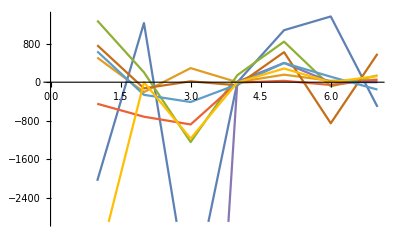

```mathematica
fn[i_]:={a1[1][[i]],a1[2][[i]],a1[3][[i]],a1[4][[i]],a1[5][[i]],a1[6][[i]],a1[7][[i]]}
ListLinePlot[{fn[1],fn[2],fn[3],fn[4],fn[5],fn[6],fn[7],fn[8]}]
```